```mathematica
(1341*12+4)/8
```

2012

```mathematica
(1299*12+4)/8
```

1949

```mathematica
n=34881224
```

34881224

```mathematica
bytes=Import["/Users/john/src/tiim/example/SW_OPER_EFIANOM_0__20211201T120021_20211202T003320_0201.DBL","UnsignedInteger8"];
```

```mathematica
Length@bytes
```

36567288

```mathematica
n
```

34881224

```mathematica
f="/Users/john/src/tiim/example/SW_OPER_EFIANOM_0__20211201T120021_20211202T003320_0201.DBL";
```

```mathematica
i=Import[f,{"EFIL0","TiiImages"}];
```

```mathematica
Manipulate[i[[a]],{a,1,Length@i,1}]
```

Part::partd: Part specification i⟦1⟧ is longer than depth of object.

```mathematica
contB=bytes[[n+1;;n+1+1684624-1]];
```

```mathematica
Length@contB
```

1684624

```mathematica
ExtractBits[{1,5},1,8]
```

5

```mathematica
5*256+19
```

1299

```mathematica
contB[[21;;1996]][[7;;]][[13;;]]
```

{15,0,12,5,19,0,0,0,176,16,1,0,24,1,112,67,10,144,203,19,97,116,29,49,227,37,145,217,16,224,145,2,112,15,0,192,13,0,144,11,0,160,9,0,176,11,0,176,13,0,176,12,0,208,11,0,176,11,0,160,12,0,160,10,0,144,9,0,144,9,0,128,9,0,112,7,0,176,11,0,192,12,0,160,11,0,160,10,0,208,11,0,176,12,1,32,26,0,208,13,0,208,26,3,176,15,0,192,14,1,16,25,4,0,172,22,193,80,20,193,69,20,1,35,27,66,189,39,129,108,4,112,20,0,240,12,0,224,15,1,112,21,0,192,12,0,176,10,0,176,12,0,176,12,0,192,11,0,176,10,0,176,10,0,144,9,0,128,9,0,112,9,0,128,7,0,176,14,0,192,11,0,160,10,0,160,11,0,192,11,0,192,12,1,144,98,1,48,12,0,192,13,1,0,12,0,192,15,1,144,89,14,97,71,19,177,28,17,1,31,17,96,253,17,17,208,46,18,111,15,80,38,1,48,19,2,64,24,2,80,23,0,176,10,0,176,12,0,160,13,0,192,11,0,192,12,0,160,10,0,176,10,0,176,10,0,144,8,0,128,7,0,144,9,0,176,12,0,160,12,0,160,11,0,176,10,0,176,11,0,192,12,0,240,18,0,208,24,1,80,17,1,80,21,1,96,17,4,0,107,14,97,66,20,65,5,16,32,247,16,80,248,13,145,20,29,66,118,32,176,120,1,192,53,1,112,11,0,176,11,0,160,10,0,176,12,0,192,11,0,176,10,0,176,11,0,160,10,0,192,9,0,144,10,0,160,7,0,112,7,0,128,7,0,176,13,0,176,10,0,176,10,0,176,11,0,160,11,0,176,12,0,176,14,0,224,59,2,208,26,4,0,58,3,64,28,6,112,226,16,33,29,14,1,8,15,224,251,15,17,19,14,145,6,21,130,69,36,241,7,3,0,37,1,208,14,0,176,9,0,144,12,0,176,11,0,208,13,0,192,12,0,176,12,0,160,12,0,160,10,0,144,10,0,144,8,0,112,9,0,128,9,0,160,12,0,192,12,0,144,10,0,160,10,0,160,10,0,176,11,0,176,12,0,224,44,2,0,13,1,0,42,2,112,27,8,0,244,13,224,195,11,16,202,14,144,213,14,97,10,11,224,195,16,17,44,27,241,16,2,192,41,3,80,14,0,176,12,0,176,11,0,192,12,0,192,11,0,192,12,0,176,13,0,160,11,0,176,10,0,160,10,0,160,10,0,144,8,0,144,9,0,160,12,0,176,10,0,160,9,0,144,8,0,160,11,0,192,11,0,192,12,0,192,40,2,112,15,0,224,40,1,112,32,8,224,166,9,96,122,8,176,170,12,112,171,14,64,240,10,32,181,12,193,14,23,1,47,9,96,36,1,16,18,0,176,12,0,176,11,0,192,12,0,192,12,0,176,11,0,160,11,0,176,11,0,160,9,0,144,9,0,128,9,0,112,9,0,144,8,0,176,11,0,176,12,0,160,10,0,176,11,0,160,11,0,176,15,2,112,15,0,240,41,2,160,27,1,48,25,1,0,55,10,0,178,8,64,105,8,240,141,11,192,198,13,241,9,12,32,172,9,241,15,21,1,50,6,96,24,4,96,68,1,80,11,0,160,9,0,144,11,0,176,11,0,192,11,0,192,10,0,176,10,0,160,11,0,176,10,0,176,10,0,144,8,0,144,10,0,176,12,0,144,10,0,160,10,0,176,12,0,176,9,0,176,13,1,144,15,2,240,29,3,16,29,1,80,31,1,16,51,7,48,182,10,80,150,6,16,110,6,192,153,13,80,172,11,192,131,9,32,188,13,224,232,5,112,56,4,160,39,2,240,12,0,208,11,0,192,11,0,176,11,0,160,11,0,208,11,0,176,11,0,160,12,0,176,8,0,144,10,0,128,8,0,144,10,0,176,11,0,144,11,0,160,12,0,160,10,0,160,11,0,176,12,0,208,72,3,48,17,1,32,19,1,112,31,1,80,54,6,96,190,7,224,154,7,224,87,6,224,157,14,112,179,7,48,102,10,128,239,16,96,233,6,144,56,2,48,37,0,240,11,0,160,10,0,176,12,0,160,13,0,176,11,0,176,11,0,192,9,0,176,9,0,160,9,0,144,9,0,144,9,0,112,6,0,176,13,0,192,10,0,160,10,0,160,11,0,176,11,0,192,11,0,208,39,2,0,38,1,224,36,2,96,40,2,0,58,6,32,115,6,80,114,7,160,95,6,176,138,10,96,155,9,192,98,7,96,154,17,32,201,6,224,102,3,192,74,1,48,11,0,176,12,0,176,11,0,192,12,0,192,11,0,176,12,0,176,12,0,192,12,0,144,10,0,144,9,0,128,9,0,128,9,0,144,11,0,160,9,0,160,10,0,176,12,0,176,10,0,208,12,1,80,35,1,80,60,5,64,60,3,144,46,1,176,37,4,0,121,9,112,103,8,144,114,6,160,149,8,96,104,7,176,99,10,16,169,15,208,188,2,208,28,3,176,36,0,192,9,0,192,11,0,192,12,0,208,11,0,160,12,0,176,11,0,144,10,0,160,10,0,176,7,0,144,9,0,112,10,0,128,8,0,192,11,0,192,11,0,128,10,0,160,11,0,176,11,0,208,17,4,192,115,4,16,53,3,176,43,2,96,52,3,128,41,7,0,148,10,0,111,11,96,121,8,160,112,8,32,120,8,240,97,8,16,192,12,48,202,3,80,32,2,160,20,0,176,11,0,160,11,0,192,11,0,192,11,0,192,11,0,192,10,0,160,11,0,176,9,0,144,10,0,160,9,0,128,9,0,128,9,0,144,11,0,144,10,0,128,9,0,176,12,0,176,13,2,224,62,23,192,244,14,96,221,14,32,140,4,208,65,4,192,40,4,224,140,8,0,106,7,128,79,8,176,124,7,192,114,8,208,124,7,64,170,13,16,81,2,16,23,0,224,10,0,176,11,0,208,11,0,192,12,0,192,12,0,176,12,0,192,11,0,192,11,0,160,10,0,144,9,0,144,8,0,128,10,0,128,7,0,160,10,0,176,10,0,144,9,0,160,10,0,176,15,11,240,167,16,208,119,6,16,190,16,17,16,7,144,144,5,176,77,4,48,91,7,32,118,6,0,62,8,96,109,8,176,125,6,64,121,9,96,168,10,48,42,1,80,52,1,0,10,0,144,10,0,192,11,0,208,12,0,192,12,0,192,12,0,176,11,0,160,9,0,144,10,0,160,12,0,144,9,0,144,9,0,144,9,0,176,12,0,144,11,0,144,10,0,160,12,0,192,11,2,0,30,1,160,23,1,16,24,1,208,85,9,112,96,7,160,180,7,240,97,5,112,169,7,80,93,7,208,159,11,80,163,9,48,179,15,64,126,4,64,22,1,96,74,1,48,14,0,208,11,0,176,11,0,192,11,0,192,11,0,192,11,0,160,11,0,160,8,0,160,10,0,144,10,0,160,8,0,144,7,0,144,9,0,160,12,0,192,9,0,144,10,0,144,10,0,192,11,0,208,13,0,240,17,1,80,60,2,0,19,1,16,41,2,80,85,10,80,104,6,80,114,6,96,119,6,192,162,14,64,151,11,16,240,8,128,41,1,192,29,1,160,20,0,192,12,0,224,12,0,192,13,0,192,12,0,192,11,0,192,12,0,160,11,0,144,10,0,128,10,0,144,9,0,144,8,0,160,9,0,128,9,0,144,12,0,160,9,0,160,10,0,176,10,0,192,11,0,192,11,0,208,16,1,48,36,1,48,11,1,0,43,1,16,41,2,192,61,1,208,61,6,160,115,6,49,23,16,176,173,7,192,94,2,192,25,3,16,23,4,16,64,0,208,26,8,16,31,0,176,11,0,192,11,0,224,12,0,176,11,0,192,10,0,160,11,0,160,10,0,176,11,0,128,9,0,128,8,0,128,10,0,192,10,0,192,11,0,144,9,0,144,11,0,160,11,0,176,12,0,224,14,0,176,12,0,192,12,1,128,38,0,240,12,0,208,16,1,208,34,2,208,28,3,176,76,5,208,73,1,240,18,1,48,37,4,128,53,8,48,30,1,112,52,13,224,31,0,208,10,0,176,12,0,192,10,0,176,12,0,176,11,0,208,12,0,128,11,0,160,10,0,144,8,0,112,8,0,112,8,0,160,13,0,192,9,0,144,10,0,144,10,0,176,10,0,176,11,0,224,13,0,192,11,0,176,13,5,112,40,0,192,13,0,176,14,0,192,14,1,0,18,1,112,26,1,112,21,1,32,16,1,32,19,1,64,19,1,96,23,8,16,31,0,240,13,0,224,13,0,192,11,0,176,12,0,192,12,0,192,9,0,160,11,0,144,10,0,176,9,0,144,9,0,128,6,0,128,226,219}

```mathematica
f1="/Users/john/src/tiim/build/test.txt";
```

```mathematica
tiiImagePlot[{"H",0,Import[f1,"Table"][[6]]}]
```

-Graphics-

```mathematica
ct=Transpose[ColorData["TemperatureMap"]/@(Range[0,255]/255.)/.RGBColor[r_,g_,b_]:>Floor[255*{r,g,b}]];
```

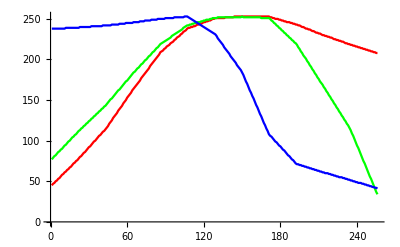

```mathematica
ListLinePlot[ct,PlotStyle->{Red,Green,Blue}]
```

```mathematica
256*3
```

768

```mathematica
StringJoin[{"uint8_t colorsrgbrgb[768] = {",Riffle[Flatten[Transpose[ct]],", "],"};"}/.x_?NumberQ:>ToString[x]]
```

uint8_t colorsrgbrgb[768] = {45, 77, 238, 47, 79, 238, 48, 81, 238, 50, 82, 238, 51, 84, 238, 53, 86, 238, 54, 87, 238, 56, 89, 238, 58, 90, 238, 59, 92, 238, 61, 94, 238, 62, 95, 239, 64, 97, 239, 65, 99, 239, 67, 100, 239, 68, 102, 239, 70, 104, 239, 72, 105, 239, 73, 107, 239, 75, 108, 239, 76, 110, 239, 78, 112, 239, 80, 113, 240, 81, 115, 240, 83, 116, 240, 85, 118, 240, 86, 119, 240, 88, 121, 240, 90, 122, 240, 92, 124, 240, 93, 125, 240, 95, 127, 241, 97, 128, 241, 99, 130, 241, 100, 131, 241, 102, 133, 241, 104, 134, 241, 106, 136, 241, 107, 137, 241, 109, 139, 241, 111, 140, 242, 112, 142, 242, 114, 143, 242, 116, 145, 242, 118, 147, 242, 121, 149, 242, 123, 151, 242, 125, 152, 243, 128, 154, 243, 130, 156, 243, 132, 158, 243, 134, 160, 243, 137, 162, 243, 139, 163, 244, 141, 165, 244, 143, 167, 244, 146, 169, 244, 148, 171, 244, 150, 173, 245, 153, 174, 245, 155, 176, 245, 157, 178, 245, 159, 180, 245, 162, 182, 245, 164, 184, 246, 166, 185, 246, 168, 187, 246, 170, 189, 246, 172, 190, 246, 174, 192, 247, 177, 194, 247, 179, 195, 247, 181, 197, 247, 183, 199, 248, 185, 200, 248, 187, 202, 248, 189, 204, 248, 192, 205, 248, 194, 207, 249, 196, 209, 249, 198, 210, 249, 200, 212, 249, 202, 214, 249, 204, 215, 250, 206, 217, 250, 209, 219, 250, 210, 220, 250, 211, 221, 250, 213, 222, 250, 214, 223, 251, 216, 224, 251, 217, 225, 251, 218, 226, 251, 220, 227, 251, 221, 229, 251, 222, 230, 251, 224, 231, 252, 225, 232, 252, 227, 233, 252, 228, 234, 252, 229, 235, 252, 231, 236, 252, 232, 237, 252, 234, 239, 252, 235, 240, 253, 236, 241, 253, 238, 242, 253, 239, 242, 252, 239, 243, 251, 240, 243, 250, 240, 244, 249, 241, 244, 248, 241, 245, 247, 242, 245, 246, 243, 246, 245, 243, 246, 244, 244, 246, 243, 244, 247, 242, 245, 247, 241, 246, 248, 240, 246, 248, 239, 247, 249, 238, 247, 249, 237, 248, 249, 236, 248, 250, 235, 249, 250, 234, 250, 251, 233, 250, 251, 232, 251, 251, 231, 251, 251, 229, 251, 252, 226, 251, 252, 224, 251, 252, 222, 251, 252, 220, 251, 252, 218, 251, 252, 215, 252, 252, 213, 252, 252, 211, 252, 252, 209, 252, 252, 207, 252, 252, 204, 252, 252, 202, 252, 252, 200, 253, 252, 198, 253, 252, 196, 253, 252, 193, 253, 252, 191, 253, 252, 189, 253, 252, 187, 253, 253, 184, 253, 252, 181, 253, 252, 177, 253, 252, 173, 253, 252, 170, 253, 252, 166, 253, 252, 162, 253, 252, 159, 253, 252, 155, 253, 252, 152, 253, 252, 148, 253, 252, 144, 253, 252, 141, 253, 252, 137, 253, 252, 133, 253, 251, 130, 253, 251, 126, 253, 251, 122, 253, 251, 119, 253, 251, 115, 253, 251, 112, 253, 251, 108, 252, 250, 106, 252, 248, 105, 251, 247, 103, 251, 245, 101, 250, 244, 99, 250, 242, 98, 250, 241, 96, 249, 239, 94, 249, 238, 93, 248, 236, 91, 248, 235, 89, 247, 233, 88, 247, 232, 86, 246, 230, 84, 246, 229, 82, 246, 227, 81, 245, 226, 79, 245, 224, 77, 244, 223, 76, 244, 221, 74, 243, 220, 72, 243, 218, 71, 242, 215, 71, 242, 213, 70, 241, 210, 70, 240, 208, 69, 240, 205, 69, 239, 203, 68, 238, 201, 68, 238, 198, 67, 237, 196, 67, 237, 193, 66, 236, 191, 66, 235, 188, 65, 235, 186, 65, 234, 183, 64, 233, 181, 64, 233, 178, 63, 232, 176, 63, 232, 173, 62, 231, 171, 62, 230, 169, 61, 230, 166, 61, 229, 164, 60, 229, 161, 60, 228, 159, 60, 228, 156, 59, 227, 154, 59, 227, 151, 58, 226, 149, 58, 225, 146, 57, 225, 144, 57, 224, 141, 56, 224, 139, 56, 223, 136, 55, 223, 134, 55, 222, 131, 55, 222, 129, 54, 221, 126, 54, 220, 124, 53, 220, 121, 53, 219, 119, 52, 219, 116, 52, 218, 113, 51, 218, 109, 51, 217, 106, 50, 217, 102, 50, 216, 98, 49, 216, 94, 49, 215, 91, 48, 215, 87, 48, 214, 83, 48, 214, 79, 47, 213, 75, 47, 213, 72, 46, 212, 68, 46, 212, 64, 45, 211, 60, 45, 211, 56, 44, 210, 53, 44, 210, 49, 43, 209, 45, 43, 209, 41, 42, 208, 37, 42, 208, 34, 41};

```mathematica
CharacterRange[]
```

General::argct: CharacterRange called with 0 arguments.

CharacterRange[]

```mathematica
characters=CharacterRange[FromCharacterCode[1],FromCharacterCode[128]];
```

```mathematica
fonts=Rasterize[#,RasterSize->{Automatic,100},ImageResolution->100,ImageSize->100]&/@characters;
```

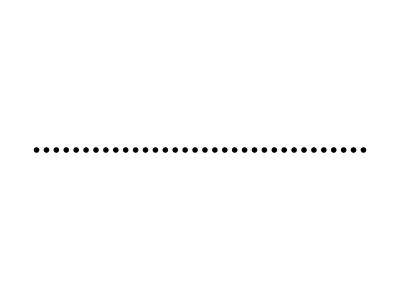

```mathematica
res=GraphicsGrid[fonts[[#]]&/@SplitBy[Flatten[ToCharacterCode["Hello there, Swarm A! How are you?"]/. 10->{10,0}],#==0&],Spacings->{0,0},ImagePadding->None,ImageSize->{Automatic,16}]
```

```mathematica
res=GraphicsGrid[fonts[[#]]&/@SplitBy[Flatten[ToCharacterCode["Hello there, Swarm A! How are you?"]/. 10->{10,0}],#==0&],Spacings->{0,0},ImagePadding->None,ImageSize->{Automatic,20}]
```

-Graphics-

White is 255, black is 254

```mathematica
fontData=(f↦ImageData[Binarize@ImageResize[f,{8,16}*#/12]])/@fonts/. 1->255/. 0->254&/@{9,12,15,18,21,24};
```

```mathematica
fontWidths=Length/@fontData[[All,1,1]]
```

{6,8,10,12,14,16}

```mathematica
Cases[Position[fontData[[1]],254,Infinity],{65,__}]
```

{{65,4,3},{65,4,4},{65,5,3},{65,5,4},{65,6,2},{65,6,4},{65,6,5},{65,7,2},{65,7,3},{65,7,4},{65,7,5},{65,8,2},{65,8,3},{65,8,4},{65,8,5},{65,9,1},{65,9,2},{65,9,5},{65,9,6}}

```mathematica
Position[#,254]&/@fontData[[1]]
```

{{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{{5,3},{5,4},{6,3},{6,4},{7,3},{7,4},{9,3},{9,4},{10,3},{10,4}},{{4,2},{4,3},{4,4},{4,5},{5,2},{5,4},{5,5},{6,2},{6,4},{6,5}},{{5,2},{5,5},{6,1},{6,2},{6,3},{6,4},{6,5},{7,2},{7,5},{8,2},{8,5},{9,1},{9,2},{9,3},{9,4},{9,5}},{{4,3},{4,4},{5,2},{5,5},{6,2},{6,3},{7,3},{7,4},{7,5},{8,5},{9,2},{9,3},{9,4},{9,5},{10,3},{10,4}},{{4,2},{4,3},{5,2},{5,4},{6,2},{6,3},{6,4},{6,5},{7,2},{7,3},{7,4},{8,2},{8,3},{8,4},{8,5},{9,3},{9,5},{10,4}},{{4,2},{4,3},{4,4},{5,2},{5,4},{6,2},{6,3},{7,2},{7,3},{7,5},{7,6},{8,1},{8,4},{8,5},{9,2},{9,3},{9,4},{9,5},{10,3}},{{4,3},{4,4},{5,3},{5,4},{6,3},{6,4}},{{4,5},{5,4},{6,4},{7,3},{7,4},{8,3},{8,4},{9,3},{9,4},{10,4},{11,4},{11,5}},{{4,2},{5,2},{5,3},{6,3},{7,3},{7,4},{8,3},{8,4},{9,3},{10,3},{11,2},{11,3}},{{7,2},{7,3},{7,4},{7,5},{8,3},{8,4},{9,3},{9,4}},{{6,3},{7,3},{7,4},{8,2},{8,3},{8,4},{8,5},{9,3}},{{9,3},{9,4},{10,4},{11,3}},{{7,2},{7,3},{7,4},{7,5},{8,2},{8,3},{8,4},{8,5}},{{9,3},{9,4}},{{4,5},{5,4},{5,5},{6,4},{7,3},{7,4},{8,3},{9,2},{9,3},{10,2}},{{4,2},{4,3},{4,4},{5,2},{5,5},{6,1},{6,2},{6,5},{7,1},{7,2},{7,3},{7,4},{7,5},{8,2},{8,5},{9,2},{9,3},{9,4},{9,5},{10,3},{10,4}},{{4,2},{4,3},{4,4},{5,3},{5,4},{6,3},{6,4},{7,3},{7,4},{8,3},{8,4},{9,2},{9,3},{9,4},{9,5},{10,2},{10,3},{10,4},{10,5}},{{4,2},{4,3},{4,4},{5,2},{5,4},{5,5},{6,5},{7,4},{8,3},{9,2},{9,3},{9,4},{9,5}},{{4,2},{4,3},{4,4},{5,5},{6,4},{6,5},{7,3},{7,4},{7,5},{8,5},{9,2},{9,3},{9,4},{9,5},{10,3},{10,4}},{{4,4},{5,3},{5,4},{5,5},{6,2},{6,3},{6,4},{6,5},{7,1},{7,2},{7,4},{7,5},{8,1},{8,2},{8,3},{8,4},{8,5},{9,4},{9,5}},{{4,2},{4,3},{4,4},{4,5},{5,2},{6,2},{6,3},{6,4},{7,4},{7,5},{8,5},{9,2},{9,3},{9,4},{9,5},{10,3}},{{4,3},{4,4},{4,5},{5,2},{6,2},{6,4},{7,2},{7,3},{7,4},{7,5},{8,2},{8,5},{9,2},{9,3},{9,4},{9,5},{10,3},{10,4}},{{4,2},{4,3},{4,4},{4,5},{5,4},{5,5},{6,4},{7,3},{7,4},{8,3},{9,3}},{{4,2},{4,3},{4,4},{4,5},{5,2},{5,5},{6,2},{6,3},{6,4},{6,5},{7,2},{7,3},{7,4},{7,5},{8,1},{8,2},{8,5},{9,2},{9,3},{9,4},{9,5},{10,3},{10,4}},{{4,2},{4,3},{4,4},{5,2},{5,5},{6,1},{6,2},{6,5},{7,2},{7,3},{7,4},{7,5},{8,5},{9,2},{9,3},{9,4},{9,5},{10,3}},{{5,3},{5,4},{6,3},{6,4},{9,3},{9,4}},{{5,3},{5,4},{6,3},{6,4},{9,3},{9,4},{10,4},{11,3}},{{6,4},{6,5},{7,2},{7,3},{7,4},{8,2},{8,3},{9,3},{9,4},{9,5}},{{7,2},{7,3},{7,4},{7,5},{8,2},{8,3},{8,4},{8,5},{9,2},{9,3},{9,4},{9,5}},{{6,2},{6,3},{7,4},{7,5},{8,4},{8,5},{9,2},{9,3}},{{4,2},{4,3},{4,4},{4,5},{5,4},{5,5},{6,4},{7,3},{9,3},{9,4}},{{4,3},{4,4},{5,2},{5,3},{5,4},{5,5},{6,1},{6,2},{6,3},{6,4},{6,5},{6,6},{7,1},{7,2},{7,4},{7,5},{7,6},{8,1},{8,2},{8,3},{8,4},{8,5},{8,6},{9,1},{9,2},{9,3},{9,4},{9,5},{10,3},{10,4}},{{4,3},{4,4},{5,3},{5,4},{6,2},{6,4},{6,5},{7,2},{7,3},{7,4},{7,5},{8,2},{8,3},{8,4},{8,5},{9,1},{9,2},{9,5},{9,6}},{{4,2},{4,3},{4,4},{4,5},{5,2},{5,5},{6,2},{6,3},{6,4},{6,5},{7,2},{7,3},{7,4},{7,5},{8,2},{8,5},{9,2},{9,3},{9,4},{9,5}},{{4,3},{4,4},{4,5},{5,2},{6,1},{6,2},{7,1},{7,2},{8,2},{9,2},{9,3},{9,4},{9,5},{10,4}},{{4,2},{4,3},{4,4},{5,2},{5,5},{6,2},{6,5},{7,2},{7,5},{8,2},{8,5},{9,2},{9,3},{9,4},{9,5}},{{4,2},{4,3},{4,4},{4,5},{5,2},{6,2},{6,3},{6,4},{7,2},{7,3},{7,4},{8,2},{9,2},{9,3},{9,4},{9,5}},{{4,2},{4,3},{4,4},{4,5},{5,2},{6,2},{6,3},{7,2},{7,3},{7,4},{7,5},{8,2},{9,2}},{{4,2},{4,3},{4,4},{4,5},{5,2},{6,1},{6,2},{7,1},{7,2},{7,4},{7,5},{8,2},{8,5},{9,2},{9,3},{9,4},{9,5},{10,4}},{{4,2},{4,5},{5,2},{5,5},{6,2},{6,3},{6,4},{6,5},{7,2},{7,3},{7,4},{7,5},{8,2},{8,5},{9,2},{9,5}},{{4,2},{4,3},{4,4},{4,5},{5,3},{5,4},{6,3},{6,4},{7,3},{7,4},{8,3},{8,4},{9,2},{9,3},{9,4},{9,5},{10,2}},{{4,2},{4,3},{4,4},{4,5},{5,5},{6,5},{7,5},{8,5},{9,2},{9,3},{9,4},{9,5},{10,3}},{{4,2},{4,5},{5,2},{5,4},{6,2},{6,3},{6,4},{7,2},{7,3},{7,4},{8,2},{8,4},{8,5},{9,2},{9,5}},{{4,2},{5,2},{6,2},{7,2},{8,2},{9,2},{9,3},{9,4},{9,5}},{{4,2},{4,5},{5,2},{5,5},{6,2},{6,3},{6,4},{6,5},{7,2},{7,3},{7,4},{7,5},{8,2},{8,5},{9,2},{9,5}},{{4,2},{4,5},{5,2},{5,3},{5,5},{6,2},{6,3},{6,5},{7,2},{7,4},{7,5},{8,2},{8,4},{8,5},{9,2},{9,5}},{{4,2},{4,3},{4,4},{4,5},{5,2},{5,5},{6,1},{6,2},{6,5},{6,6},{7,1},{7,2},{7,5},{7,6},{8,1},{8,2},{8,5},{9,2},{9,3},{9,4},{9,5},{10,3},{10,4}},{{4,2},{4,3},{4,4},{4,5},{5,2},{5,5},{6,2},{6,5},{7,2},{7,3},{7,4},{7,5},{8,2},{9,2}},{{4,2},{4,3},{4,4},{4,5},{5,2},{5,5},{6,1},{6,2},{6,5},{7,1},{7,2},{7,5},{8,1},{8,2},{8,5},{9,2},{9,3},{9,4},{9,5},{10,3},{10,4},{11,4},{11,5}},{{4,2},{4,3},{4,4},{4,5},{5,2},{5,5},{6,2},{6,5},{7,2},{7,3},{7,4},{8,2},{8,4},{9,2},{9,5}},{{4,2},{4,3},{4,4},{4,5},{5,2},{6,2},{6,3},{7,3},{7,4},{7,5},{8,5},{9,2},{9,3},{9,4},{9,5},{10,3},{10,4}},{{4,1},{4,2},{4,3},{4,4},{4,5},{5,3},{5,4},{6,3},{6,4},{7,3},{7,4},{8,3},{8,4},{9,3},{9,4}},{{4,2},{4,5},{5,2},{5,5},{6,2},{6,5},{7,2},{7,5},{8,2},{8,5},{9,2},{9,3},{9,4},{9,5},{10,3}},{{4,1},{4,2},{4,5},{5,2},{5,5},{6,2},{6,5},{7,2},{7,3},{7,4},{7,5},{8,3},{8,4},{9,3},{9,4}},{{4,1},{4,6},{5,1},{5,5},{5,6},{6,1},{6,3},{6,4},{6,5},{6,6},{7,1},{7,2},{7,3},{7,4},{7,5},{8,2},{8,3},{8,4},{8,5},{9,2},{9,4},{9,5}},{{4,2},{4,5},{5,2},{5,3},{5,4},{5,5},{6,3},{6,4},{7,3},{7,4},{8,2},{8,3},{8,4},{8,5},{9,2},{9,5}},{{4,1},{4,2},{4,5},{5,2},{5,5},{6,2},{6,3},{6,4},{7,3},{7,4},{8,3},{8,4},{9,3},{9,4}},{{4,2},{4,3},{4,4},{4,5},{5,4},{5,5},{6,4},{7,3},{8,2},{8,3},{9,2},{9,3},{9,4},{9,5}},{{4,3},{4,4},{5,3},{5,4},{6,3},{6,4},{7,3},{7,4},{8,3},{8,4},{9,3},{9,4},{10,3},{11,3},{11,4}},{{3,2},{4,2},{5,2},{5,3},{6,3},{7,3},{7,4},{8,4},{9,4},{10,4},{10,5},{11,5}},{{4,2},{4,3},{5,3},{5,4},{6,3},{6,4},{7,3},{7,4},{8,3},{8,4},{9,3},{9,4},{10,3},{10,4},{11,2},{11,3},{11,4}},{{4,3},{4,4},{5,3},{5,4},{6,2},{6,4},{6,5},{7,2},{7,5}},{{10,2},{10,3},{10,4},{10,5},{11,1},{11,2},{11,3},{11,4},{11,5}},{{3,3},{4,3},{4,4}},{{5,3},{5,4},{6,2},{6,4},{6,5},{7,3},{7,4},{7,5},{8,2},{8,5},{9,2},{9,3},{9,4},{9,5},{10,3}},{{4,2},{5,2},{5,4},{6,2},{6,3},{6,4},{6,5},{7,2},{7,5},{8,2},{8,5},{9,2},{9,3},{9,4},{9,5}},{{5,3},{5,4},{5,5},{6,2},{6,3},{6,4},{6,5},{7,2},{8,2},{9,2},{9,3},{9,4},{9,5},{10,3},{10,4}},{{3,5},{4,5},{5,3},{5,4},{5,5},{6,2},{6,3},{6,4},{6,5},{7,1},{7,2},{7,5},{8,1},{8,2},{8,5},{9,2},{9,3},{9,4},{9,5},{10,3}},{{5,3},{5,4},{6,2},{6,3},{6,4},{6,5},{7,1},{7,2},{7,3},{7,4},{7,5},{8,1},{8,2},{9,2},{9,3},{9,4},{9,5},{10,3},{10,4}},{{3,4},{3,5},{4,3},{4,4},{5,2},{5,3},{5,4},{5,5},{6,2},{6,3},{6,4},{6,5},{7,3},{8,3},{9,3}},{{5,3},{5,4},{5,5},{6,2},{6,3},{6,4},{6,5},{7,2},{7,4},{7,5},{8,2},{8,3},{8,4},{9,2},{9,3},{9,4},{9,5},{10,2},{10,3},{10,4},{10,5},{10,6},{11,2},{11,3},{11,4},{11,5},{12,3},{12,4}},{{4,2},{5,2},{5,4},{6,2},{6,3},{6,4},{6,5},{7,2},{7,5},{8,2},{8,5},{9,2},{9,5}},{{3,4},{4,4},{5,2},{5,3},{6,2},{6,3},{6,4},{7,4},{8,4},{9,4}},{{3,4},{4,4},{5,2},{5,3},{6,2},{6,3},{6,4},{7,4},{8,4},{9,4},{10,4},{11,2},{11,3},{11,4}},{{4,2},{5,2},{6,2},{6,4},{6,5},{7,2},{7,3},{7,4},{8,2},{8,3},{8,4},{9,2},{9,5}},{{3,2},{3,3},{4,2},{4,3},{4,4},{5,3},{5,4},{6,3},{6,4},{7,3},{7,4},{8,3},{8,4},{9,3},{9,4},{9,5},{10,4},{10,5}},{{5,2},{5,3},{5,4},{5,5},{6,1},{6,2},{6,3},{6,4},{6,5},{6,6},{7,1},{7,2},{7,3},{7,4},{7,5},{7,6},{8,1},{8,2},{8,3},{8,4},{8,5},{8,6},{9,1},{9,2},{9,3},{9,4},{9,5},{9,6}},{{5,4},{6,2},{6,3},{6,4},{6,5},{7,2},{7,5},{8,2},{8,5},{9,2},{9,5}},{{5,3},{5,4},{6,2},{6,3},{6,4},{6,5},{7,1},{7,2},{7,5},{8,1},{8,2},{8,5},{9,2},{9,3},{9,4},{9,5},{10,3},{10,4}},{{5,4},{6,2},{6,3},{6,4},{6,5},{7,2},{7,5},{8,2},{8,5},{9,2},{9,3},{9,4},{9,5},{10,2},{10,4},{11,2}},{{5,3},{5,4},{6,2},{6,3},{6,4},{6,5},{7,1},{7,2},{7,5},{8,1},{8,2},{8,5},{9,2},{9,3},{9,4},{9,5},{10,3},{10,5},{11,5}},{{5,4},{5,5},{6,2},{6,3},{6,4},{6,5},{7,2},{7,3},{8,2},{8,3},{9,2},{9,3}},{{5,3},{5,4},{6,2},{6,3},{6,4},{6,5},{7,2},{7,3},{7,4},{8,4},{8,5},{9,2},{9,3},{9,4},{9,5},{10,3},{10,4}},{{4,3},{5,2},{5,3},{5,4},{5,5},{6,2},{6,3},{6,4},{6,5},{7,3},{8,3},{9,3},{9,4},{9,5},{10,4},{10,5}},{{6,2},{6,5},{7,2},{7,5},{8,2},{8,5},{9,2},{9,3},{9,4},{9,5},{10,3}},{{6,2},{6,5},{7,2},{7,5},{8,2},{8,3},{8,4},{9,3},{9,4}},{{6,1},{6,3},{6,4},{6,6},{7,1},{7,2},{7,3},{7,4},{7,5},{7,6},{8,2},{8,3},{8,4},{8,5},{9,2},{9,4},{9,5}},{{6,2},{6,4},{6,5},{7,3},{7,4},{8,3},{8,4},{9,2},{9,5}},{{6,2},{6,5},{7,2},{7,5},{8,3},{8,4},{9,3},{9,4},{10,3},{10,4},{11,2},{11,3}},{{5,2},{5,3},{5,4},{5,5},{6,2},{6,3},{6,4},{6,5},{7,3},{7,4},{8,2},{8,3},{9,2},{9,3},{9,4},{9,5},{10,2},{10,3},{10,4},{10,5}},{{4,4},{5,3},{5,4},{6,3},{7,3},{8,3},{9,3},{10,3},{11,4}},{{4,3},{4,4},{5,3},{5,4},{6,3},{6,4},{7,3},{7,4},{8,3},{8,4},{9,3},{9,4},{10,3},{10,4},{11,3},{11,4}},{{4,2},{4,3},{5,3},{5,4},{6,3},{6,4},{7,3},{7,4},{8,4},{9,3},{9,4},{10,3},{10,4},{11,3}},{{7,2},{7,3},{7,5},{8,2},{8,3},{8,4},{8,5}},{},{{4,3},{4,4},{4,5},{4,6},{5,2},{5,3},{5,6},{6,1},{6,2},{6,3},{6,4},{7,1},{7,2},{7,3},{7,4},{8,2},{8,3},{9,2},{9,3},{9,5},{9,6},{10,4},{10,5}}}

```mathematica
Length@fontData[[1,65]]
```

12

```mathematica
Length@fontData[[1]]
```

128

```mathematica
define[font2C];
font2C[size_,fontData_]:=StringJoin[
  Riffle[
    MapIndexed[
      With[
        {
          p=Position[#,254]
        }
      , "int8_t font"<>ToString[size]<>"["<>ToString[#2[[1]]-1]<>"]["<>If[Length@p===0,"1",ToString[Length@p*2]]<>"] = {"
         <>If[Length@p===0,"-1",Riffle[ToString/@Flatten[p-1],","]]<>"};"
      ]&
    , fontData
    ]
  , "\n"
  ]
]
```

```mathematica
Position[#,254,Infinity]&
```

```mathematica
define[font2C];
font2C[size_,fontData_]:=Module[
  {
    positions
  , positionCodes
  }
, positions = (Position[#,254]&/@fontData)
; positionCodes = Flatten[Append[#,-1]&/@positions]
; StringJoin[
    "int8_t font"<>ToString[size]<>"["<>ToString[Length@positionCodes]<>"] = {"
  , Riffle[ToString/@positionCodes,", "]
  , "};"
   ]
]
```

```mathematica
res=StringJoin[Riffle[MapThread[font2C[#1,#2]&,{{9,12,15,18,21,24},fontData}],"\n"]];
```

```mathematica
ByteCount[res]
```

158888

```mathematica
res
```

int8_t font9[2890] = {-1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, 5, 3, 5, 4, 6, 3, 6, 4, 7, 3, 7, 4, 9, 3, 9, 4, 10, 3, 10, 4, -1, 4, 2, 4, 3, 4, 4, 4, 5, 5, 2, 5, 4, 5, 5, 6, 2, 6, 4, 6, 5, -1, 5, 2, 5, 5, 6, 1, 6, 2, 6, 3, 6, 4, 6, 5, 7, 2, 7, 5, 8, 2, 8, 5, 9, 1, 9, 2, 9, 3, 9, 4, 9, 5, -1, 4, 3, 4, 4, 5, 2, 5, 5, 6, 2, 6, 3, 7, 3, 7, 4, 7, 5, 8, 5, 9, 2, 9, 3, 9, 4, 9, 5, 10, 3, 10, 4, -1, 4, 2, 4, 3, 5, 2, 5, 4, 6, 2, 6, 3, 6, 4, 6, 5, 7, 2, 7, 3, 7, 4, 8, 2, 8, 3, 8, 4, 8, 5, 9, 3, 9, 5, 10, 4, -1, 4, 2, 4, 3, 4, 4, 5, 2, 5, 4, 6, 2, 6, 3, 7, 2, 7, 3, 7, 5, 7, 6, 8, 1, 8, 4, 8, 5, 9, 2, 9, 3, 9, 4, 9, 5, 10, 3, -1, 4, 3, 4, 4, 5, 3, 5, 4, 6, 3, 6, 4, -1, 4, 5, 5, 4, 6, 4, 7, 3, 7, 4, 8, 3, 8, 4, 9, 3, 9, 4, 10, 4, 11, 4, 11, 5, -1, 4, 2, 5, 2, 5, 3, 6, 3, 7, 3, 7, 4, 8, 3, 8, 4, 9, 3, 10, 3, 11, 2, 11, 3, -1, 7, 2, 7, 3, 7, 4, 7, 5, 8, 3, 8, 4, 9, 3, 9, 4, -1, 6, 3, 7, 3, 7, 4, 8, 2, 8, 3, 8, 4, 8, 5, 9, 3, -1, 9, 3, 9, 4, 10, 4, 11, 3, -1, 7, 2, 7, 3, 7, 4, 7, 5, 8, 2, 8, 3, 8, 4, 8, 5, -1, 9, 3, 9, 4, -1, 4, 5, 5, 4, 5, 5, 6, 4, 7, 3, 7, 4, 8, 3, 9, 2, 9, 3, 10, 2, -1, 4, 2, 4, 3, 4, 4, 5, 2, 5, 5, 6, 1, 6, 2, 6, 5, 7, 1, 7, 2, 7, 3, 7, 4, 7, 5, 8, 2, 8, 5, 9, 2, 9, 3, 9, 4, 9, 5, 10, 3, 10, 4, -1, 4, 2, 4, 3, 4, 4, 5, 3, 5, 4, 6, 3, 6, 4, 7, 3, 7, 4, 8, 3, 8, 4, 9, 2, 9, 3, 9, 4, 9, 5, 10, 2, 10, 3, 10, 4, 10, 5, -1, 4, 2, 4, 3, 4, 4, 5, 2, 5, 4, 5, 5, 6, 5, 7, 4, 8, 3, 9, 2, 9, 3, 9, 4, 9, 5, -1, 4, 2, 4, 3, 4, 4, 5, 5, 6, 4, 6, 5, 7, 3, 7, 4, 7, 5, 8, 5, 9, 2, 9, 3, 9, 4, 9, 5, 10, 3, 10, 4, -1, 4, 4, 5, 3, 5, 4, 5, 5, 6, 2, 6, 3, 6, 4, 6, 5, 7, 1, 7, 2, 7, 4, 7, 5, 8, 1, 8, 2, 8, 3, 8, 4, 8, 5, 9, 4, 9, 5, -1, 4, 2, 4, 3, 4, 4, 4, 5, 5, 2, 6, 2, 6, 3, 6, 4, 7, 4, 7, 5, 8, 5, 9, 2, 9, 3, 9, 4, 9, 5, 10, 3, -1, 4, 3, 4, 4, 4, 5, 5, 2, 6, 2, 6, 4, 7, 2, 7, 3, 7, 4, 7, 5, 8, 2, 8, 5, 9, 2, 9, 3, 9, 4, 9, 5, 10, 3, 10, 4, -1, 4, 2, 4, 3, 4, 4, 4, 5, 5, 4, 5, 5, 6, 4, 7, 3, 7, 4, 8, 3, 9, 3, -1, 4, 2, 4, 3, 4, 4, 4, 5, 5, 2, 5, 5, 6, 2, 6, 3, 6, 4, 6, 5, 7, 2, 7, 3, 7, 4, 7, 5, 8, 1, 8, 2, 8, 5, 9, 2, 9, 3, 9, 4, 9, 5, 10, 3, 10, 4, -1, 4, 2, 4, 3, 4, 4, 5, 2, 5, 5, 6, 1, 6, 2, 6, 5, 7, 2, 7, 3, 7, 4, 7, 5, 8, 5, 9, 2, 9, 3, 9, 4, 9, 5, 10, 3, -1, 5, 3, 5, 4, 6, 3, 6, 4, 9, 3, 9, 4, -1, 5, 3, 5, 4, 6, 3, 6, 4, 9, 3, 9, 4, 10, 4, 11, 3, -1, 6, 4, 6, 5, 7, 2, 7, 3, 7, 4, 8, 2, 8, 3, 9, 3, 9, 4, 9, 5, -1, 7, 2, 7, 3, 7, 4, 7, 5, 8, 2, 8, 3, 8, 4, 8, 5, 9, 2, 9, 3, 9, 4, 9, 5, -1, 6, 2, 6, 3, 7, 4, 7, 5, 8, 4, 8, 5, 9, 2, 9, 3, -1, 4, 2, 4, 3, 4, 4, 4, 5, 5, 4, 5, 5, 6, 4, 7, 3, 9, 3, 9, 4, -1, 4, 3, 4, 4, 5, 2, 5, 3, 5, 4, 5, 5, 6, 1, 6, 2, 6, 3, 6, 4, 6, 5, 6, 6, 7, 1, 7, 2, 7, 4, 7, 5, 7, 6, 8, 1, 8, 2, 8, 3, 8, 4, 8, 5, 8, 6, 9, 1, 9, 2, 9, 3, 9, 4, 9, 5, 10, 3, 10, 4, -1, 4, 3, 4, 4, 5, 3, 5, 4, 6, 2, 6, 4, 6, 5, 7, 2, 7, 3, 7, 4, 7, 5, 8, 2, 8, 3, 8, 4, 8, 5, 9, 1, 9, 2, 9, 5, 9, 6, -1, 4, 2, 4, 3, 4, 4, 4, 5, 5, 2, 5, 5, 6, 2, 6, 3, 6, 4, 6, 5, 7, 2, 7, 3, 7, 4, 7, 5, 8, 2, 8, 5, 9, 2, 9, 3, 9, 4, 9, 5, -1, 4, 3, 4, 4, 4, 5, 5, 2, 6, 1, 6, 2, 7, 1, 7, 2, 8, 2, 9, 2, 9, 3, 9, 4, 9, 5, 10, 4, -1, 4, 2, 4, 3, 4, 4, 5, 2, 5, 5, 6, 2, 6, 5, 7, 2, 7, 5, 8, 2, 8, 5, 9, 2, 9, 3, 9, 4, 9, 5, -1, 4, 2, 4, 3, 4, 4, 4, 5, 5, 2, 6, 2, 6, 3, 6, 4, 7, 2, 7, 3, 7, 4, 8, 2, 9, 2, 9, 3, 9, 4, 9, 5, -1, 4, 2, 4, 3, 4, 4, 4, 5, 5, 2, 6, 2, 6, 3, 7, 2, 7, 3, 7, 4, 7, 5, 8, 2, 9, 2, -1, 4, 2, 4, 3, 4, 4, 4, 5, 5, 2, 6, 1, 6, 2, 7, 1, 7, 2, 7, 4, 7, 5, 8, 2, 8, 5, 9, 2, 9, 3, 9, 4, 9, 5, 10, 4, -1, 4, 2, 4, 5, 5, 2, 5, 5, 6, 2, 6, 3, 6, 4, 6, 5, 7, 2, 7, 3, 7, 4, 7, 5, 8, 2, 8, 5, 9, 2, 9, 5, -1, 4, 2, 4, 3, 4, 4, 4, 5, 5, 3, 5, 4, 6, 3, 6, 4, 7, 3, 7, 4, 8, 3, 8, 4, 9, 2, 9, 3, 9, 4, 9, 5, 10, 2, -1, 4, 2, 4, 3, 4, 4, 4, 5, 5, 5, 6, 5, 7, 5, 8, 5, 9, 2, 9, 3, 9, 4, 9, 5, 10, 3, -1, 4, 2, 4, 5, 5, 2, 5, 4, 6, 2, 6, 3, 6, 4, 7, 2, 7, 3, 7, 4, 8, 2, 8, 4, 8, 5, 9, 2, 9, 5, -1, 4, 2, 5, 2, 6, 2, 7, 2, 8, 2, 9, 2, 9, 3, 9, 4, 9, 5, -1, 4, 2, 4, 5, 5, 2, 5, 5, 6, 2, 6, 3, 6, 4, 6, 5, 7, 2, 7, 3, 7, 4, 7, 5, 8, 2, 8, 5, 9, 2, 9, 5, -1, 4, 2, 4, 5, 5, 2, 5, 3, 5, 5, 6, 2, 6, 3, 6, 5, 7, 2, 7, 4, 7, 5, 8, 2, 8, 4, 8, 5, 9, 2, 9, 5, -1, 4, 2, 4, 3, 4, 4, 4, 5, 5, 2, 5, 5, 6, 1, 6, 2, 6, 5, 6, 6, 7, 1, 7, 2, 7, 5, 7, 6, 8, 1, 8, 2, 8, 5, 9, 2, 9, 3, 9, 4, 9, 5, 10, 3, 10, 4, -1, 4, 2, 4, 3, 4, 4, 4, 5, 5, 2, 5, 5, 6, 2, 6, 5, 7, 2, 7, 3, 7, 4, 7, 5, 8, 2, 9, 2, -1, 4, 2, 4, 3, 4, 4, 4, 5, 5, 2, 5, 5, 6, 1, 6, 2, 6, 5, 7, 1, 7, 2, 7, 5, 8, 1, 8, 2, 8, 5, 9, 2, 9, 3, 9, 4, 9, 5, 10, 3, 10, 4, 11, 4, 11, 5, -1, 4, 2, 4, 3, 4, 4, 4, 5, 5, 2, 5, 5, 6, 2, 6, 5, 7, 2, 7, 3, 7, 4, 8, 2, 8, 4, 9, 2, 9, 5, -1, 4, 2, 4, 3, 4, 4, 4, 5, 5, 2, 6, 2, 6, 3, 7, 3, 7, 4, 7, 5, 8, 5, 9, 2, 9, 3, 9, 4, 9, 5, 10, 3, 10, 4, -1, 4, 1, 4, 2, 4, 3, 4, 4, 4, 5, 5, 3, 5, 4, 6, 3, 6, 4, 7, 3, 7, 4, 8, 3, 8, 4, 9, 3, 9, 4, -1, 4, 2, 4, 5, 5, 2, 5, 5, 6, 2, 6, 5, 7, 2, 7, 5, 8, 2, 8, 5, 9, 2, 9, 3, 9, 4, 9, 5, 10, 3, -1, 4, 1, 4, 2, 4, 5, 5, 2, 5, 5, 6, 2, 6, 5, 7, 2, 7, 3, 7, 4, 7, 5, 8, 3, 8, 4, 9, 3, 9, 4, -1, 4, 1, 4, 6, 5, 1, 5, 5, 5, 6, 6, 1, 6, 3, 6, 4, 6, 5, 6, 6, 7, 1, 7, 2, 7, 3, 7, 4, 7, 5, 8, 2, 8, 3, 8, 4, 8, 5, 9, 2, 9, 4, 9, 5, -1, 4, 2, 4, 5, 5, 2, 5, 3, 5, 4, 5, 5, 6, 3, 6, 4, 7, 3, 7, 4, 8, 2, 8, 3, 8, 4, 8, 5, 9, 2, 9, 5, -1, 4, 1, 4, 2, 4, 5, 5, 2, 5, 5, 6, 2, 6, 3, 6, 4, 7, 3, 7, 4, 8, 3, 8, 4, 9, 3, 9, 4, -1, 4, 2, 4, 3, 4, 4, 4, 5, 5, 4, 5, 5, 6, 4, 7, 3, 8, 2, 8, 3, 9, 2, 9, 3, 9, 4, 9, 5, -1, 4, 3, 4, 4, 5, 3, 5, 4, 6, 3, 6, 4, 7, 3, 7, 4, 8, 3, 8, 4, 9, 3, 9, 4, 10, 3, 11, 3, 11, 4, -1, 3, 2, 4, 2, 5, 2, 5, 3, 6, 3, 7, 3, 7, 4, 8, 4, 9, 4, 10, 4, 10, 5, 11, 5, -1, 4, 2, 4, 3, 5, 3, 5, 4, 6, 3, 6, 4, 7, 3, 7, 4, 8, 3, 8, 4, 9, 3, 9, 4, 10, 3, 10, 4, 11, 2, 11, 3, 11, 4, -1, 4, 3, 4, 4, 5, 3, 5, 4, 6, 2, 6, 4, 6, 5, 7, 2, 7, 5, -1, 10, 2, 10, 3, 10, 4, 10, 5, 11, 1, 11, 2, 11, 3, 11, 4, 11, 5, -1, 3, 3, 4, 3, 4, 4, -1, 5, 3, 5, 4, 6, 2, 6, 4, 6, 5, 7, 3, 7, 4, 7, 5, 8, 2, 8, 5, 9, 2, 9, 3, 9, 4, 9, 5, 10, 3, -1, 4, 2, 5, 2, 5, 4, 6, 2, 6, 3, 6, 4, 6, 5, 7, 2, 7, 5, 8, 2, 8, 5, 9, 2, 9, 3, 9, 4, 9, 5, -1, 5, 3, 5, 4, 5, 5, 6, 2, 6, 3, 6, 4, 6, 5, 7, 2, 8, 2, 9, 2, 9, 3, 9, 4, 9, 5, 10, 3, 10, 4, -1, 3, 5, 4, 5, 5, 3, 5, 4, 5, 5, 6, 2, 6, 3, 6, 4, 6, 5, 7, 1, 7, 2, 7, 5, 8, 1, 8, 2, 8, 5, 9, 2, 9, 3, 9, 4, 9, 5, 10, 3, -1, 5, 3, 5, 4, 6, 2, 6, 3, 6, 4, 6, 5, 7, 1, 7, 2, 7, 3, 7, 4, 7, 5, 8, 1, 8, 2, 9, 2, 9, 3, 9, 4, 9, 5, 10, 3, 10, 4, -1, 3, 4, 3, 5, 4, 3, 4, 4, 5, 2, 5, 3, 5, 4, 5, 5, 6, 2, 6, 3, 6, 4, 6, 5, 7, 3, 8, 3, 9, 3, -1, 5, 3, 5, 4, 5, 5, 6, 2, 6, 3, 6, 4, 6, 5, 7, 2, 7, 4, 7, 5, 8, 2, 8, 3, 8, 4, 9, 2, 9, 3, 9, 4, 9, 5, 10, 2, 10, 3, 10, 4, 10, 5, 10, 6, 11, 2, 11, 3, 11, 4, 11, 5, 12, 3, 12, 4, -1, 4, 2, 5, 2, 5, 4, 6, 2, 6, 3, 6, 4, 6, 5, 7, 2, 7, 5, 8, 2, 8, 5, 9, 2, 9, 5, -1, 3, 4, 4, 4, 5, 2, 5, 3, 6, 2, 6, 3, 6, 4, 7, 4, 8, 4, 9, 4, -1, 3, 4, 4, 4, 5, 2, 5, 3, 6, 2, 6, 3, 6, 4, 7, 4, 8, 4, 9, 4, 10, 4, 11, 2, 11, 3, 11, 4, -1, 4, 2, 5, 2, 6, 2, 6, 4, 6, 5, 7, 2, 7, 3, 7, 4, 8, 2, 8, 3, 8, 4, 9, 2, 9, 5, -1, 3, 2, 3, 3, 4, 2, 4, 3, 4, 4, 5, 3, 5, 4, 6, 3, 6, 4, 7, 3, 7, 4, 8, 3, 8, 4, 9, 3, 9, 4, 9, 5, 10, 4, 10, 5, -1, 5, 2, 5, 3, 5, 4, 5, 5, 6, 1, 6, 2, 6, 3, 6, 4, 6, 5, 6, 6, 7, 1, 7, 2, 7, 3, 7, 4, 7, 5, 7, 6, 8, 1, 8, 2, 8, 3, 8, 4, 8, 5, 8, 6, 9, 1, 9, 2, 9, 3, 9, 4, 9, 5, 9, 6, -1, 5, 4, 6, 2, 6, 3, 6, 4, 6, 5, 7, 2, 7, 5, 8, 2, 8, 5, 9, 2, 9, 5, -1, 5, 3, 5, 4, 6, 2, 6, 3, 6, 4, 6, 5, 7, 1, 7, 2, 7, 5, 8, 1, 8, 2, 8, 5, 9, 2, 9, 3, 9, 4, 9, 5, 10, 3, 10, 4, -1, 5, 4, 6, 2, 6, 3, 6, 4, 6, 5, 7, 2, 7, 5, 8, 2, 8, 5, 9, 2, 9, 3, 9, 4, 9, 5, 10, 2, 10, 4, 11, 2, -1, 5, 3, 5, 4, 6, 2, 6, 3, 6, 4, 6, 5, 7, 1, 7, 2, 7, 5, 8, 1, 8, 2, 8, 5, 9, 2, 9, 3, 9, 4, 9, 5, 10, 3, 10, 5, 11, 5, -1, 5, 4, 5, 5, 6, 2, 6, 3, 6, 4, 6, 5, 7, 2, 7, 3, 8, 2, 8, 3, 9, 2, 9, 3, -1, 5, 3, 5, 4, 6, 2, 6, 3, 6, 4, 6, 5, 7, 2, 7, 3, 7, 4, 8, 4, 8, 5, 9, 2, 9, 3, 9, 4, 9, 5, 10, 3, 10, 4, -1, 4, 3, 5, 2, 5, 3, 5, 4, 5, 5, 6, 2, 6, 3, 6, 4, 6, 5, 7, 3, 8, 3, 9, 3, 9, 4, 9, 5, 10, 4, 10, 5, -1, 6, 2, 6, 5, 7, 2, 7, 5, 8, 2, 8, 5, 9, 2, 9, 3, 9, 4, 9, 5, 10, 3, -1, 6, 2, 6, 5, 7, 2, 7, 5, 8, 2, 8, 3, 8, 4, 9, 3, 9, 4, -1, 6, 1, 6, 3, 6, 4, 6, 6, 7, 1, 7, 2, 7, 3, 7, 4, 7, 5, 7, 6, 8, 2, 8, 3, 8, 4, 8, 5, 9, 2, 9, 4, 9, 5, -1, 6, 2, 6, 4, 6, 5, 7, 3, 7, 4, 8, 3, 8, 4, 9, 2, 9, 5, -1, 6, 2, 6, 5, 7, 2, 7, 5, 8, 3, 8, 4, 9, 3, 9, 4, 10, 3, 10, 4, 11, 2, 11, 3, -1, 5, 2, 5, 3, 5, 4, 5, 5, 6, 2, 6, 3, 6, 4, 6, 5, 7, 3, 7, 4, 8, 2, 8, 3, 9, 2, 9, 3, 9, 4, 9, 5, 10, 2, 10, 3, 10, 4, 10, 5, -1, 4, 4, 5, 3, 5, 4, 6, 3, 7, 3, 8, 3, 9, 3, 10, 3, 11, 4, -1, 4, 3, 4, 4, 5, 3, 5, 4, 6, 3, 6, 4, 7, 3, 7, 4, 8, 3, 8, 4, 9, 3, 9, 4, 10, 3, 10, 4, 11, 3, 11, 4, -1, 4, 2, 4, 3, 5, 3, 5, 4, 6, 3, 6, 4, 7, 3, 7, 4, 8, 4, 9, 3, 9, 4, 10, 3, 10, 4, 11, 3, -1, 7, 2, 7, 3, 7, 5, 8, 2, 8, 3, 8, 4, 8, 5, -1, -1, 4, 3, 4, 4, 4, 5, 4, 6, 5, 2, 5, 3, 5, 6, 6, 1, 6, 2, 6, 3, 6, 4, 7, 1, 7, 2, 7, 3, 7, 4, 8, 2, 8, 3, 9, 2, 9, 3, 9, 5, 9, 6, 10, 4, 10, 5, -1};
int8_t font12[4270] = {-1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, 6, 4, 6, 5, 7, 4, 7, 5, 8, 4, 8, 5, 9, 4, 9, 5, 10, 4, 12, 4, 12, 5, 13, 4, 13, 5, -1, 5, 3, 5, 6, 6, 3, 6, 6, 7, 3, 7, 6, 8, 3, 8, 6, -1, 6, 2, 7, 1, 7, 2, 7, 3, 7, 4, 7, 5, 7, 6, 7, 7, 8, 2, 8, 3, 8, 6, 8, 7, 9, 2, 9, 6, 9, 7, 10, 2, 10, 6, 10, 7, 11, 1, 11, 2, 11, 3, 11, 4, 11, 5, 11, 6, 11, 7, 12, 2, 12, 3, 12, 6, 12, 7, -1, 4, 4, 4, 5, 5, 4, 5, 5, 6, 3, 6, 4, 6, 5, 6, 6, 7, 2, 7, 3, 8, 3, 8, 4, 9, 4, 9, 5, 9, 6, 10, 6, 10, 7, 11, 2, 11, 3, 11, 6, 11, 7, 12, 3, 12, 4, 12, 5, 12, 6, 13, 4, 13, 5, 14, 4, -1, 5, 3, 5, 4, 6, 2, 6, 3, 6, 4, 6, 5, 7, 2, 7, 5, 8, 3, 8, 4, 8, 5, 8, 6, 8, 7, 9, 3, 9, 4, 9, 5, 10, 2, 10, 3, 10, 4, 10, 5, 10, 6, 11, 4, 11, 6, 11, 7, 12, 4, 12, 6, 12, 7, 13, 5, 13, 6, -1, 5, 3, 5, 4, 5, 5, 6, 2, 6, 3, 6, 5, 7, 2, 7, 3, 7, 5, 8, 3, 8, 4, 9, 2, 9, 3, 9, 4, 9, 7, 10, 2, 10, 4, 10, 5, 10, 7, 11, 1, 11, 2, 11, 5, 11, 6, 12, 2, 12, 3, 12, 4, 12, 5, 12, 6, 12, 7, 13, 3, 13, 4, -1, 5, 4, 5, 5, 6, 4, 6, 5, 7, 4, 7, 5, 8, 4, 8, 5, -1, 5, 6, 6, 5, 6, 6, 7, 5, 8, 4, 8, 5, 9, 4, 9, 5, 10, 4, 10, 5, 11, 4, 11, 5, 12, 4, 12, 5, 13, 5, 14, 5, 14, 6, 15, 6, -1, 6, 3, 7, 3, 7, 4, 8, 4, 9, 4, 10, 4, 10, 5, 11, 4, 12, 4, 13, 4, 14, 3, 15, 3, -1, 8, 4, 9, 4, 9, 5, 9, 6, 10, 3, 10, 4, 10, 5, 10, 6, 11, 3, 11, 4, 11, 5, 12, 3, 12, 6, -1, 8, 4, 8, 5, 9, 4, 9, 5, 10, 2, 10, 3, 10, 4, 10, 5, 10, 6, 10, 7, 11, 4, 11, 5, 12, 4, 12, 5, -1, 11, 4, 11, 5, 12, 4, 12, 5, 13, 5, 14, 4, 14, 5, 15, 4, -1, 10, 2, 10, 3, 10, 4, 10, 5, 10, 6, 10, 7, -1, 11, 4, 11, 5, 12, 4, 12, 5, 13, 4, -1, 5, 6, 6, 6, 7, 5, 7, 6, 8, 5, 9, 4, 9, 5, 10, 4, 11, 3, 11, 4, 12, 3, 13, 2, 13, 3, -1, 5, 3, 5, 4, 5, 5, 6, 2, 6, 3, 6, 6, 7, 2, 7, 6, 7, 7, 8, 2, 8, 4, 8, 7, 9, 2, 9, 4, 9, 5, 9, 7, 10, 2, 10, 7, 11, 2, 11, 3, 11, 6, 11, 7, 12, 3, 12, 4, 12, 5, 12, 6, 13, 4, 13, 5, -1, 5, 3, 5, 4, 5, 5, 6, 3, 6, 4, 6, 5, 7, 4, 7, 5, 8, 4, 8, 5, 9, 4, 9, 5, 10, 4, 10, 5, 11, 4, 11, 5, 12, 2, 12, 3, 12, 4, 12, 5, 12, 6, 12, 7, 13, 3, 13, 4, 13, 5, 13, 6, 13, 7, -1, 5, 3, 5, 4, 5, 5, 6, 2, 6, 3, 6, 5, 6, 6, 7, 6, 7, 7, 8, 6, 9, 5, 9, 6, 10, 4, 10, 5, 11, 3, 11, 4, 12, 2, 12, 3, 12, 4, 12, 5, 12, 6, 12, 7, 13, 4, 13, 5, 13, 6, -1, 5, 3, 5, 4, 5, 5, 5, 6, 6, 2, 6, 3, 6, 5, 6, 6, 7, 6, 7, 7, 8, 4, 8, 5, 8, 6, 9, 4, 9, 5, 9, 6, 10, 6, 10, 7, 11, 6, 11, 7, 12, 2, 12, 3, 12, 4, 12, 5, 12, 6, 13, 3, 13, 4, 13, 5, -1, 5, 5, 5, 6, 6, 4, 6, 5, 6, 6, 7, 4, 7, 5, 7, 6, 8, 3, 8, 6, 9, 2, 9, 3, 9, 6, 10, 1, 10, 2, 10, 3, 10, 4, 10, 5, 10, 6, 10, 7, 11, 5, 11, 6, 12, 6, -1, 5, 3, 5, 4, 5, 5, 5, 6, 6, 2, 6, 3, 6, 4, 6, 5, 6, 6, 7, 2, 7, 3, 8, 2, 8, 3, 8, 4, 8, 5, 8, 6, 9, 3, 9, 5, 9, 6, 9, 7, 10, 6, 10, 7, 11, 6, 11, 7, 12, 2, 12, 3, 12, 4, 12, 5, 12, 6, 13, 3, 13, 4, 13, 5, -1, 5, 4, 5, 5, 5, 6, 6, 3, 6, 4, 6, 6, 6, 7, 7, 2, 7, 3, 8, 2, 8, 4, 8, 5, 8, 6, 9, 2, 9, 3, 9, 4, 9, 5, 9, 6, 9, 7, 10, 2, 10, 7, 11, 2, 11, 3, 11, 6, 11, 7, 12, 3, 12, 4, 12, 5, 12, 6, 13, 4, 13, 5, -1, 5, 2, 5, 3, 5, 4, 5, 5, 5, 6, 5, 7, 6, 2, 6, 3, 6, 4, 6, 6, 6, 7, 7, 5, 7, 6, 8, 5, 9, 4, 9, 5, 10, 4, 10, 5, 11, 4, 12, 4, -1, 5, 3, 5, 4, 5, 5, 5, 6, 6, 2, 6, 3, 6, 6, 6, 7, 7, 2, 7, 3, 7, 6, 7, 7, 8, 3, 8, 4, 8, 6, 9, 3, 9, 4, 9, 5, 9, 6, 10, 2, 10, 6, 10, 7, 11, 2, 11, 7, 12, 2, 12, 3, 12, 4, 12, 5, 12, 6, 12, 7, 13, 4, 13, 5, -1, 5, 3, 5, 4, 5, 5, 6, 2, 6, 3, 6, 5, 6, 6, 7, 2, 7, 6, 7, 7, 8, 2, 8, 6, 8, 7, 9, 2, 9, 3, 9, 4, 9, 5, 9, 6, 9, 7, 10, 6, 10, 7, 11, 6, 12, 2, 12, 3, 12, 4, 12, 5, 12, 6, 13, 3, 13, 4, -1, 7, 4, 7, 5, 8, 4, 8, 5, 11, 4, 11, 5, 12, 4, 12, 5, -1, 7, 4, 7, 5, 8, 4, 8, 5, 11, 4, 11, 5, 12, 4, 12, 5, 13, 5, 14, 4, 14, 5, 15, 4, -1, 8, 5, 8, 6, 9, 3, 9, 4, 9, 5, 10, 2, 10, 3, 11, 3, 11, 4, 11, 5, 12, 5, 12, 6, -1, 9, 2, 9, 3, 9, 4, 9, 5, 9, 6, 9, 7, 11, 2, 11, 3, 11, 4, 11, 5, 11, 6, 11, 7, -1, 8, 2, 8, 3, 8, 4, 9, 4, 9, 5, 9, 6, 10, 6, 10, 7, 11, 4, 11, 5, 11, 6, 12, 2, 12, 3, 12, 4, 13, 2, -1, 5, 3, 5, 4, 5, 5, 5, 6, 6, 6, 7, 6, 8, 5, 9, 4, 12, 4, 12, 5, -1, 6, 3, 6, 4, 6, 5, 6, 6, 6, 7, 7, 2, 7, 7, 8, 1, 8, 3, 8, 4, 8, 5, 8, 6, 8, 8, 9, 1, 9, 3, 9, 6, 9, 8, 10, 1, 10, 3, 10, 5, 10, 6, 10, 7, 10, 8, 11, 1, 11, 2, 11, 3, 11, 4, 11, 5, 11, 6, 11, 7, 12, 2, 12, 3, 13, 3, 13, 4, 13, 5, 13, 6, -1, 5, 4, 5, 5, 6, 4, 6, 5, 7, 3, 7, 4, 7, 5, 7, 6, 8, 3, 8, 5, 8, 6, 9, 3, 9, 6, 10, 2, 10, 3, 10, 4, 10, 5, 10, 6, 10, 7, 11, 2, 11, 6, 11, 7, 12, 1, 12, 2, 12, 7, -1, 5, 2, 5, 3, 5, 4, 5, 5, 5, 6, 6, 2, 6, 3, 6, 6, 6, 7, 7, 2, 7, 3, 7, 6, 7, 7, 8, 2, 8, 3, 8, 4, 8, 5, 8, 6, 9, 2, 9, 3, 9, 4, 9, 5, 9, 6, 9, 7, 10, 2, 10, 3, 10, 7, 11, 2, 11, 3, 11, 7, 12, 2, 12, 3, 12, 4, 12, 5, 12, 6, 12, 7, 13, 4, -1, 5, 3, 5, 4, 5, 5, 5, 6, 5, 7, 6, 2, 6, 3, 6, 7, 7, 2, 8, 2, 9, 2, 10, 2, 11, 2, 11, 3, 12, 3, 12, 4, 12, 5, 12, 6, 12, 7, 13, 5, -1, 5, 2, 5, 3, 5, 4, 5, 5, 6, 2, 6, 6, 7, 2, 7, 7, 8, 2, 8, 7, 9, 2, 9, 7, 10, 2, 10, 7, 11, 2, 11, 6, 11, 7, 12, 2, 12, 3, 12, 4, 12, 5, 12, 6, -1, 5, 2, 5, 3, 5, 4, 5, 5, 5, 6, 5, 7, 6, 2, 6, 3, 7, 2, 7, 3, 8, 2, 8, 3, 8, 4, 8, 5, 8, 6, 9, 2, 9, 3, 9, 4, 9, 5, 9, 6, 10, 2, 10, 3, 11, 2, 11, 3, 12, 2, 12, 3, 12, 4, 12, 5, 12, 6, 12, 7, 13, 3, 13, 4, 13, 5, 13, 6, 13, 7, -1, 5, 3, 5, 4, 5, 5, 5, 6, 5, 7, 6, 3, 7, 3, 8, 3, 9, 3, 9, 4, 9, 5, 9, 6, 10, 3, 11, 3, 12, 3, -1, 5, 3, 5, 4, 5, 5, 5, 6, 6, 2, 6, 3, 6, 7, 7, 2, 8, 2, 9, 2, 9, 5, 9, 6, 9, 7, 10, 2, 10, 7, 11, 2, 11, 3, 11, 7, 12, 3, 12, 4, 12, 5, 12, 6, 12, 7, 13, 5, -1, 5, 2, 5, 6, 5, 7, 6, 2, 6, 6, 6, 7, 7, 2, 7, 6, 7, 7, 8, 2, 8, 3, 8, 4, 8, 5, 8, 6, 8, 7, 9, 2, 9, 3, 9, 4, 9, 5, 9, 6, 9, 7, 10, 2, 10, 6, 10, 7, 11, 2, 11, 6, 11, 7, 12, 2, 12, 6, 12, 7, -1, 5, 2, 5, 3, 5, 4, 5, 5, 5, 6, 5, 7, 6, 4, 6, 5, 7, 4, 7, 5, 8, 4, 8, 5, 9, 4, 9, 5, 10, 4, 10, 5, 11, 4, 11, 5, 12, 2, 12, 3, 12, 4, 12, 5, 12, 6, 12, 7, 13, 3, 13, 4, 13, 5, 13, 6, -1, 5, 3, 5, 4, 5, 5, 5, 6, 5, 7, 6, 6, 6, 7, 7, 6, 7, 7, 8, 6, 8, 7, 9, 6, 9, 7, 10, 6, 10, 7, 11, 2, 11, 6, 11, 7, 12, 2, 12, 3, 12, 4, 12, 5, 12, 6, 13, 4, 13, 5, -1, 5, 2, 5, 6, 5, 7, 6, 2, 6, 3, 6, 6, 7, 2, 7, 5, 8, 2, 8, 3, 8, 4, 8, 5, 9, 2, 9, 3, 9, 4, 9, 5, 10, 2, 10, 3, 10, 5, 10, 6, 11, 2, 11, 3, 11, 6, 11, 7, 12, 2, 12, 3, 12, 7, -1, 5, 2, 5, 3, 6, 2, 6, 3, 7, 2, 7, 3, 8, 2, 8, 3, 9, 2, 9, 3, 10, 2, 10, 3, 11, 2, 11, 3, 12, 2, 12, 3, 12, 4, 12, 5, 12, 6, 12, 7, 13, 3, 13, 4, 13, 5, 13, 6, 13, 7, -1, 5, 2, 5, 6, 5, 7, 6, 2, 6, 3, 6, 6, 6, 7, 7, 2, 7, 3, 7, 6, 7, 7, 8, 2, 8, 3, 8, 4, 8, 5, 8, 6, 8, 7, 9, 2, 9, 4, 9, 5, 9, 7, 10, 2, 10, 4, 10, 7, 11, 2, 11, 7, 12, 2, 12, 7, -1, 5, 2, 5, 3, 5, 6, 5, 7, 6, 2, 6, 3, 6, 6, 6, 7, 7, 2, 7, 3, 7, 4, 7, 6, 7, 7, 8, 2, 8, 4, 8, 6, 8, 7, 9, 2, 9, 4, 9, 5, 9, 7, 10, 2, 10, 5, 10, 6, 10, 7, 11, 2, 11, 5, 11, 6, 11, 7, 12, 2, 12, 6, 12, 7, -1, 5, 3, 5, 4, 5, 5, 5, 6, 6, 2, 6, 3, 6, 6, 6, 7, 7, 2, 7, 7, 8, 2, 8, 7, 9, 2, 9, 7, 10, 2, 10, 7, 11, 2, 11, 6, 11, 7, 12, 3, 12, 4, 12, 5, 12, 6, 13, 4, 13, 5, -1, 5, 2, 5, 3, 5, 4, 5, 5, 5, 6, 6, 2, 6, 3, 6, 6, 6, 7, 7, 2, 7, 3, 7, 7, 8, 2, 8, 3, 8, 6, 8, 7, 9, 2, 9, 3, 9, 4, 9, 5, 9, 6, 10, 2, 10, 3, 11, 2, 11, 3, 12, 2, 12, 3, -1, 5, 3, 5, 4, 5, 5, 5, 6, 6, 2, 6, 3, 6, 6, 6, 7, 7, 2, 7, 7, 8, 2, 8, 7, 9, 2, 9, 7, 10, 2, 10, 7, 11, 2, 11, 6, 11, 7, 12, 3, 12, 4, 12, 5, 12, 6, 13, 4, 13, 5, 14, 5, 14, 6, 14, 7, -1, 5, 2, 5, 3, 5, 4, 5, 5, 5, 6, 6, 2, 6, 3, 6, 6, 6, 7, 7, 2, 7, 3, 7, 7, 8, 2, 8, 3, 8, 6, 8, 7, 9, 2, 9, 3, 9, 4, 9, 5, 9, 6, 10, 2, 10, 3, 10, 5, 10, 6, 11, 2, 11, 3, 11, 6, 12, 2, 12, 3, 12, 6, 12, 7, -1, 5, 3, 5, 4, 5, 5, 5, 6, 6, 2, 6, 3, 6, 6, 7, 2, 7, 3, 8, 3, 8, 4, 8, 5, 9, 4, 9, 5, 9, 6, 10, 6, 10, 7, 11, 2, 11, 7, 12, 2, 12, 3, 12, 4, 12, 5, 12, 6, 12, 7, 13, 4, 13, 5, -1, 5, 2, 5, 3, 5, 4, 5, 5, 5, 6, 5, 7, 6, 4, 6, 5, 7, 4, 7, 5, 8, 4, 8, 5, 9, 4, 9, 5, 10, 4, 10, 5, 11, 4, 11, 5, 12, 4, 12, 5, -1, 5, 2, 5, 7, 6, 2, 6, 6, 6, 7, 7, 2, 7, 6, 7, 7, 8, 2, 8, 6, 8, 7, 9, 2, 9, 6, 9, 7, 10, 2, 10, 6, 10, 7, 11, 2, 11, 3, 11, 6, 11, 7, 12, 2, 12, 3, 12, 4, 12, 5, 12, 6, 13, 4, 13, 5, -1, 5, 2, 5, 7, 6, 2, 6, 6, 6, 7, 7, 2, 7, 3, 7, 6, 7, 7, 8, 2, 8, 3, 8, 6, 9, 3, 9, 6, 10, 3, 10, 5, 10, 6, 11, 3, 11, 4, 11, 5, 12, 4, 12, 5, -1, 5, 1, 5, 7, 5, 8, 6, 1, 6, 2, 6, 7, 6, 8, 7, 1, 7, 2, 7, 4, 7, 5, 7, 7, 8, 1, 8, 2, 8, 4, 8, 5, 8, 7, 9, 2, 9, 4, 9, 5, 9, 7, 10, 2, 10, 3, 10, 4, 10, 5, 10, 6, 10, 7, 11, 2, 11, 3, 11, 6, 11, 7, 12, 2, 12, 3, 12, 6, 12, 7, -1, 5, 2, 5, 6, 5, 7, 6, 2, 6, 3, 6, 6, 7, 3, 7, 4, 7, 5, 7, 6, 8, 4, 8, 5, 9, 4, 9, 5, 10, 3, 10, 4, 10, 5, 10, 6, 11, 3, 11, 6, 12, 2, 12, 6, 12, 7, -1, 5, 2, 5, 7, 6, 2, 6, 3, 6, 6, 6, 7, 7, 3, 7, 6, 8, 3, 8, 4, 8, 5, 8, 6, 9, 4, 9, 5, 10, 4, 10, 5, 11, 4, 11, 5, 12, 4, 12, 5, -1, 5, 2, 5, 3, 5, 4, 5, 5, 5, 6, 5, 7, 6, 6, 6, 7, 7, 5, 7, 6, 8, 5, 9, 4, 10, 3, 10, 4, 11, 2, 11, 3, 12, 2, 12, 3, 12, 4, 12, 5, 12, 6, 12, 7, -1, 5, 5, 5, 6, 6, 4, 6, 5, 7, 4, 8, 4, 9, 4, 10, 4, 11, 4, 12, 4, 13, 4, 14, 4, 14, 5, 15, 4, 15, 5, 15, 6, -1, 4, 2, 5, 2, 5, 3, 6, 3, 7, 3, 7, 4, 8, 4, 9, 4, 10, 4, 10, 5, 11, 5, 12, 5, 12, 6, 13, 6, 14, 6, -1, 5, 3, 5, 4, 6, 4, 6, 5, 7, 4, 7, 5, 8, 4, 8, 5, 9, 4, 9, 5, 10, 4, 10, 5, 11, 4, 11, 5, 12, 4, 12, 5, 13, 4, 13, 5, 14, 4, 14, 5, 15, 3, 15, 4, -1, 5, 4, 5, 5, 6, 4, 6, 5, 7, 3, 7, 5, 7, 6, 8, 3, 8, 6, 9, 2, 9, 3, 9, 6, -1, 14, 2, 14, 3, 14, 4, 14, 5, 14, 6, 14, 7, -1, 4, 3, 4, 4, 5, 4, 5, 5, -1, 7, 3, 7, 4, 7, 5, 7, 6, 8, 2, 8, 3, 8, 6, 8, 7, 9, 4, 9, 5, 9, 6, 9, 7, 10, 2, 10, 3, 10, 4, 10, 5, 10, 6, 10, 7, 11, 2, 11, 6, 11, 7, 12, 2, 12, 3, 12, 4, 12, 5, 12, 6, 12, 7, 13, 3, 13, 4, -1, 4, 2, 5, 2, 6, 2, 7, 2, 7, 3, 7, 4, 7, 5, 7, 6, 8, 2, 8, 3, 8, 6, 8, 7, 9, 2, 9, 7, 10, 2, 10, 7, 11, 2, 11, 6, 11, 7, 12, 2, 12, 3, 12, 4, 12, 5, 12, 6, 13, 4, 13, 5, -1, 7, 3, 7, 4, 7, 5, 7, 6, 7, 7, 8, 2, 8, 3, 8, 6, 8, 7, 9, 2, 9, 3, 10, 2, 11, 2, 11, 3, 12, 3, 12, 4, 12, 5, 12, 6, 12, 7, 13, 4, 13, 5, 13, 6, -1, 4, 6, 4, 7, 5, 6, 5, 7, 6, 6, 6, 7, 7, 3, 7, 4, 7, 5, 7, 6, 7, 7, 8, 2, 8, 3, 8, 6, 8, 7, 9, 2, 9, 6, 9, 7, 10, 2, 10, 6, 10, 7, 11, 2, 11, 6, 11, 7, 12, 2, 12, 3, 12, 4, 12, 5, 12, 6, 12, 7, 13, 4, -1, 7, 3, 7, 4, 7, 5, 7, 6, 8, 2, 8, 3, 8, 6, 8, 7, 9, 2, 9, 3, 9, 6, 9, 7, 10, 2, 10, 3, 10, 4, 10, 5, 10, 6, 10, 7, 11, 2, 11, 3, 12, 3, 12, 4, 12, 5, 12, 6, 12, 7, 13, 4, 13, 5, -1, 4, 5, 4, 6, 4, 7, 5, 4, 5, 5, 6, 4, 7, 3, 7, 4, 7, 5, 7, 6, 7, 7, 8, 4, 9, 4, 10, 4, 11, 4, 12, 4, -1, 7, 3, 7, 4, 7, 5, 7, 6, 7, 7, 8, 2, 8, 3, 8, 6, 9, 2, 9, 3, 9, 6, 10, 3, 10, 4, 10, 5, 10, 6, 11, 2, 11, 3, 12, 2, 12, 3, 12, 4, 12, 5, 12, 6, 13, 2, 13, 3, 13, 4, 13, 5, 13, 6, 13, 7, 14, 2, 14, 7, 15, 2, 15, 3, 15, 4, 15, 5, 15, 6, 15, 7, -1, 4, 2, 5, 2, 6, 2, 7, 2, 7, 3, 7, 4, 7, 5, 7, 6, 8, 2, 8, 3, 8, 6, 8, 7, 9, 2, 9, 6, 9, 7, 10, 2, 10, 6, 10, 7, 11, 2, 11, 6, 11, 7, 12, 2, 12, 6, 12, 7, -1, 4, 5, 5, 5, 7, 2, 7, 3, 7, 4, 7, 5, 8, 5, 9, 5, 10, 5, 11, 5, 12, 5, -1, 4, 5, 5, 5, 7, 2, 7, 3, 7, 4, 7, 5, 8, 5, 9, 5, 10, 5, 11, 5, 12, 5, 13, 5, 14, 5, 15, 2, 15, 3, 15, 4, -1, 4, 2, 5, 2, 5, 3, 6, 2, 6, 3, 7, 2, 7, 3, 7, 6, 7, 7, 8, 2, 8, 3, 8, 5, 8, 6, 9, 2, 9, 3, 9, 4, 9, 5, 10, 2, 10, 3, 10, 4, 10, 5, 11, 2, 11, 3, 11, 6, 12, 2, 12, 3, 12, 6, 12, 7, -1, 4, 2, 4, 3, 4, 4, 5, 2, 5, 3, 5, 4, 5, 5, 6, 4, 6, 5, 7, 4, 7, 5, 8, 4, 8, 5, 9, 4, 9, 5, 10, 4, 10, 5, 11, 4, 11, 5, 12, 4, 12, 5, 12, 6, 12, 7, 13, 5, 13, 6, 13, 7, -1, 7, 2, 7, 3, 7, 4, 7, 5, 7, 6, 7, 7, 8, 2, 8, 4, 8, 5, 8, 7, 9, 2, 9, 4, 9, 5, 9, 7, 10, 2, 10, 4, 10, 5, 10, 7, 11, 2, 11, 4, 11, 5, 11, 7, 12, 2, 12, 4, 12, 5, 12, 7, -1, 7, 2, 7, 4, 7, 5, 7, 6, 8, 2, 8, 3, 8, 6, 8, 7, 9, 2, 9, 6, 9, 7, 10, 2, 10, 6, 10, 7, 11, 2, 11, 6, 11, 7, 12, 2, 12, 6, 12, 7, -1, 7, 3, 7, 4, 7, 5, 7, 6, 8, 2, 8, 3, 8, 6, 8, 7, 9, 2, 9, 7, 10, 2, 10, 7, 11, 2, 11, 6, 11, 7, 12, 2, 12, 3, 12, 4, 12, 5, 12, 6, 13, 4, 13, 5, -1, 7, 2, 7, 3, 7, 4, 7, 5, 7, 6, 8, 2, 8, 3, 8, 6, 8, 7, 9, 2, 9, 7, 10, 2, 10, 7, 11, 2, 11, 3, 11, 6, 11, 7, 12, 2, 12, 3, 12, 4, 12, 5, 12, 6, 13, 2, 13, 3, 13, 4, 13, 5, 14, 2, 15, 2, -1, 7, 3, 7, 4, 7, 5, 7, 6, 7, 7, 8, 2, 8, 3, 8, 6, 8, 7, 9, 2, 9, 6, 9, 7, 10, 2, 10, 6, 10, 7, 11, 2, 11, 6, 11, 7, 12, 2, 12, 3, 12, 4, 12, 5, 12, 6, 12, 7, 13, 4, 13, 6, 13, 7, 14, 6, 14, 7, 15, 6, 15, 7, -1, 7, 3, 7, 5, 7, 6, 7, 7, 8, 3, 8, 4, 9, 3, 10, 3, 11, 3, 12, 3, -1, 7, 3, 7, 4, 7, 5, 7, 6, 8, 2, 8, 3, 8, 6, 9, 2, 9, 3, 9, 4, 10, 4, 10, 5, 10, 6, 11, 6, 11, 7, 12, 2, 12, 3, 12, 4, 12, 5, 12, 6, 12, 7, 13, 4, 13, 5, -1, 5, 4, 6, 3, 6, 4, 7, 2, 7, 3, 7, 4, 7, 5, 7, 6, 7, 7, 8, 3, 8, 4, 9, 3, 9, 4, 10, 3, 10, 4, 11, 3, 11, 4, 12, 4, 12, 5, 12, 6, 12, 7, 13, 5, 13, 6, -1, 7, 2, 7, 6, 7, 7, 8, 2, 8, 6, 8, 7, 9, 2, 9, 6, 9, 7, 10, 2, 10, 6, 10, 7, 11, 2, 11, 6, 11, 7, 12, 2, 12, 3, 12, 4, 12, 5, 12, 6, 12, 7, 13, 3, 13, 4, -1, 7, 2, 7, 7, 8, 2, 8, 6, 8, 7, 9, 2, 9, 3, 9, 6, 10, 3, 10, 6, 11, 3, 11, 4, 11, 5, 12, 4, 12, 5, -1, 7, 1, 7, 7, 7, 8, 8, 1, 8, 2, 8, 4, 8, 5, 8, 7, 8, 8, 9, 1, 9, 2, 9, 4, 9, 5, 9, 7, 10, 2, 10, 3, 10, 4, 10, 5, 10, 6, 10, 7, 11, 2, 11, 3, 11, 5, 11, 6, 11, 7, 12, 2, 12, 3, 12, 6, 12, 7, -1, 7, 2, 7, 3, 7, 6, 7, 7, 8, 3, 8, 6, 9, 4, 9, 5, 10, 4, 10, 5, 11, 3, 11, 5, 11, 6, 12, 2, 12, 3, 12, 6, 12, 7, -1, 7, 2, 7, 7, 8, 2, 8, 3, 8, 6, 8, 7, 9, 2, 9, 3, 9, 6, 10, 3, 10, 6, 11, 3, 11, 4, 11, 5, 11, 6, 12, 4, 12, 5, 13, 4, 13, 5, 14, 3, 14, 4, 15, 2, 15, 3, -1, 7, 2, 7, 3, 7, 4, 7, 5, 7, 6, 7, 7, 8, 5, 8, 6, 9, 5, 10, 4, 10, 5, 11, 3, 12, 2, 12, 3, 12, 4, 12, 5, 12, 6, 12, 7, 13, 4, 13, 5, 13, 6, -1, 5, 5, 5, 6, 6, 4, 6, 5, 7, 4, 8, 4, 9, 4, 10, 3, 10, 4, 11, 4, 12, 4, 13, 4, 14, 4, 14, 5, 15, 5, 15, 6, -1, 5, 4, 6, 4, 6, 5, 7, 4, 7, 5, 8, 4, 8, 5, 9, 4, 9, 5, 10, 4, 10, 5, 11, 4, 11, 5, 12, 4, 12, 5, 13, 4, 13, 5, 14, 4, 14, 5, 15, 4, -1, 5, 3, 5, 4, 6, 4, 6, 5, 7, 4, 7, 5, 8, 4, 8, 5, 9, 4, 9, 5, 10, 5, 10, 6, 11, 4, 11, 5, 12, 4, 12, 5, 13, 4, 13, 5, 14, 4, 14, 5, 15, 3, 15, 4, -1, 9, 3, 10, 2, 10, 3, 10, 4, 10, 5, 10, 6, 10, 7, 11, 5, 11, 6, -1, -1, 5, 4, 5, 5, 5, 6, 5, 7, 5, 8, 6, 3, 6, 7, 6, 8, 7, 2, 7, 3, 8, 2, 8, 3, 8, 4, 8, 5, 8, 6, 9, 2, 9, 3, 10, 2, 10, 3, 11, 3, 11, 7, 11, 8, 12, 3, 12, 4, 12, 5, 12, 7, 12, 8, 13, 5, 13, 6, -1};
int8_t font15[6068] = {-1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, 7, 5, 8, 5, 8, 6, 9, 5, 9, 6, 10, 5, 10, 6, 11, 5, 11, 6, 12, 5, 12, 6, 15, 5, 15, 6, 16, 5, 16, 6, -1, 6, 3, 6, 4, 6, 7, 6, 8, 7, 3, 7, 4, 7, 7, 7, 8, 8, 3, 8, 4, 8, 7, 8, 8, 9, 3, 9, 4, 9, 7, 10, 3, 10, 4, 10, 7, -1, 8, 3, 8, 8, 9, 1, 9, 2, 9, 3, 9, 4, 9, 5, 9, 6, 9, 7, 9, 8, 9, 9, 10, 3, 10, 8, 11, 3, 11, 8, 12, 3, 12, 8, 13, 3, 13, 8, 14, 1, 14, 2, 14, 3, 14, 4, 14, 5, 14, 6, 14, 7, 14, 8, 14, 9, 15, 3, 15, 8, -1, 5, 5, 5, 6, 6, 5, 6, 6, 7, 3, 7, 4, 7, 5, 7, 6, 7, 7, 7, 8, 8, 3, 8, 4, 8, 8, 9, 3, 10, 3, 10, 4, 10, 5, 11, 5, 11, 6, 11, 7, 12, 7, 12, 8, 13, 8, 14, 2, 14, 3, 14, 4, 14, 7, 14, 8, 15, 4, 15, 5, 15, 6, 15, 7, 16, 5, 16, 6, 17, 5, 17, 6, -1, 6, 4, 6, 5, 7, 3, 7, 4, 7, 5, 7, 6, 8, 2, 8, 3, 8, 6, 9, 2, 9, 3, 9, 6, 10, 3, 10, 4, 10, 5, 10, 6, 10, 7, 10, 8, 10, 9, 11, 4, 11, 5, 11, 6, 11, 7, 12, 2, 12, 3, 12, 4, 12, 5, 12, 6, 12, 7, 13, 2, 13, 5, 13, 6, 13, 7, 13, 8, 14, 4, 14, 5, 14, 8, 15, 5, 15, 7, 15, 8, 16, 5, 16, 6, 16, 7, -1, 6, 4, 6, 5, 6, 6, 7, 3, 7, 4, 7, 6, 8, 3, 8, 6, 9, 3, 9, 4, 9, 5, 9, 6, 10, 3, 10, 4, 10, 5, 11, 3, 11, 4, 11, 5, 11, 9, 12, 2, 12, 3, 12, 5, 12, 8, 12, 9, 13, 2, 13, 5, 13, 6, 13, 7, 13, 8, 14, 2, 14, 6, 14, 7, 14, 8, 15, 2, 15, 3, 15, 4, 15, 5, 15, 6, 15, 7, 15, 8, 15, 9, 16, 4, 16, 5, 16, 9, -1, 6, 5, 6, 6, 7, 5, 7, 6, 8, 5, 8, 6, 9, 5, 9, 6, 10, 5, 10, 6, -1, 7, 7, 8, 6, 8, 7, 9, 6, 10, 6, 11, 5, 11, 6, 12, 5, 13, 5, 13, 6, 14, 5, 14, 6, 15, 6, 16, 6, 17, 6, 17, 7, 18, 7, -1, 7, 3, 7, 4, 8, 4, 9, 4, 9, 5, 10, 5, 11, 5, 12, 5, 12, 6, 13, 5, 13, 6, 14, 5, 15, 5, 16, 4, 16, 5, 17, 4, 18, 3, 18, 4, -1, 10, 5, 11, 5, 12, 3, 12, 4, 12, 5, 12, 6, 12, 7, 12, 8, 13, 5, 13, 6, 14, 4, 14, 6, 14, 7, 15, 4, 15, 7, -1, 10, 5, 10, 6, 11, 5, 12, 3, 12, 4, 12, 5, 12, 6, 12, 7, 12, 8, 13, 3, 13, 4, 13, 5, 13, 6, 13, 7, 13, 8, 14, 5, 15, 5, 15, 6, -1, 14, 5, 14, 6, 15, 5, 15, 6, 16, 6, 16, 7, 17, 6, 18, 4, 18, 5, 18, 6, 19, 4, -1, 12, 2, 12, 3, 12, 4, 12, 5, 12, 6, 12, 7, 12, 8, 13, 3, 13, 4, 13, 5, 13, 6, 13, 7, 13, 8, -1, 14, 5, 14, 6, 15, 4, 15, 5, 15, 6, 16, 5, -1, 7, 7, 7, 8, 8, 7, 9, 6, 9, 7, 10, 6, 11, 5, 11, 6, 12, 5, 13, 4, 13, 5, 14, 4, 15, 4, 16, 3, 17, 3, -1, 6, 4, 6, 5, 6, 6, 6, 7, 7, 3, 7, 4, 7, 5, 7, 6, 7, 7, 7, 8, 8, 2, 8, 3, 8, 7, 8, 8, 9, 2, 9, 3, 9, 8, 9, 9, 10, 2, 10, 3, 10, 5, 10, 6, 10, 8, 10, 9, 11, 2, 11, 3, 11, 5, 11, 6, 11, 8, 11, 9, 12, 2, 12, 3, 12, 8, 12, 9, 13, 2, 13, 3, 13, 8, 14, 3, 14, 7, 14, 8, 15, 3, 15, 4, 15, 5, 15, 6, 15, 7, 16, 5, 16, 6, -1, 6, 5, 6, 6, 7, 3, 7, 4, 7, 5, 7, 6, 8, 5, 8, 6, 9, 5, 9, 6, 10, 5, 10, 6, 11, 5, 11, 6, 12, 5, 12, 6, 13, 5, 13, 6, 14, 5, 14, 6, 15, 2, 15, 3, 15, 4, 15, 5, 15, 6, 15, 7, 15, 8, 15, 9, 16, 3, 16, 4, 16, 5, 16, 6, 16, 7, 16, 8, -1, 6, 4, 6, 5, 6, 6, 7, 2, 7, 3, 7, 4, 7, 5, 7, 6, 7, 7, 7, 8, 8, 7, 8, 8, 9, 7, 9, 8, 10, 7, 10, 8, 11, 6, 11, 7, 12, 5, 12, 6, 13, 4, 13, 5, 14, 3, 14, 4, 15, 2, 15, 3, 15, 4, 15, 5, 15, 6, 15, 7, 15, 8, 15, 9, 16, 2, 16, 3, 16, 4, 16, 5, 16, 6, 16, 7, 16, 8, -1, 6, 4, 6, 5, 6, 6, 6, 7, 7, 2, 7, 3, 7, 4, 7, 5, 7, 6, 7, 7, 7, 8, 8, 7, 8, 8, 9, 7, 9, 8, 10, 5, 10, 6, 10, 7, 11, 4, 11, 5, 11, 6, 11, 7, 12, 7, 12, 8, 13, 8, 13, 9, 14, 2, 14, 7, 14, 8, 15, 2, 15, 3, 15, 4, 15, 5, 15, 6, 15, 7, 15, 8, 16, 4, 16, 5, 16, 6, -1, 6, 7, 7, 6, 7, 7, 8, 5, 8, 6, 8, 7, 9, 4, 9, 5, 9, 7, 10, 3, 10, 4, 10, 7, 11, 2, 11, 3, 11, 7, 12, 2, 12, 3, 12, 4, 12, 5, 12, 6, 12, 7, 12, 8, 12, 9, 13, 2, 13, 3, 13, 4, 13, 5, 13, 6, 13, 7, 13, 8, 13, 9, 14, 7, 15, 7, -1, 6, 3, 6, 4, 6, 5, 6, 6, 6, 7, 6, 8, 7, 3, 7, 4, 7, 5, 7, 6, 7, 7, 7, 8, 8, 3, 9, 3, 10, 3, 10, 4, 10, 5, 10, 6, 10, 7, 11, 3, 11, 7, 11, 8, 12, 8, 12, 9, 13, 8, 13, 9, 14, 2, 14, 7, 14, 8, 15, 2, 15, 3, 15, 4, 15, 5, 15, 6, 15, 7, 15, 8, 16, 4, 16, 5, 16, 6, -1, 6, 5, 6, 6, 6, 7, 7, 3, 7, 4, 7, 5, 7, 6, 7, 7, 7, 8, 8, 3, 8, 4, 9, 2, 9, 3, 10, 2, 10, 3, 10, 5, 10, 6, 10, 7, 11, 2, 11, 3, 11, 4, 11, 5, 11, 6, 11, 7, 11, 8, 12, 2, 12, 3, 12, 8, 12, 9, 13, 2, 13, 3, 13, 8, 13, 9, 14, 3, 14, 8, 14, 9, 15, 3, 15, 4, 15, 5, 15, 6, 15, 7, 15, 8, 16, 5, 16, 6, -1, 6, 2, 6, 3, 6, 4, 6, 5, 6, 6, 6, 7, 6, 8, 6, 9, 7, 2, 7, 3, 7, 4, 7, 5, 7, 6, 7, 7, 7, 8, 7, 9, 8, 7, 8, 8, 9, 6, 9, 7, 10, 6, 10, 7, 11, 5, 11, 6, 12, 5, 12, 6, 13, 5, 13, 6, 14, 5, 15, 4, 15, 5, 16, 5, -1, 6, 4, 6, 5, 6, 6, 6, 7, 7, 3, 7, 4, 7, 5, 7, 6, 7, 7, 7, 8, 8, 3, 8, 8, 9, 3, 9, 8, 10, 3, 10, 4, 10, 5, 10, 7, 10, 8, 11, 3, 11, 4, 11, 5, 11, 6, 11, 7, 12, 2, 12, 3, 12, 7, 12, 8, 13, 2, 13, 3, 13, 8, 13, 9, 14, 2, 14, 3, 14, 8, 14, 9, 15, 3, 15, 4, 15, 5, 15, 6, 15, 7, 15, 8, 16, 4, 16, 5, 16, 6, 16, 7, -1, 6, 4, 6, 5, 6, 6, 7, 3, 7, 4, 7, 5, 7, 6, 7, 7, 7, 8, 8, 2, 8, 3, 8, 7, 8, 8, 9, 2, 9, 3, 9, 8, 10, 2, 10, 3, 10, 8, 10, 9, 11, 3, 11, 4, 11, 5, 11, 6, 11, 7, 11, 8, 11, 9, 12, 4, 12, 5, 12, 6, 12, 8, 12, 9, 13, 8, 14, 7, 14, 8, 15, 2, 15, 3, 15, 4, 15, 5, 15, 6, 15, 7, 16, 4, 16, 5, 16, 6, -1, 8, 5, 8, 6, 9, 4, 9, 5, 9, 6, 10, 5, 10, 6, 14, 5, 14, 6, 15, 4, 15, 5, 15, 6, 16, 5, 16, 6, -1, 8, 5, 8, 6, 9, 4, 9, 5, 9, 6, 10, 5, 10, 6, 14, 5, 14, 6, 15, 5, 15, 6, 16, 6, 16, 7, 17, 6, 18, 4, 18, 5, 18, 6, 19, 4, -1, 9, 8, 10, 6, 10, 7, 10, 8, 11, 4, 11, 5, 11, 6, 12, 2, 12, 3, 12, 4, 13, 2, 13, 3, 13, 4, 14, 4, 14, 5, 14, 6, 15, 6, 15, 7, 15, 8, 16, 8, -1, 11, 3, 11, 4, 11, 5, 11, 6, 11, 7, 11, 8, 14, 3, 14, 5, 14, 6, 14, 7, 14, 8, -1, 9, 2, 9, 3, 10, 3, 10, 4, 10, 5, 11, 5, 11, 6, 11, 7, 12, 7, 12, 8, 13, 7, 13, 8, 14, 4, 14, 5, 14, 6, 15, 3, 15, 4, -1, 6, 3, 6, 4, 6, 5, 6, 6, 6, 7, 7, 3, 7, 7, 7, 8, 8, 7, 8, 8, 9, 7, 10, 6, 10, 7, 11, 5, 11, 6, 12, 5, 14, 5, 14, 6, 15, 4, 15, 5, 15, 6, 16, 5, -1, 7, 4, 7, 5, 7, 6, 7, 7, 8, 2, 8, 3, 8, 4, 8, 8, 8, 9, 9, 2, 9, 5, 9, 6, 9, 9, 10, 1, 10, 2, 10, 4, 10, 7, 10, 9, 10, 10, 11, 1, 11, 3, 11, 4, 11, 7, 11, 10, 12, 1, 12, 3, 12, 7, 12, 9, 12, 10, 13, 1, 13, 3, 13, 4, 13, 5, 13, 6, 13, 7, 13, 8, 13, 9, 14, 2, 14, 4, 14, 5, 14, 8, 15, 2, 15, 3, 16, 4, 16, 5, 16, 6, 16, 7, 16, 8, -1, 6, 5, 6, 6, 7, 4, 7, 5, 7, 6, 8, 4, 8, 5, 8, 6, 8, 7, 9, 4, 9, 6, 9, 7, 10, 3, 10, 4, 10, 7, 11, 3, 11, 4, 11, 7, 11, 8, 12, 3, 12, 4, 12, 5, 12, 6, 12, 7, 12, 8, 13, 2, 13, 3, 13, 7, 13, 8, 14, 2, 14, 3, 14, 8, 14, 9, 15, 2, 15, 8, 15, 9, -1, 6, 3, 6, 4, 6, 5, 6, 6, 6, 7, 7, 2, 7, 3, 7, 4, 7, 6, 7, 7, 7, 8, 8, 2, 8, 3, 8, 8, 9, 2, 9, 3, 9, 7, 9, 8, 10, 2, 10, 3, 10, 4, 10, 5, 10, 6, 10, 7, 11, 2, 11, 3, 11, 4, 11, 5, 11, 6, 11, 7, 11, 8, 12, 2, 12, 3, 12, 8, 12, 9, 13, 2, 13, 3, 13, 8, 13, 9, 14, 2, 14, 3, 14, 8, 14, 9, 15, 2, 15, 3, 15, 4, 15, 5, 15, 6, 15, 7, 15, 8, 16, 3, 16, 4, 16, 5, 16, 6, -1, 6, 4, 6, 5, 6, 6, 6, 7, 6, 8, 7, 3, 7, 4, 7, 5, 7, 8, 7, 9, 8, 2, 8, 3, 9, 2, 9, 3, 10, 2, 10, 3, 11, 2, 11, 3, 12, 2, 12, 3, 13, 2, 13, 3, 14, 3, 14, 4, 14, 9, 15, 4, 15, 5, 15, 6, 15, 7, 15, 8, 15, 9, 16, 5, 16, 6, 16, 7, -1, 6, 2, 6, 3, 6, 4, 6, 5, 6, 6, 7, 2, 7, 3, 7, 5, 7, 6, 7, 7, 7, 8, 8, 2, 8, 3, 8, 8, 9, 2, 9, 3, 9, 8, 9, 9, 10, 2, 10, 3, 10, 8, 10, 9, 11, 2, 11, 3, 11, 8, 11, 9, 12, 2, 12, 3, 12, 8, 12, 9, 13, 2, 13, 3, 13, 8, 13, 9, 14, 2, 14, 3, 14, 7, 14, 8, 15, 2, 15, 3, 15, 4, 15, 5, 15, 6, 15, 7, 16, 3, 16, 4, 16, 5, -1, 6, 3, 6, 4, 6, 5, 6, 6, 6, 7, 6, 8, 6, 9, 7, 3, 7, 4, 8, 3, 9, 3, 10, 3, 10, 4, 10, 5, 10, 6, 10, 7, 10, 8, 11, 3, 11, 4, 11, 5, 11, 6, 11, 7, 11, 8, 12, 3, 13, 3, 14, 3, 15, 3, 15, 4, 15, 5, 15, 6, 15, 7, 15, 8, 15, 9, 16, 3, 16, 4, 16, 5, 16, 6, 16, 7, 16, 8, -1, 6, 3, 6, 4, 6, 5, 6, 6, 6, 7, 6, 8, 6, 9, 7, 3, 7, 4, 8, 3, 8, 4, 9, 3, 9, 4, 10, 3, 10, 4, 11, 3, 11, 4, 11, 5, 11, 6, 11, 7, 11, 8, 12, 3, 12, 4, 13, 3, 13, 4, 14, 3, 14, 4, 15, 3, 15, 4, -1, 6, 4, 6, 5, 6, 6, 6, 7, 6, 8, 7, 3, 7, 4, 7, 5, 7, 7, 7, 8, 8, 2, 8, 3, 9, 2, 9, 3, 10, 2, 11, 2, 11, 6, 11, 7, 11, 8, 11, 9, 12, 2, 12, 3, 12, 8, 12, 9, 13, 2, 13, 3, 13, 8, 13, 9, 14, 3, 14, 4, 14, 8, 14, 9, 15, 3, 15, 4, 15, 5, 15, 6, 15, 7, 15, 8, 15, 9, 16, 5, 16, 6, 16, 7, -1, 6, 2, 6, 3, 6, 8, 6, 9, 7, 2, 7, 3, 7, 8, 7, 9, 8, 2, 8, 3, 8, 8, 8, 9, 9, 2, 9, 3, 9, 8, 9, 9, 10, 2, 10, 3, 10, 4, 10, 5, 10, 6, 10, 7, 10, 8, 10, 9, 11, 2, 11, 3, 11, 4, 11, 5, 11, 6, 11, 7, 11, 8, 11, 9, 12, 2, 12, 3, 12, 8, 12, 9, 13, 2, 13, 3, 13, 8, 13, 9, 14, 2, 14, 3, 14, 8, 14, 9, 15, 2, 15, 3, 15, 8, 15, 9, 16, 8, -1, 6, 2, 6, 3, 6, 4, 6, 5, 6, 6, 6, 7, 6, 8, 7, 3, 7, 4, 7, 5, 7, 6, 7, 7, 7, 8, 8, 5, 8, 6, 9, 5, 9, 6, 10, 5, 10, 6, 11, 5, 11, 6, 12, 5, 12, 6, 13, 5, 13, 6, 14, 5, 14, 6, 15, 2, 15, 3, 15, 4, 15, 5, 15, 6, 15, 7, 15, 8, 16, 3, 16, 4, 16, 5, 16, 6, 16, 7, 16, 8, -1, 6, 3, 6, 4, 6, 5, 6, 6, 6, 7, 6, 8, 7, 7, 7, 8, 8, 7, 8, 8, 9, 7, 9, 8, 10, 7, 10, 8, 11, 7, 11, 8, 12, 7, 12, 8, 13, 7, 13, 8, 14, 2, 14, 3, 14, 7, 14, 8, 15, 3, 15, 4, 15, 5, 15, 6, 15, 7, 16, 4, 16, 5, 16, 6, -1, 6, 2, 6, 3, 6, 8, 6, 9, 7, 2, 7, 3, 7, 7, 7, 8, 8, 2, 8, 3, 8, 6, 8, 7, 9, 2, 9, 3, 9, 5, 9, 6, 10, 2, 10, 3, 10, 4, 10, 5, 10, 6, 11, 2, 11, 3, 11, 4, 11, 5, 11, 6, 11, 7, 12, 2, 12, 3, 12, 4, 12, 6, 12, 7, 13, 2, 13, 3, 13, 7, 13, 8, 14, 2, 14, 3, 14, 8, 15, 2, 15, 3, 15, 8, 15, 9, 16, 3, 16, 9, -1, 6, 3, 6, 4, 7, 3, 7, 4, 8, 3, 8, 4, 9, 3, 9, 4, 10, 3, 10, 4, 11, 3, 11, 4, 12, 3, 12, 4, 13, 3, 13, 4, 14, 3, 14, 4, 15, 3, 15, 4, 15, 5, 15, 6, 15, 7, 15, 8, 15, 9, 16, 5, 16, 6, 16, 7, 16, 8, -1, 6, 2, 6, 3, 6, 8, 7, 2, 7, 3, 7, 7, 7, 8, 7, 9, 8, 2, 8, 3, 8, 4, 8, 7, 8, 8, 8, 9, 9, 2, 9, 3, 9, 4, 9, 6, 9, 7, 9, 8, 9, 9, 10, 2, 10, 3, 10, 4, 10, 6, 10, 7, 10, 8, 10, 9, 11, 2, 11, 3, 11, 5, 11, 6, 11, 8, 11, 9, 12, 2, 12, 3, 12, 5, 12, 6, 12, 8, 12, 9, 13, 2, 13, 3, 13, 5, 13, 8, 13, 9, 14, 2, 14, 3, 14, 8, 14, 9, 15, 2, 15, 3, 15, 8, 15, 9, -1, 6, 2, 6, 3, 6, 8, 7, 2, 7, 3, 7, 4, 7, 8, 7, 9, 8, 2, 8, 3, 8, 4, 8, 8, 8, 9, 9, 2, 9, 3, 9, 4, 9, 5, 9, 8, 9, 9, 10, 2, 10, 3, 10, 5, 10, 8, 10, 9, 11, 2, 11, 3, 11, 5, 11, 6, 11, 8, 11, 9, 12, 2, 12, 3, 12, 6, 12, 8, 12, 9, 13, 2, 13, 3, 13, 6, 13, 7, 13, 8, 13, 9, 14, 2, 14, 3, 14, 7, 14, 8, 14, 9, 15, 2, 15, 3, 15, 7, 15, 8, 15, 9, 16, 8, -1, 6, 4, 6, 5, 6, 6, 6, 7, 7, 3, 7, 4, 7, 7, 7, 8, 8, 2, 8, 3, 8, 8, 8, 9, 9, 2, 9, 3, 9, 8, 9, 9, 10, 2, 10, 8, 10, 9, 11, 2, 11, 8, 11, 9, 12, 2, 12, 8, 12, 9, 13, 2, 13, 3, 13, 8, 13, 9, 14, 2, 14, 3, 14, 7, 14, 8, 15, 3, 15, 4, 15, 5, 15, 6, 15, 7, 15, 8, 16, 5, 16, 6, -1, 6, 3, 6, 4, 6, 5, 6, 6, 6, 7, 7, 2, 7, 3, 7, 4, 7, 6, 7, 7, 7, 8, 7, 9, 8, 2, 8, 3, 8, 8, 8, 9, 9, 2, 9, 3, 9, 8, 9, 9, 10, 2, 10, 3, 10, 8, 10, 9, 11, 2, 11, 3, 11, 4, 11, 5, 11, 6, 11, 7, 11, 8, 12, 2, 12, 3, 12, 4, 12, 5, 12, 6, 13, 2, 13, 3, 14, 2, 14, 3, 15, 2, 15, 3, 16, 3, -1, 6, 4, 6, 5, 6, 6, 6, 7, 7, 3, 7, 4, 7, 7, 7, 8, 8, 2, 8, 3, 8, 8, 9, 2, 9, 8, 9, 9, 10, 2, 10, 8, 10, 9, 11, 2, 11, 8, 11, 9, 12, 2, 12, 8, 12, 9, 13, 2, 13, 3, 13, 8, 13, 9, 14, 2, 14, 3, 14, 7, 14, 8, 15, 3, 15, 4, 15, 5, 15, 6, 15, 7, 15, 8, 16, 5, 16, 6, 17, 6, 17, 7, 18, 7, 18, 8, 18, 9, -1, 6, 3, 6, 4, 6, 5, 6, 6, 6, 7, 7, 2, 7, 3, 7, 6, 7, 7, 7, 8, 8, 2, 8, 3, 8, 8, 8, 9, 9, 2, 9, 3, 9, 8, 9, 9, 10, 2, 10, 3, 10, 7, 10, 8, 11, 2, 11, 3, 11, 4, 11, 5, 11, 6, 11, 7, 11, 8, 12, 2, 12, 3, 12, 6, 12, 7, 13, 2, 13, 3, 13, 7, 14, 2, 14, 3, 14, 7, 14, 8, 15, 2, 15, 3, 15, 8, 15, 9, -1, 6, 4, 6, 5, 6, 6, 6, 7, 6, 8, 7, 3, 7, 4, 7, 7, 7, 8, 8, 2, 8, 3, 9, 3, 9, 4, 10, 3, 10, 4, 10, 5, 10, 6, 11, 5, 11, 6, 11, 7, 11, 8, 12, 7, 12, 8, 12, 9, 13, 8, 13, 9, 14, 2, 14, 3, 14, 8, 14, 9, 15, 2, 15, 3, 15, 4, 15, 5, 15, 6, 15, 7, 15, 8, 16, 4, 16, 5, 16, 6, -1, 6, 2, 6, 3, 6, 4, 6, 5, 6, 6, 6, 7, 6, 8, 6, 9, 7, 5, 7, 6, 8, 5, 8, 6, 9, 5, 9, 6, 10, 5, 10, 6, 11, 5, 11, 6, 12, 5, 12, 6, 13, 5, 13, 6, 14, 5, 14, 6, 15, 5, 15, 6, -1, 6, 2, 6, 3, 6, 8, 6, 9, 7, 2, 7, 3, 7, 8, 7, 9, 8, 2, 8, 3, 8, 8, 8, 9, 9, 2, 9, 3, 9, 8, 9, 9, 10, 2, 10, 3, 10, 8, 10, 9, 11, 2, 11, 3, 11, 8, 11, 9, 12, 2, 12, 3, 12, 8, 12, 9, 13, 2, 13, 3, 13, 8, 13, 9, 14, 2, 14, 3, 14, 7, 14, 8, 15, 3, 15, 4, 15, 5, 15, 6, 15, 7, 15, 8, 16, 4, 16, 5, 16, 6, -1, 6, 2, 6, 8, 6, 9, 7, 2, 7, 3, 7, 8, 7, 9, 8, 2, 8, 3, 8, 8, 9, 3, 9, 7, 9, 8, 10, 3, 10, 4, 10, 7, 10, 8, 11, 3, 11, 4, 11, 7, 12, 4, 12, 7, 13, 4, 13, 6, 13, 7, 14, 4, 14, 5, 14, 6, 15, 5, 15, 6, -1, 6, 1, 6, 2, 6, 9, 7, 1, 7, 2, 7, 9, 8, 1, 8, 2, 8, 9, 9, 2, 9, 5, 9, 6, 9, 9, 10, 2, 10, 5, 10, 6, 10, 9, 11, 2, 11, 4, 11, 5, 11, 6, 11, 8, 11, 9, 12, 2, 12, 4, 12, 6, 12, 7, 12, 8, 12, 9, 13, 2, 13, 3, 13, 4, 13, 6, 13, 7, 13, 8, 13, 9, 14, 2, 14, 3, 14, 4, 14, 7, 14, 8, 15, 2, 15, 3, 15, 4, 15, 7, 15, 8, -1, 6, 2, 6, 3, 6, 8, 7, 3, 7, 7, 7, 8, 8, 3, 8, 4, 8, 7, 9, 4, 9, 5, 9, 6, 9, 7, 10, 5, 10, 6, 11, 5, 11, 6, 12, 4, 12, 5, 12, 6, 12, 7, 13, 3, 13, 4, 13, 7, 14, 3, 14, 4, 14, 7, 14, 8, 15, 2, 15, 3, 15, 8, 15, 9, 16, 2, -1, 6, 2, 6, 8, 6, 9, 7, 2, 7, 3, 7, 8, 7, 9, 8, 3, 8, 7, 8, 8, 9, 3, 9, 4, 9, 7, 10, 4, 10, 6, 10, 7, 11, 4, 11, 5, 11, 6, 12, 5, 12, 6, 13, 5, 13, 6, 14, 5, 14, 6, 15, 5, 15, 6, -1, 6, 2, 6, 3, 6, 4, 6, 5, 6, 6, 6, 7, 6, 8, 6, 9, 7, 7, 7, 8, 8, 7, 8, 8, 9, 6, 9, 7, 10, 5, 10, 6, 11, 5, 11, 6, 12, 4, 12, 5, 13, 3, 13, 4, 14, 3, 15, 2, 15, 3, 15, 4, 15, 5, 15, 6, 15, 7, 15, 8, 15, 9, 16, 3, 16, 4, 16, 5, 16, 6, 16, 7, 16, 8, -1, 6, 6, 6, 7, 7, 5, 7, 6, 7, 7, 8, 5, 9, 5, 10, 5, 11, 5, 12, 5, 13, 5, 14, 5, 15, 5, 16, 5, 17, 5, 18, 5, 18, 6, 18, 7, 19, 6, 19, 7, -1, 5, 3, 6, 3, 7, 3, 7, 4, 8, 4, 9, 4, 9, 5, 10, 4, 10, 5, 11, 5, 12, 5, 12, 6, 13, 6, 14, 6, 14, 7, 15, 6, 15, 7, 16, 7, 17, 7, 17, 8, 18, 8, -1, 6, 4, 6, 5, 7, 4, 7, 5, 7, 6, 8, 5, 8, 6, 9, 5, 9, 6, 10, 5, 10, 6, 11, 5, 11, 6, 12, 5, 12, 6, 13, 5, 13, 6, 14, 5, 14, 6, 15, 5, 15, 6, 16, 5, 16, 6, 17, 5, 17, 6, 18, 4, 18, 5, 18, 6, 19, 4, 19, 5, -1, 6, 5, 6, 6, 7, 4, 7, 5, 7, 6, 8, 4, 8, 6, 8, 7, 9, 4, 9, 7, 10, 3, 10, 4, 10, 7, 11, 3, 11, 7, 11, 8, -1, 17, 2, 17, 3, 17, 4, 17, 5, 17, 6, 17, 7, 17, 8, 17, 9, -1, 5, 4, 5, 5, 6, 5, 6, 6, 7, 6, -1, 8, 5, 8, 6, 9, 3, 9, 4, 9, 5, 9, 6, 9, 7, 9, 8, 10, 3, 10, 7, 10, 8, 11, 6, 11, 7, 11, 8, 12, 3, 12, 4, 12, 5, 12, 6, 12, 7, 12, 8, 13, 2, 13, 3, 13, 8, 14, 2, 14, 3, 14, 7, 14, 8, 15, 2, 15, 3, 15, 4, 15, 5, 15, 6, 15, 7, 15, 8, 15, 9, 16, 4, 16, 5, -1, 5, 2, 5, 3, 6, 2, 6, 3, 7, 2, 7, 3, 8, 2, 8, 3, 8, 6, 9, 2, 9, 3, 9, 4, 9, 5, 9, 6, 9, 7, 9, 8, 10, 2, 10, 3, 10, 4, 10, 8, 10, 9, 11, 2, 11, 3, 11, 8, 11, 9, 12, 2, 12, 3, 12, 8, 12, 9, 13, 2, 13, 3, 13, 8, 13, 9, 14, 2, 14, 3, 14, 8, 15, 2, 15, 3, 15, 4, 15, 5, 15, 6, 15, 7, 15, 8, 16, 5, 16, 6, -1, 8, 6, 9, 4, 9, 5, 9, 6, 9, 7, 9, 8, 10, 3, 10, 4, 10, 8, 11, 2, 11, 3, 12, 2, 12, 3, 13, 2, 13, 3, 14, 3, 14, 4, 15, 3, 15, 4, 15, 5, 15, 6, 15, 7, 15, 8, 15, 9, 16, 5, 16, 6, 16, 7, -1, 5, 8, 6, 8, 7, 8, 8, 5, 8, 8, 9, 3, 9, 4, 9, 5, 9, 6, 9, 7, 9, 8, 10, 2, 10, 3, 10, 7, 10, 8, 11, 2, 11, 3, 11, 8, 12, 2, 12, 8, 13, 2, 13, 3, 13, 8, 14, 2, 14, 3, 14, 7, 14, 8, 15, 3, 15, 4, 15, 5, 15, 6, 15, 7, 15, 8, 16, 4, 16, 5, -1, 8, 5, 8, 6, 9, 3, 9, 4, 9, 5, 9, 6, 9, 7, 9, 8, 10, 3, 10, 8, 11, 2, 11, 3, 11, 8, 11, 9, 12, 2, 12, 3, 12, 4, 12, 5, 12, 6, 12, 7, 12, 8, 12, 9, 13, 2, 13, 3, 14, 2, 14, 3, 15, 3, 15, 4, 15, 5, 15, 6, 15, 7, 15, 8, 16, 5, 16, 6, 16, 7, -1, 5, 6, 5, 7, 5, 8, 5, 9, 6, 5, 6, 6, 6, 9, 7, 5, 8, 5, 8, 6, 9, 3, 9, 4, 9, 5, 9, 6, 9, 7, 9, 8, 9, 9, 10, 5, 11, 5, 12, 5, 13, 5, 14, 5, 15, 5, -1, 8, 5, 9, 3, 9, 4, 9, 5, 9, 6, 9, 7, 9, 8, 9, 9, 10, 3, 10, 7, 10, 8, 11, 2, 11, 3, 11, 7, 11, 8, 12, 3, 12, 4, 12, 7, 12, 8, 13, 3, 13, 4, 13, 5, 13, 6, 13, 7, 14, 2, 14, 3, 15, 3, 15, 4, 15, 5, 15, 6, 15, 7, 15, 8, 16, 3, 16, 4, 16, 5, 16, 6, 16, 7, 16, 8, 16, 9, 17, 2, 17, 3, 17, 9, 18, 2, 18, 3, 18, 4, 18, 7, 18, 8, 18, 9, 19, 3, 19, 4, 19, 5, 19, 6, 19, 7, -1, 5, 2, 5, 3, 6, 2, 6, 3, 7, 2, 7, 3, 8, 2, 8, 3, 8, 6, 9, 2, 9, 3, 9, 4, 9, 5, 9, 6, 9, 7, 9, 8, 10, 2, 10, 3, 10, 4, 10, 8, 11, 2, 11, 3, 11, 8, 11, 9, 12, 2, 12, 3, 12, 8, 12, 9, 13, 2, 13, 3, 13, 8, 13, 9, 14, 2, 14, 3, 14, 8, 14, 9, 15, 2, 15, 3, 15, 8, 15, 9, 16, 8, -1, 5, 6, 6, 5, 6, 6, 6, 7, 9, 2, 9, 3, 9, 4, 9, 5, 9, 6, 9, 7, 10, 6, 10, 7, 11, 6, 11, 7, 12, 6, 12, 7, 13, 6, 13, 7, 14, 6, 14, 7, 15, 6, 15, 7, 16, 6, -1, 5, 6, 6, 5, 6, 6, 6, 7, 9, 2, 9, 3, 9, 4, 9, 5, 9, 6, 9, 7, 10, 6, 10, 7, 11, 6, 11, 7, 12, 6, 12, 7, 13, 6, 13, 7, 14, 6, 14, 7, 15, 6, 15, 7, 16, 6, 16, 7, 17, 6, 18, 2, 18, 3, 18, 4, 18, 5, 18, 6, 19, 2, 19, 3, 19, 4, 19, 5, -1, 5, 3, 6, 3, 7, 3, 8, 3, 9, 3, 9, 7, 9, 8, 10, 3, 10, 6, 10, 7, 11, 3, 11, 5, 11, 6, 12, 3, 12, 4, 12, 5, 12, 6, 13, 3, 13, 4, 13, 6, 13, 7, 14, 3, 14, 7, 14, 8, 15, 3, 15, 8, 15, 9, -1, 5, 2, 5, 3, 5, 4, 5, 5, 6, 2, 6, 3, 6, 4, 6, 5, 6, 6, 7, 5, 7, 6, 8, 5, 8, 6, 9, 5, 9, 6, 10, 5, 10, 6, 11, 5, 11, 6, 12, 5, 12, 6, 13, 5, 13, 6, 14, 5, 14, 6, 15, 5, 15, 6, 15, 7, 15, 8, 15, 9, 16, 6, 16, 7, 16, 8, -1, 9, 2, 9, 3, 9, 4, 9, 5, 9, 6, 9, 7, 9, 8, 9, 9, 10, 2, 10, 3, 10, 5, 10, 6, 10, 9, 11, 2, 11, 5, 11, 6, 11, 9, 12, 2, 12, 5, 12, 6, 12, 9, 13, 2, 13, 5, 13, 6, 13, 9, 14, 2, 14, 5, 14, 6, 14, 9, 15, 2, 15, 5, 15, 6, 15, 9, -1, 8, 6, 9, 2, 9, 3, 9, 4, 9, 5, 9, 6, 9, 7, 9, 8, 10, 2, 10, 3, 10, 4, 10, 8, 11, 2, 11, 3, 11, 8, 11, 9, 12, 2, 12, 3, 12, 8, 12, 9, 13, 2, 13, 3, 13, 8, 13, 9, 14, 2, 14, 3, 14, 8, 14, 9, 15, 2, 15, 3, 15, 8, 15, 9, -1, 8, 5, 8, 6, 9, 3, 9, 4, 9, 5, 9, 6, 9, 7, 9, 8, 10, 2, 10, 3, 10, 7, 10, 8, 11, 2, 11, 3, 11, 8, 11, 9, 12, 2, 12, 3, 12, 8, 12, 9, 13, 2, 13, 3, 13, 8, 13, 9, 14, 2, 14, 3, 14, 7, 14, 8, 15, 3, 15, 4, 15, 5, 15, 6, 15, 7, 15, 8, 16, 4, 16, 5, 16, 6, -1, 8, 6, 9, 2, 9, 3, 9, 4, 9, 5, 9, 6, 9, 7, 9, 8, 10, 2, 10, 3, 10, 4, 10, 8, 10, 9, 11, 2, 11, 3, 11, 8, 11, 9, 12, 2, 12, 3, 12, 8, 12, 9, 13, 2, 13, 3, 13, 8, 13, 9, 14, 2, 14, 3, 14, 8, 15, 2, 15, 3, 15, 4, 15, 5, 15, 6, 15, 7, 15, 8, 16, 2, 16, 3, 16, 5, 16, 6, 17, 2, 17, 3, 18, 2, 18, 3, 19, 3, -1, 8, 5, 9, 3, 9, 4, 9, 5, 9, 6, 9, 7, 9, 8, 10, 2, 10, 3, 10, 7, 10, 8, 11, 2, 11, 3, 11, 8, 12, 2, 12, 8, 13, 2, 13, 3, 13, 8, 14, 2, 14, 3, 14, 7, 14, 8, 15, 3, 15, 4, 15, 5, 15, 6, 15, 7, 15, 8, 16, 4, 16, 5, 16, 8, 17, 8, 18, 8, 19, 8, -1, 8, 7, 8, 8, 9, 3, 9, 4, 9, 5, 9, 6, 9, 7, 9, 8, 9, 9, 10, 3, 10, 4, 10, 5, 11, 3, 11, 4, 12, 3, 12, 4, 13, 3, 13, 4, 14, 3, 14, 4, 15, 3, 15, 4, -1, 8, 5, 8, 6, 9, 3, 9, 4, 9, 5, 9, 6, 9, 7, 9, 8, 10, 2, 10, 3, 11, 3, 11, 4, 12, 4, 12, 5, 12, 6, 12, 7, 13, 7, 13, 8, 14, 8, 14, 9, 15, 2, 15, 3, 15, 4, 15, 5, 15, 6, 15, 7, 15, 8, 16, 4, 16, 5, 16, 6, 16, 7, -1, 7, 4, 7, 5, 8, 4, 8, 5, 9, 2, 9, 3, 9, 4, 9, 5, 9, 6, 9, 7, 9, 8, 9, 9, 10, 4, 10, 5, 11, 4, 11, 5, 12, 4, 12, 5, 13, 4, 13, 5, 14, 4, 14, 5, 15, 5, 15, 6, 15, 7, 15, 8, 15, 9, 16, 6, 16, 7, 16, 8, -1, 9, 2, 9, 3, 9, 8, 10, 2, 10, 3, 10, 8, 11, 2, 11, 3, 11, 8, 12, 2, 12, 3, 12, 8, 13, 2, 13, 3, 13, 8, 14, 2, 14, 3, 14, 7, 14, 8, 15, 3, 15, 4, 15, 5, 15, 6, 15, 7, 15, 8, 16, 4, 16, 5, -1, 9, 2, 9, 3, 9, 8, 9, 9, 10, 2, 10, 3, 10, 8, 11, 3, 11, 7, 11, 8, 12, 3, 12, 4, 12, 7, 13, 4, 13, 6, 13, 7, 14, 4, 14, 5, 14, 6, 14, 7, 15, 5, 15, 6, -1, 9, 1, 9, 2, 9, 5, 9, 6, 9, 9, 9, 10, 10, 1, 10, 2, 10, 5, 10, 6, 10, 9, 11, 2, 11, 5, 11, 6, 11, 9, 12, 2, 12, 4, 12, 5, 12, 6, 12, 8, 12, 9, 13, 2, 13, 3, 13, 4, 13, 6, 13, 7, 13, 8, 13, 9, 14, 2, 14, 3, 14, 4, 14, 7, 14, 8, 15, 3, 15, 4, 15, 7, 15, 8, -1, 9, 3, 9, 7, 9, 8, 10, 3, 10, 4, 10, 7, 11, 4, 11, 5, 11, 6, 11, 7, 12, 5, 12, 6, 13, 4, 13, 5, 13, 6, 13, 7, 14, 3, 14, 4, 14, 7, 15, 2, 15, 3, 15, 7, 15, 8, -1, 9, 2, 9, 3, 9, 8, 9, 9, 10, 2, 10, 3, 10, 8, 11, 3, 11, 4, 11, 7, 11, 8, 12, 3, 12, 4, 12, 7, 12, 8, 13, 4, 13, 7, 14, 4, 14, 5, 14, 6, 14, 7, 15, 5, 15, 6, 16, 5, 16, 6, 17, 5, 18, 2, 18, 3, 18, 4, 18, 5, 19, 2, 19, 3, -1, 9, 3, 9, 4, 9, 5, 9, 6, 9, 7, 9, 8, 9, 9, 10, 7, 10, 8, 11, 6, 11, 7, 12, 5, 12, 6, 13, 4, 13, 5, 14, 3, 14, 4, 15, 2, 15, 3, 15, 4, 15, 5, 15, 6, 15, 7, 15, 8, 15, 9, 16, 3, 16, 4, 16, 5, 16, 6, 16, 7, 16, 8, -1, 6, 7, 7, 5, 7, 6, 7, 7, 8, 5, 9, 5, 10, 5, 11, 5, 12, 4, 12, 5, 13, 4, 13, 5, 14, 5, 15, 5, 16, 5, 17, 5, 18, 6, 18, 7, 19, 7, -1, 6, 5, 7, 5, 7, 6, 8, 5, 8, 6, 9, 5, 9, 6, 10, 5, 10, 6, 11, 5, 11, 6, 12, 5, 12, 6, 13, 5, 13, 6, 14, 5, 14, 6, 15, 5, 15, 6, 16, 5, 16, 6, 17, 5, 17, 6, 18, 5, 18, 6, -1, 6, 4, 7, 4, 7, 5, 8, 5, 8, 6, 9, 5, 9, 6, 10, 5, 10, 6, 11, 5, 11, 6, 12, 6, 12, 7, 13, 6, 13, 7, 14, 5, 14, 6, 15, 5, 15, 6, 16, 5, 16, 6, 17, 5, 17, 6, 18, 4, 18, 5, 19, 4, -1, 12, 2, 12, 3, 12, 4, 12, 5, 12, 8, 13, 2, 13, 5, 13, 6, 13, 7, 13, 8, -1, -1, 6, 4, 6, 5, 6, 6, 6, 7, 6, 8, 6, 9, 7, 4, 7, 5, 7, 9, 7, 10, 8, 3, 8, 4, 8, 9, 9, 2, 9, 3, 9, 4, 9, 5, 9, 6, 9, 7, 10, 2, 10, 3, 10, 4, 11, 2, 11, 3, 11, 4, 12, 1, 12, 2, 12, 3, 12, 4, 12, 5, 12, 6, 12, 7, 13, 3, 13, 4, 14, 3, 14, 4, 14, 9, 14, 10, 15, 4, 15, 5, 15, 6, 15, 7, 15, 8, 15, 9, 15, 10, 16, 6, 16, 7, 16, 8, -1};
int8_t font18[8236] = {-1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, 9, 6, 9, 7, 10, 6, 10, 7, 11, 6, 11, 7, 12, 6, 12, 7, 13, 6, 13, 7, 14, 6, 14, 7, 15, 6, 17, 6, 18, 5, 18, 6, 18, 7, 19, 6, 19, 7, -1, 6, 4, 6, 8, 6, 9, 7, 3, 7, 4, 7, 5, 7, 8, 7, 9, 8, 3, 8, 4, 8, 5, 8, 8, 8, 9, 9, 3, 9, 4, 9, 5, 9, 8, 9, 9, 10, 4, 10, 5, 10, 8, 10, 9, 11, 4, 11, 8, 11, 9, 12, 4, 12, 8, 12, 9, -1, 9, 3, 9, 9, 9, 10, 10, 2, 10, 3, 10, 4, 10, 5, 10, 6, 10, 7, 10, 8, 10, 9, 10, 10, 10, 11, 11, 1, 11, 2, 11, 3, 11, 4, 11, 5, 11, 6, 11, 7, 11, 8, 11, 9, 11, 10, 11, 11, 12, 3, 12, 9, 12, 10, 13, 3, 13, 9, 13, 10, 14, 3, 14, 9, 14, 10, 15, 3, 15, 9, 15, 10, 16, 3, 16, 4, 16, 9, 16, 10, 17, 1, 17, 2, 17, 3, 17, 4, 17, 5, 17, 6, 17, 7, 17, 8, 17, 9, 17, 10, 17, 11, 18, 3, 18, 9, 18, 10, 19, 3, -1, 5, 6, 6, 6, 6, 7, 7, 6, 7, 7, 8, 4, 8, 5, 8, 6, 8, 7, 8, 8, 8, 9, 9, 3, 9, 4, 9, 5, 9, 8, 9, 9, 9, 10, 10, 3, 10, 4, 11, 3, 11, 4, 12, 4, 12, 5, 12, 6, 12, 7, 13, 5, 13, 6, 13, 7, 13, 8, 13, 9, 14, 8, 14, 9, 14, 10, 15, 9, 15, 10, 16, 3, 16, 9, 16, 10, 17, 3, 17, 4, 17, 5, 17, 6, 17, 7, 17, 8, 17, 9, 18, 4, 18, 5, 18, 6, 18, 7, 18, 8, 19, 6, 19, 7, 20, 6, 20, 7, 21, 6, -1, 8, 3, 8, 4, 8, 5, 8, 6, 8, 7, 9, 3, 9, 7, 10, 3, 10, 7, 10, 8, 11, 3, 11, 4, 11, 6, 11, 7, 11, 10, 12, 4, 12, 5, 12, 6, 12, 8, 12, 9, 12, 10, 13, 6, 13, 7, 13, 8, 14, 3, 14, 4, 14, 5, 14, 6, 15, 2, 15, 3, 15, 6, 15, 7, 15, 8, 15, 9, 16, 5, 16, 6, 16, 9, 16, 10, 17, 5, 17, 10, 18, 5, 18, 6, 18, 9, 18, 10, 19, 6, 19, 7, 19, 8, 19, 9, -1, 7, 4, 7, 5, 7, 6, 7, 7, 8, 4, 8, 5, 8, 7, 8, 8, 9, 3, 9, 4, 9, 7, 9, 8, 10, 3, 10, 4, 10, 7, 11, 3, 11, 4, 11, 5, 11, 6, 11, 7, 12, 4, 12, 5, 12, 6, 13, 3, 13, 4, 13, 5, 13, 10, 13, 11, 14, 2, 14, 3, 14, 5, 14, 6, 14, 10, 14, 11, 15, 2, 15, 3, 15, 6, 15, 7, 15, 9, 15, 10, 16, 2, 16, 3, 16, 7, 16, 8, 16, 9, 16, 10, 17, 2, 17, 3, 17, 7, 17, 8, 17, 9, 17, 10, 18, 3, 18, 4, 18, 5, 18, 6, 18, 7, 18, 8, 18, 9, 18, 10, 18, 11, 19, 4, 19, 5, 19, 6, 19, 11, -1, 6, 6, 7, 6, 7, 7, 8, 6, 8, 7, 9, 6, 9, 7, 10, 6, 10, 7, 11, 6, 11, 7, 12, 6, 12, 7, -1, 8, 8, 8, 9, 9, 8, 10, 7, 10, 8, 11, 7, 12, 7, 13, 6, 13, 7, 14, 6, 14, 7, 15, 6, 15, 7, 16, 6, 16, 7, 17, 6, 17, 7, 18, 7, 19, 7, 20, 7, 20, 8, 21, 8, 22, 9, -1, 8, 4, 9, 4, 9, 5, 10, 5, 11, 5, 11, 6, 12, 6, 13, 6, 14, 6, 15, 6, 16, 6, 17, 6, 18, 6, 19, 5, 19, 6, 20, 5, 21, 4, 21, 5, 22, 4, -1, 12, 6, 12, 7, 13, 6, 13, 7, 14, 3, 14, 4, 14, 5, 14, 6, 14, 7, 14, 8, 14, 9, 15, 4, 15, 5, 15, 6, 15, 7, 15, 8, 16, 5, 16, 6, 16, 7, 17, 4, 17, 5, 17, 7, 17, 8, 18, 8, -1, 12, 6, 13, 6, 14, 6, 14, 7, 15, 3, 15, 4, 15, 5, 15, 6, 15, 7, 15, 8, 15, 9, 15, 10, 16, 6, 17, 6, 18, 6, -1, 16, 6, 17, 5, 17, 6, 17, 7, 17, 8, 18, 5, 18, 6, 18, 7, 18, 8, 19, 7, 19, 8, 20, 7, 20, 8, 21, 6, 21, 7, 22, 5, 22, 6, -1, 15, 3, 15, 4, 15, 5, 15, 6, 15, 7, 15, 8, 15, 9, 15, 10, -1, 16, 6, 16, 7, 17, 5, 17, 6, 17, 7, 18, 5, 18, 6, 18, 7, 18, 8, 19, 6, 19, 7, -1, 8, 9, 9, 8, 9, 9, 10, 8, 11, 7, 11, 8, 12, 7, 13, 6, 13, 7, 14, 6, 15, 6, 16, 5, 17, 5, 18, 4, 18, 5, 19, 4, 20, 3, 20, 4, -1, 7, 5, 7, 6, 7, 7, 8, 4, 8, 5, 8, 6, 8, 7, 8, 8, 8, 9, 9, 3, 9, 4, 9, 9, 9, 10, 10, 3, 10, 9, 10, 10, 11, 2, 11, 3, 11, 9, 11, 10, 12, 2, 12, 3, 12, 6, 12, 7, 12, 10, 13, 2, 13, 3, 13, 5, 13, 6, 13, 7, 13, 10, 14, 2, 14, 3, 14, 6, 14, 10, 15, 2, 15, 3, 15, 9, 15, 10, 16, 3, 16, 4, 16, 9, 16, 10, 17, 3, 17, 4, 17, 8, 17, 9, 17, 10, 18, 4, 18, 5, 18, 6, 18, 7, 18, 8, 18, 9, 19, 5, 19, 6, 19, 7, -1, 7, 6, 7, 7, 8, 4, 8, 5, 8, 6, 8, 7, 9, 4, 9, 5, 9, 6, 9, 7, 10, 6, 10, 7, 11, 6, 11, 7, 12, 6, 12, 7, 13, 6, 13, 7, 14, 6, 14, 7, 15, 6, 15, 7, 16, 6, 16, 7, 17, 6, 17, 7, 18, 3, 18, 4, 18, 5, 18, 6, 18, 7, 18, 8, 18, 9, 18, 10, 19, 3, 19, 4, 19, 5, 19, 6, 19, 7, 19, 8, 19, 9, 19, 10, -1, 7, 4, 7, 5, 7, 6, 7, 7, 8, 3, 8, 4, 8, 5, 8, 6, 8, 7, 8, 8, 8, 9, 9, 2, 9, 3, 9, 8, 9, 9, 10, 9, 10, 10, 11, 9, 11, 10, 12, 8, 12, 9, 13, 7, 13, 8, 13, 9, 14, 7, 14, 8, 15, 6, 15, 7, 16, 4, 16, 5, 16, 6, 17, 3, 17, 4, 17, 5, 18, 2, 18, 3, 18, 4, 18, 5, 18, 6, 18, 7, 18, 8, 18, 9, 18, 10, 19, 3, 19, 4, 19, 5, 19, 6, 19, 7, 19, 8, 19, 9, 19, 10, -1, 7, 5, 7, 6, 7, 7, 8, 3, 8, 4, 8, 5, 8, 6, 8, 7, 8, 8, 8, 9, 9, 3, 9, 8, 9, 9, 9, 10, 10, 9, 10, 10, 11, 8, 11, 9, 12, 5, 12, 6, 12, 7, 12, 8, 12, 9, 13, 5, 13, 6, 13, 7, 13, 8, 14, 8, 14, 9, 14, 10, 15, 9, 15, 10, 16, 9, 16, 10, 17, 2, 17, 3, 17, 9, 17, 10, 18, 2, 18, 3, 18, 4, 18, 5, 18, 6, 18, 7, 18, 8, 18, 9, 19, 4, 19, 5, 19, 6, 19, 7, -1, 7, 8, 8, 7, 8, 8, 8, 9, 9, 6, 9, 7, 9, 8, 9, 9, 10, 5, 10, 6, 10, 8, 10, 9, 11, 5, 11, 6, 11, 8, 11, 9, 12, 4, 12, 5, 12, 8, 12, 9, 13, 3, 13, 4, 13, 8, 13, 9, 14, 2, 14, 3, 14, 8, 14, 9, 15, 2, 15, 3, 15, 4, 15, 5, 15, 6, 15, 7, 15, 8, 15, 9, 15, 10, 15, 11, 16, 8, 16, 9, 17, 8, 17, 9, 18, 8, 18, 9, 19, 8, -1, 7, 4, 7, 5, 7, 6, 7, 7, 7, 8, 7, 9, 8, 3, 8, 4, 8, 5, 8, 6, 8, 7, 8, 8, 8, 9, 8, 10, 9, 3, 9, 4, 10, 3, 10, 4, 11, 3, 11, 4, 12, 3, 12, 4, 12, 5, 12, 6, 12, 7, 12, 8, 12, 9, 13, 3, 13, 4, 13, 8, 13, 9, 13, 10, 14, 9, 14, 10, 15, 9, 15, 10, 16, 9, 16, 10, 17, 2, 17, 3, 17, 8, 17, 9, 17, 10, 18, 2, 18, 3, 18, 4, 18, 5, 18, 6, 18, 7, 18, 8, 18, 9, 19, 4, 19, 5, 19, 6, 19, 7, -1, 7, 6, 7, 7, 7, 8, 7, 9, 8, 4, 8, 5, 8, 6, 8, 7, 8, 8, 8, 9, 8, 10, 9, 3, 9, 4, 9, 5, 10, 3, 10, 4, 11, 3, 12, 2, 12, 3, 12, 5, 12, 6, 12, 7, 12, 8, 12, 9, 13, 2, 13, 3, 13, 4, 13, 5, 13, 6, 13, 7, 13, 8, 13, 9, 13, 10, 14, 2, 14, 3, 14, 4, 14, 9, 14, 10, 15, 2, 15, 3, 15, 10, 16, 3, 16, 4, 16, 10, 17, 3, 17, 4, 17, 9, 17, 10, 18, 4, 18, 5, 18, 6, 18, 7, 18, 8, 18, 9, 19, 5, 19, 6, 19, 7, 19, 8, -1, 7, 3, 7, 4, 7, 5, 7, 6, 7, 7, 7, 8, 7, 9, 7, 10, 8, 2, 8, 3, 8, 4, 8, 5, 8, 6, 8, 7, 8, 8, 8, 9, 8, 10, 9, 9, 9, 10, 10, 8, 10, 9, 11, 7, 11, 8, 12, 7, 12, 8, 13, 6, 13, 7, 14, 6, 14, 7, 15, 6, 15, 7, 16, 5, 16, 6, 17, 5, 17, 6, 18, 5, 18, 6, 19, 6, -1, 7, 5, 7, 6, 7, 7, 7, 8, 8, 4, 8, 5, 8, 6, 8, 7, 8, 8, 8, 9, 9, 3, 9, 4, 9, 9, 9, 10, 10, 3, 10, 4, 10, 9, 10, 10, 11, 3, 11, 4, 11, 9, 11, 10, 12, 4, 12, 5, 12, 6, 12, 8, 12, 9, 13, 4, 13, 5, 13, 6, 13, 7, 13, 8, 13, 9, 14, 3, 14, 4, 14, 8, 14, 9, 14, 10, 15, 2, 15, 3, 15, 9, 15, 10, 16, 2, 16, 3, 16, 10, 17, 2, 17, 3, 17, 9, 17, 10, 18, 3, 18, 4, 18, 5, 18, 6, 18, 7, 18, 8, 18, 9, 18, 10, 19, 5, 19, 6, 19, 7, 19, 8, -1, 7, 5, 7, 6, 7, 7, 8, 3, 8, 4, 8, 5, 8, 6, 8, 7, 8, 8, 8, 9, 9, 3, 9, 4, 9, 8, 9, 9, 10, 2, 10, 3, 10, 9, 10, 10, 11, 2, 11, 3, 11, 9, 11, 10, 12, 2, 12, 3, 12, 9, 12, 10, 13, 3, 13, 4, 13, 5, 13, 6, 13, 7, 13, 8, 13, 9, 13, 10, 14, 4, 14, 5, 14, 6, 14, 7, 14, 9, 14, 10, 15, 9, 15, 10, 16, 9, 16, 10, 17, 3, 17, 8, 17, 9, 18, 3, 18, 4, 18, 5, 18, 6, 18, 7, 18, 8, 19, 4, 19, 5, 19, 6, 19, 7, -1, 10, 5, 10, 6, 10, 7, 11, 5, 11, 6, 11, 7, 11, 8, 12, 5, 12, 6, 12, 7, 16, 6, 16, 7, 17, 5, 17, 6, 17, 7, 18, 5, 18, 6, 18, 7, 19, 6, 19, 7, -1, 10, 5, 10, 6, 10, 7, 11, 5, 11, 6, 11, 7, 11, 8, 12, 5, 12, 6, 12, 7, 16, 6, 16, 7, 17, 5, 17, 6, 17, 7, 17, 8, 18, 5, 18, 6, 18, 7, 18, 8, 19, 7, 19, 8, 20, 7, 20, 8, 21, 6, 21, 7, 22, 5, 22, 6, -1, 11, 9, 11, 10, 12, 7, 12, 8, 12, 9, 13, 5, 13, 6, 13, 7, 14, 3, 14, 4, 14, 5, 15, 3, 15, 4, 16, 4, 16, 5, 16, 6, 17, 6, 17, 7, 17, 8, 18, 8, 18, 9, 18, 10, 19, 10, -1, 13, 3, 13, 4, 13, 5, 13, 6, 13, 7, 13, 8, 13, 9, 13, 10, 16, 3, 16, 4, 16, 5, 16, 6, 16, 7, 16, 8, 16, 9, 16, 10, 17, 3, 17, 4, 17, 5, 17, 6, 17, 7, 17, 8, 17, 9, 17, 10, -1, 11, 3, 11, 4, 12, 3, 12, 4, 12, 5, 13, 5, 13, 6, 13, 7, 14, 7, 14, 8, 14, 9, 15, 9, 15, 10, 16, 7, 16, 8, 16, 9, 17, 5, 17, 6, 17, 7, 18, 3, 18, 4, 18, 5, 19, 3, -1, 7, 4, 7, 5, 7, 6, 7, 7, 7, 8, 8, 3, 8, 4, 8, 8, 8, 9, 9, 9, 10, 8, 10, 9, 11, 8, 11, 9, 12, 7, 12, 8, 13, 6, 13, 7, 14, 6, 17, 5, 17, 6, 17, 7, 18, 5, 18, 6, 18, 7, 19, 6, -1, 8, 6, 8, 7, 8, 8, 9, 3, 9, 4, 9, 5, 9, 6, 9, 7, 9, 8, 9, 9, 9, 10, 10, 2, 10, 3, 10, 10, 10, 11, 11, 2, 11, 5, 11, 6, 11, 7, 11, 8, 11, 9, 11, 11, 12, 1, 12, 2, 12, 4, 12, 5, 12, 8, 12, 9, 12, 11, 12, 12, 13, 1, 13, 4, 13, 8, 13, 9, 13, 11, 13, 12, 14, 1, 14, 4, 14, 8, 14, 11, 15, 1, 15, 4, 15, 7, 15, 8, 15, 11, 16, 1, 16, 2, 16, 4, 16, 5, 16, 6, 16, 7, 16, 8, 16, 9, 16, 10, 17, 2, 17, 3, 18, 3, 18, 4, 19, 4, 19, 5, 19, 6, 19, 7, 19, 8, 19, 9, -1, 7, 6, 7, 7, 8, 5, 8, 6, 8, 7, 9, 5, 9, 6, 9, 7, 9, 8, 10, 5, 10, 7, 10, 8, 11, 4, 11, 5, 11, 8, 12, 4, 12, 5, 12, 8, 12, 9, 13, 4, 13, 8, 13, 9, 14, 3, 14, 4, 14, 5, 14, 6, 14, 7, 14, 8, 14, 9, 15, 3, 15, 4, 15, 5, 15, 6, 15, 7, 15, 8, 15, 9, 15, 10, 16, 2, 16, 3, 16, 9, 16, 10, 17, 2, 17, 3, 17, 10, 18, 2, 18, 3, 18, 10, 18, 11, 19, 2, 19, 11, -1, 7, 3, 7, 4, 7, 5, 7, 6, 7, 7, 7, 8, 8, 3, 8, 4, 8, 5, 8, 6, 8, 7, 8, 8, 8, 9, 9, 3, 9, 4, 9, 9, 9, 10, 10, 3, 10, 4, 10, 9, 10, 10, 11, 3, 11, 4, 11, 9, 11, 10, 12, 3, 12, 4, 12, 5, 12, 6, 12, 7, 12, 8, 12, 9, 13, 3, 13, 4, 13, 5, 13, 6, 13, 7, 13, 8, 13, 9, 14, 3, 14, 4, 14, 9, 14, 10, 15, 3, 15, 4, 15, 10, 15, 11, 16, 3, 16, 4, 16, 10, 16, 11, 17, 3, 17, 4, 17, 9, 17, 10, 18, 3, 18, 4, 18, 5, 18, 6, 18, 7, 18, 8, 18, 9, 19, 3, 19, 4, 19, 5, 19, 6, 19, 7, -1, 7, 5, 7, 6, 7, 7, 7, 8, 7, 9, 8, 4, 8, 5, 8, 6, 8, 7, 8, 8, 8, 9, 8, 10, 9, 3, 9, 4, 10, 3, 10, 4, 11, 2, 11, 3, 12, 2, 12, 3, 13, 2, 13, 3, 14, 2, 14, 3, 15, 2, 15, 3, 16, 3, 16, 4, 17, 3, 17, 4, 17, 5, 17, 10, 17, 11, 18, 4, 18, 5, 18, 6, 18, 7, 18, 8, 18, 9, 18, 10, 19, 6, 19, 7, 19, 8, 19, 9, -1, 7, 3, 7, 4, 7, 5, 7, 6, 7, 7, 8, 2, 8, 3, 8, 4, 8, 5, 8, 6, 8, 7, 8, 8, 8, 9, 9, 2, 9, 3, 9, 8, 9, 9, 9, 10, 10, 2, 10, 3, 10, 9, 10, 10, 11, 2, 11, 3, 11, 10, 11, 11, 12, 2, 12, 3, 12, 10, 12, 11, 13, 2, 13, 3, 13, 10, 13, 11, 14, 2, 14, 3, 14, 10, 14, 11, 15, 2, 15, 3, 15, 9, 15, 10, 15, 11, 16, 2, 16, 3, 16, 9, 16, 10, 17, 2, 17, 3, 17, 8, 17, 9, 17, 10, 18, 2, 18, 3, 18, 4, 18, 5, 18, 6, 18, 7, 18, 8, 18, 9, 19, 3, 19, 4, 19, 5, 19, 6, -1, 7, 3, 7, 4, 7, 5, 7, 6, 7, 7, 7, 8, 7, 9, 7, 10, 8, 3, 8, 4, 8, 5, 8, 6, 8, 7, 8, 8, 8, 9, 8, 10, 9, 3, 9, 4, 10, 3, 10, 4, 11, 3, 11, 4, 12, 3, 12, 4, 12, 5, 12, 6, 12, 7, 12, 8, 12, 9, 13, 3, 13, 4, 13, 5, 13, 6, 13, 7, 13, 8, 13, 9, 14, 3, 14, 4, 15, 3, 15, 4, 16, 3, 16, 4, 17, 3, 17, 4, 18, 3, 18, 4, 18, 5, 18, 6, 18, 7, 18, 8, 18, 9, 18, 10, 19, 5, 19, 6, 19, 7, 19, 8, 19, 9, 19, 10, -1, 7, 3, 7, 4, 7, 5, 7, 6, 7, 7, 7, 8, 7, 9, 7, 10, 7, 11, 8, 3, 8, 4, 8, 5, 8, 6, 8, 7, 8, 8, 8, 9, 8, 10, 9, 3, 9, 4, 10, 3, 10, 4, 11, 3, 11, 4, 12, 3, 12, 4, 12, 5, 12, 6, 12, 7, 12, 8, 12, 9, 13, 3, 13, 4, 13, 5, 13, 6, 13, 7, 13, 8, 13, 9, 13, 10, 14, 3, 14, 4, 15, 3, 15, 4, 16, 3, 16, 4, 17, 3, 17, 4, 18, 3, 18, 4, 19, 4, -1, 7, 5, 7, 6, 7, 7, 7, 8, 7, 9, 8, 4, 8, 5, 8, 6, 8, 7, 8, 8, 8, 9, 8, 10, 9, 3, 9, 4, 10, 2, 10, 3, 11, 2, 11, 3, 12, 2, 12, 3, 13, 2, 13, 3, 13, 7, 13, 8, 13, 9, 13, 10, 14, 2, 14, 3, 14, 8, 14, 9, 14, 10, 15, 2, 15, 3, 15, 10, 16, 3, 16, 4, 16, 10, 17, 3, 17, 4, 17, 5, 17, 9, 17, 10, 18, 4, 18, 5, 18, 6, 18, 7, 18, 8, 18, 9, 18, 10, 19, 6, 19, 7, 19, 8, -1, 7, 2, 7, 3, 7, 9, 7, 10, 8, 2, 8, 3, 8, 9, 8, 10, 9, 2, 9, 3, 9, 9, 9, 10, 10, 2, 10, 3, 10, 9, 10, 10, 11, 2, 11, 3, 11, 9, 11, 10, 12, 2, 12, 3, 12, 4, 12, 5, 12, 6, 12, 7, 12, 8, 12, 9, 12, 10, 13, 2, 13, 3, 13, 4, 13, 5, 13, 6, 13, 7, 13, 8, 13, 9, 13, 10, 14, 2, 14, 3, 14, 9, 14, 10, 15, 2, 15, 3, 15, 9, 15, 10, 16, 2, 16, 3, 16, 9, 16, 10, 17, 2, 17, 3, 17, 9, 17, 10, 18, 2, 18, 3, 18, 9, 18, 10, 19, 3, 19, 10, -1, 7, 3, 7, 4, 7, 5, 7, 6, 7, 7, 7, 8, 7, 9, 7, 10, 8, 3, 8, 4, 8, 5, 8, 6, 8, 7, 8, 8, 8, 9, 8, 10, 9, 6, 9, 7, 10, 6, 10, 7, 11, 6, 11, 7, 12, 6, 12, 7, 13, 6, 13, 7, 14, 6, 14, 7, 15, 6, 15, 7, 16, 6, 16, 7, 17, 6, 17, 7, 18, 3, 18, 4, 18, 5, 18, 6, 18, 7, 18, 8, 18, 9, 18, 10, 19, 3, 19, 4, 19, 5, 19, 6, 19, 7, 19, 8, 19, 9, 19, 10, -1, 7, 3, 7, 4, 7, 5, 7, 6, 7, 7, 7, 8, 7, 9, 7, 10, 8, 4, 8, 5, 8, 6, 8, 7, 8, 8, 8, 9, 8, 10, 9, 9, 9, 10, 10, 9, 10, 10, 11, 9, 11, 10, 12, 9, 12, 10, 13, 9, 13, 10, 14, 9, 14, 10, 15, 9, 15, 10, 16, 9, 16, 10, 17, 3, 17, 4, 17, 8, 17, 9, 18, 3, 18, 4, 18, 5, 18, 6, 18, 7, 18, 8, 18, 9, 19, 5, 19, 6, 19, 7, -1, 7, 3, 7, 4, 7, 9, 7, 10, 7, 11, 8, 3, 8, 4, 8, 9, 8, 10, 9, 3, 9, 4, 9, 8, 9, 9, 10, 3, 10, 4, 10, 7, 10, 8, 11, 3, 11, 4, 11, 6, 11, 7, 12, 3, 12, 4, 12, 5, 12, 6, 12, 7, 13, 3, 13, 4, 13, 5, 13, 6, 13, 7, 13, 8, 14, 3, 14, 4, 14, 5, 14, 7, 14, 8, 15, 3, 15, 4, 15, 8, 15, 9, 16, 3, 16, 4, 16, 9, 16, 10, 17, 3, 17, 4, 17, 9, 17, 10, 18, 3, 18, 4, 18, 10, 18, 11, 19, 3, 19, 11, -1, 7, 3, 7, 4, 8, 3, 8, 4, 9, 3, 9, 4, 10, 3, 10, 4, 11, 3, 11, 4, 12, 3, 12, 4, 13, 3, 13, 4, 14, 3, 14, 4, 15, 3, 15, 4, 16, 3, 16, 4, 17, 3, 17, 4, 18, 3, 18, 4, 18, 5, 18, 6, 18, 7, 18, 8, 18, 9, 18, 10, 18, 11, 19, 4, 19, 5, 19, 6, 19, 7, 19, 8, 19, 9, 19, 10, -1, 7, 2, 7, 3, 7, 4, 7, 9, 7, 10, 8, 2, 8, 3, 8, 4, 8, 9, 8, 10, 9, 2, 9, 3, 9, 4, 9, 8, 9, 9, 9, 10, 10, 2, 10, 3, 10, 4, 10, 5, 10, 8, 10, 9, 10, 10, 11, 2, 11, 3, 11, 4, 11, 5, 11, 8, 11, 9, 11, 10, 12, 2, 12, 3, 12, 5, 12, 7, 12, 8, 12, 10, 13, 2, 13, 3, 13, 5, 13, 6, 13, 7, 13, 10, 14, 2, 14, 3, 14, 6, 14, 7, 14, 9, 14, 10, 15, 2, 15, 3, 15, 6, 15, 7, 15, 9, 15, 10, 16, 2, 16, 3, 16, 9, 16, 10, 17, 2, 17, 3, 17, 9, 17, 10, 18, 2, 18, 3, 18, 9, 18, 10, 19, 3, 19, 10, -1, 7, 3, 7, 4, 7, 9, 7, 10, 8, 2, 8, 3, 8, 4, 8, 9, 8, 10, 9, 2, 9, 3, 9, 4, 9, 5, 9, 9, 9, 10, 10, 2, 10, 3, 10, 4, 10, 5, 10, 9, 10, 10, 11, 2, 11, 3, 11, 5, 11, 6, 11, 9, 11, 10, 12, 2, 12, 3, 12, 5, 12, 6, 12, 9, 12, 10, 13, 2, 13, 3, 13, 6, 13, 7, 13, 9, 13, 10, 14, 2, 14, 3, 14, 7, 14, 9, 14, 10, 15, 2, 15, 3, 15, 7, 15, 8, 15, 9, 15, 10, 16, 2, 16, 3, 16, 8, 16, 9, 16, 10, 17, 2, 17, 3, 17, 8, 17, 9, 17, 10, 18, 2, 18, 3, 18, 9, 18, 10, 19, 3, 19, 10, -1, 7, 4, 7, 5, 7, 6, 7, 7, 7, 8, 8, 3, 8, 4, 8, 5, 8, 6, 8, 7, 8, 8, 8, 9, 9, 3, 9, 4, 9, 9, 9, 10, 10, 2, 10, 3, 10, 9, 10, 10, 11, 2, 11, 3, 11, 10, 11, 11, 12, 2, 12, 3, 12, 10, 12, 11, 13, 2, 13, 3, 13, 10, 13, 11, 14, 2, 14, 3, 14, 10, 14, 11, 15, 2, 15, 3, 15, 10, 15, 11, 16, 2, 16, 3, 16, 9, 16, 10, 17, 3, 17, 4, 17, 8, 17, 9, 17, 10, 18, 4, 18, 5, 18, 6, 18, 7, 18, 8, 18, 9, 19, 5, 19, 6, 19, 7, -1, 7, 3, 7, 4, 7, 5, 7, 6, 7, 7, 7, 8, 7, 9, 8, 3, 8, 4, 8, 5, 8, 6, 8, 7, 8, 8, 8, 9, 8, 10, 9, 3, 9, 4, 9, 9, 9, 10, 9, 11, 10, 3, 10, 4, 10, 10, 10, 11, 11, 3, 11, 4, 11, 10, 11, 11, 12, 3, 12, 4, 12, 9, 12, 10, 13, 3, 13, 4, 13, 5, 13, 6, 13, 7, 13, 8, 13, 9, 13, 10, 14, 3, 14, 4, 14, 5, 14, 6, 14, 7, 14, 8, 15, 3, 15, 4, 16, 3, 16, 4, 17, 3, 17, 4, 18, 3, 18, 4, 19, 3, -1, 7, 4, 7, 5, 7, 6, 7, 7, 7, 8, 8, 3, 8, 4, 8, 5, 8, 6, 8, 7, 8, 8, 8, 9, 9, 3, 9, 4, 9, 9, 9, 10, 10, 2, 10, 3, 10, 9, 10, 10, 11, 2, 11, 3, 11, 10, 11, 11, 12, 2, 12, 3, 12, 10, 12, 11, 13, 2, 13, 3, 13, 10, 13, 11, 14, 2, 14, 3, 14, 10, 14, 11, 15, 2, 15, 3, 15, 10, 16, 2, 16, 3, 16, 9, 16, 10, 17, 3, 17, 4, 17, 8, 17, 9, 17, 10, 18, 4, 18, 5, 18, 6, 18, 7, 18, 8, 18, 9, 19, 5, 19, 6, 19, 7, 20, 6, 20, 7, 20, 8, 21, 7, 21, 8, 21, 9, 21, 10, 21, 11, 22, 9, 22, 10, -1, 7, 3, 7, 4, 7, 5, 7, 6, 7, 7, 7, 8, 8, 3, 8, 4, 8, 5, 8, 6, 8, 7, 8, 8, 8, 9, 8, 10, 9, 3, 9, 4, 9, 9, 9, 10, 10, 3, 10, 4, 10, 10, 11, 3, 11, 4, 11, 9, 11, 10, 12, 3, 12, 4, 12, 8, 12, 9, 12, 10, 13, 3, 13, 4, 13, 5, 13, 6, 13, 7, 13, 8, 13, 9, 14, 3, 14, 4, 14, 6, 14, 7, 14, 8, 15, 3, 15, 4, 15, 7, 15, 8, 15, 9, 16, 3, 16, 4, 16, 8, 16, 9, 17, 3, 17, 4, 17, 9, 17, 10, 18, 3, 18, 4, 18, 9, 18, 10, 19, 3, 19, 10, -1, 7, 4, 7, 5, 7, 6, 7, 7, 7, 8, 7, 9, 8, 3, 8, 4, 8, 5, 8, 6, 8, 7, 8, 8, 8, 9, 8, 10, 9, 3, 9, 4, 10, 3, 10, 4, 11, 3, 11, 4, 11, 5, 12, 4, 12, 5, 12, 6, 12, 7, 13, 6, 13, 7, 13, 8, 13, 9, 14, 8, 14, 9, 14, 10, 15, 9, 15, 10, 16, 10, 16, 11, 17, 2, 17, 3, 17, 4, 17, 9, 17, 10, 18, 3, 18, 4, 18, 5, 18, 6, 18, 7, 18, 8, 18, 9, 18, 10, 19, 5, 19, 6, 19, 7, 19, 8, -1, 7, 2, 7, 3, 7, 4, 7, 5, 7, 6, 7, 7, 7, 8, 7, 9, 7, 10, 7, 11, 8, 2, 8, 3, 8, 4, 8, 5, 8, 6, 8, 7, 8, 8, 8, 9, 8, 10, 8, 11, 9, 6, 9, 7, 10, 6, 10, 7, 11, 6, 11, 7, 12, 6, 12, 7, 13, 6, 13, 7, 14, 6, 14, 7, 15, 6, 15, 7, 16, 6, 16, 7, 17, 6, 17, 7, 18, 6, 18, 7, 19, 6, -1, 7, 2, 7, 3, 7, 9, 7, 10, 8, 2, 8, 3, 8, 9, 8, 10, 9, 2, 9, 3, 9, 9, 9, 10, 10, 2, 10, 3, 10, 9, 10, 10, 11, 2, 11, 3, 11, 9, 11, 10, 12, 2, 12, 3, 12, 9, 12, 10, 13, 2, 13, 3, 13, 9, 13, 10, 14, 2, 14, 3, 14, 9, 14, 10, 15, 2, 15, 3, 15, 9, 15, 10, 16, 3, 16, 4, 16, 9, 16, 10, 17, 3, 17, 4, 17, 8, 17, 9, 17, 10, 18, 4, 18, 5, 18, 6, 18, 7, 18, 8, 18, 9, 19, 5, 19, 6, 19, 7, 19, 8, -1, 7, 2, 7, 3, 7, 10, 7, 11, 8, 2, 8, 3, 8, 10, 8, 11, 9, 2, 9, 3, 9, 9, 9, 10, 10, 3, 10, 4, 10, 9, 10, 10, 11, 3, 11, 4, 11, 9, 11, 10, 12, 3, 12, 4, 12, 8, 12, 9, 13, 4, 13, 5, 13, 8, 13, 9, 14, 4, 14, 5, 14, 8, 14, 9, 15, 4, 15, 5, 15, 7, 15, 8, 16, 5, 16, 6, 16, 7, 16, 8, 17, 5, 17, 6, 17, 7, 17, 8, 18, 5, 18, 6, 18, 7, 19, 6, 19, 7, -1, 7, 1, 7, 2, 7, 11, 8, 1, 8, 2, 8, 11, 9, 1, 9, 2, 9, 10, 9, 11, 10, 2, 10, 6, 10, 7, 10, 10, 10, 11, 11, 2, 11, 3, 11, 6, 11, 7, 11, 10, 11, 11, 12, 2, 12, 3, 12, 5, 12, 6, 12, 7, 12, 10, 12, 11, 13, 2, 13, 3, 13, 5, 13, 6, 13, 7, 13, 8, 13, 10, 13, 11, 14, 2, 14, 3, 14, 5, 14, 7, 14, 8, 14, 10, 15, 2, 15, 3, 15, 5, 15, 7, 15, 8, 15, 10, 16, 2, 16, 3, 16, 4, 16, 5, 16, 8, 16, 9, 16, 10, 17, 3, 17, 4, 17, 5, 17, 8, 17, 9, 17, 10, 18, 3, 18, 4, 18, 8, 18, 9, 18, 10, 19, 3, 19, 4, 19, 9, -1, 7, 2, 7, 3, 7, 9, 7, 10, 8, 3, 8, 4, 8, 9, 8, 10, 9, 3, 9, 4, 9, 5, 9, 8, 9, 9, 10, 4, 10, 5, 10, 8, 10, 9, 11, 5, 11, 6, 11, 7, 11, 8, 12, 5, 12, 6, 12, 7, 13, 5, 13, 6, 13, 7, 14, 5, 14, 6, 14, 7, 14, 8, 15, 4, 15, 5, 15, 7, 15, 8, 16, 4, 16, 5, 16, 8, 16, 9, 17, 3, 17, 4, 17, 8, 17, 9, 17, 10, 18, 2, 18, 3, 18, 9, 18, 10, 19, 2, 19, 3, 19, 10, -1, 7, 2, 7, 3, 7, 10, 7, 11, 8, 2, 8, 3, 8, 9, 8, 10, 9, 3, 9, 4, 9, 9, 9, 10, 10, 3, 10, 4, 10, 8, 10, 9, 11, 4, 11, 5, 11, 8, 11, 9, 12, 4, 12, 5, 12, 7, 12, 8, 13, 5, 13, 6, 13, 7, 13, 8, 14, 5, 14, 6, 14, 7, 15, 6, 15, 7, 16, 6, 16, 7, 17, 6, 17, 7, 18, 6, 18, 7, 19, 6, -1, 7, 3, 7, 4, 7, 5, 7, 6, 7, 7, 7, 8, 7, 9, 7, 10, 8, 3, 8, 4, 8, 5, 8, 6, 8, 7, 8, 8, 8, 9, 8, 10, 9, 9, 9, 10, 10, 8, 10, 9, 11, 7, 11, 8, 12, 6, 12, 7, 13, 6, 13, 7, 14, 5, 14, 6, 15, 4, 15, 5, 16, 3, 16, 4, 16, 5, 17, 3, 17, 4, 18, 2, 18, 3, 18, 4, 18, 5, 18, 6, 18, 7, 18, 8, 18, 9, 18, 10, 18, 11, 19, 3, 19, 4, 19, 5, 19, 6, 19, 7, 19, 8, 19, 9, 19, 10, -1, 8, 6, 8, 7, 8, 8, 8, 9, 9, 6, 10, 6, 11, 6, 12, 6, 13, 6, 14, 6, 15, 6, 16, 6, 17, 6, 18, 6, 19, 6, 20, 6, 21, 6, 22, 6, 22, 7, 22, 8, 22, 9, -1, 6, 3, 6, 4, 7, 3, 7, 4, 8, 4, 9, 4, 9, 5, 10, 4, 10, 5, 11, 5, 11, 6, 12, 5, 12, 6, 13, 6, 14, 6, 14, 7, 15, 6, 15, 7, 16, 7, 16, 8, 17, 7, 17, 8, 18, 8, 19, 8, 19, 9, 20, 8, 20, 9, 21, 9, 21, 10, 22, 9, -1, 7, 4, 7, 5, 7, 6, 8, 4, 8, 5, 8, 6, 8, 7, 9, 6, 9, 7, 10, 6, 10, 7, 11, 6, 11, 7, 12, 6, 12, 7, 13, 6, 13, 7, 14, 6, 14, 7, 15, 6, 15, 7, 16, 6, 16, 7, 17, 6, 17, 7, 18, 6, 18, 7, 19, 6, 19, 7, 20, 6, 20, 7, 21, 6, 21, 7, 22, 4, 22, 5, 22, 6, 22, 7, -1, 7, 6, 7, 7, 8, 5, 8, 6, 8, 7, 9, 5, 9, 6, 9, 7, 9, 8, 10, 4, 10, 5, 10, 7, 10, 8, 11, 4, 11, 5, 11, 8, 11, 9, 12, 4, 12, 8, 12, 9, 13, 3, 13, 4, 13, 9, -1, 20, 2, 20, 3, 20, 4, 20, 5, 20, 6, 20, 7, 20, 8, 20, 9, 20, 10, 20, 11, 21, 2, 21, 3, 21, 4, 21, 5, 21, 6, 21, 7, 21, 8, 21, 9, 21, 10, 21, 11, -1, 6, 5, 6, 6, 7, 5, 7, 6, 7, 7, 8, 6, 8, 7, -1, 10, 5, 10, 6, 10, 7, 10, 8, 11, 3, 11, 4, 11, 5, 11, 6, 11, 7, 11, 8, 11, 9, 12, 9, 12, 10, 13, 9, 13, 10, 14, 4, 14, 5, 14, 6, 14, 7, 14, 8, 14, 9, 14, 10, 15, 3, 15, 4, 15, 5, 15, 9, 15, 10, 16, 2, 16, 3, 16, 9, 16, 10, 17, 2, 17, 3, 17, 8, 17, 9, 17, 10, 18, 3, 18, 4, 18, 5, 18, 6, 18, 7, 18, 8, 18, 9, 18, 10, 19, 4, 19, 5, 19, 6, 19, 10, -1, 6, 3, 7, 3, 7, 4, 8, 3, 8, 4, 9, 3, 9, 4, 10, 3, 10, 4, 10, 6, 10, 7, 10, 8, 10, 9, 11, 3, 11, 4, 11, 5, 11, 6, 11, 7, 11, 8, 11, 9, 11, 10, 12, 3, 12, 4, 12, 9, 12, 10, 13, 3, 13, 9, 13, 10, 14, 3, 14, 4, 14, 10, 14, 11, 15, 3, 15, 4, 15, 10, 15, 11, 16, 3, 16, 9, 16, 10, 17, 3, 17, 4, 17, 9, 17, 10, 18, 3, 18, 4, 18, 5, 18, 6, 18, 7, 18, 8, 18, 9, 19, 3, 19, 6, 19, 7, 19, 8, -1, 10, 5, 10, 6, 10, 7, 10, 8, 10, 9, 11, 4, 11, 5, 11, 6, 11, 7, 11, 8, 11, 9, 11, 10, 12, 3, 12, 4, 13, 3, 13, 4, 14, 2, 14, 3, 15, 2, 15, 3, 16, 3, 16, 4, 17, 3, 17, 4, 17, 5, 17, 10, 18, 4, 18, 5, 18, 6, 18, 7, 18, 8, 18, 9, 18, 10, 19, 6, 19, 7, 19, 8, -1, 6, 9, 6, 10, 7, 9, 7, 10, 8, 9, 8, 10, 9, 9, 9, 10, 10, 5, 10, 6, 10, 7, 10, 9, 10, 10, 11, 3, 11, 4, 11, 5, 11, 6, 11, 7, 11, 8, 11, 9, 11, 10, 12, 3, 12, 4, 12, 9, 12, 10, 13, 2, 13, 3, 13, 9, 13, 10, 14, 2, 14, 3, 14, 9, 14, 10, 15, 2, 15, 3, 15, 9, 15, 10, 16, 2, 16, 3, 16, 9, 16, 10, 17, 3, 17, 4, 17, 8, 17, 9, 17, 10, 18, 3, 18, 4, 18, 5, 18, 6, 18, 7, 18, 8, 18, 9, 18, 10, 19, 5, 19, 6, 19, 7, 19, 10, -1, 10, 5, 10, 6, 10, 7, 10, 8, 11, 4, 11, 5, 11, 6, 11, 7, 11, 8, 11, 9, 11, 10, 12, 3, 12, 4, 12, 9, 12, 10, 13, 2, 13, 3, 13, 10, 14, 2, 14, 3, 14, 4, 14, 5, 14, 6, 14, 7, 14, 8, 14, 9, 14, 10, 14, 11, 15, 2, 15, 3, 15, 4, 16, 2, 16, 3, 17, 3, 17, 4, 18, 4, 18, 5, 18, 6, 18, 7, 18, 8, 18, 9, 18, 10, 19, 6, 19, 7, 19, 8, -1, 6, 7, 6, 8, 6, 9, 6, 10, 6, 11, 7, 6, 7, 7, 7, 8, 7, 11, 8, 6, 8, 7, 9, 6, 10, 3, 10, 4, 10, 5, 10, 6, 10, 7, 10, 8, 10, 9, 10, 10, 11, 3, 11, 4, 11, 5, 11, 6, 11, 7, 11, 8, 11, 9, 11, 10, 12, 6, 13, 6, 14, 6, 15, 6, 16, 6, 17, 6, 18, 6, 19, 6, -1, 10, 5, 10, 6, 10, 7, 10, 8, 10, 9, 10, 10, 10, 11, 11, 3, 11, 4, 11, 5, 11, 6, 11, 7, 11, 8, 11, 9, 11, 10, 11, 11, 12, 3, 12, 4, 12, 8, 12, 9, 13, 3, 13, 4, 13, 9, 14, 3, 14, 4, 14, 8, 14, 9, 15, 4, 15, 5, 15, 6, 15, 7, 15, 8, 15, 9, 16, 3, 16, 4, 16, 5, 16, 6, 16, 7, 17, 3, 17, 4, 18, 3, 18, 4, 18, 5, 18, 6, 18, 7, 18, 8, 18, 9, 18, 10, 19, 3, 19, 4, 19, 5, 19, 6, 19, 7, 19, 8, 19, 9, 19, 10, 19, 11, 20, 2, 20, 3, 20, 10, 20, 11, 21, 2, 21, 3, 21, 10, 21, 11, 22, 3, 22, 4, 22, 5, 22, 6, 22, 7, 22, 8, 22, 9, 22, 10, 23, 5, 23, 6, 23, 7, 23, 8, -1, 6, 3, 7, 3, 7, 4, 8, 3, 8, 4, 9, 3, 9, 4, 10, 3, 10, 6, 10, 7, 10, 8, 10, 9, 11, 3, 11, 4, 11, 5, 11, 6, 11, 7, 11, 8, 11, 9, 11, 10, 12, 3, 12, 4, 12, 9, 12, 10, 13, 3, 13, 4, 13, 9, 13, 10, 14, 3, 14, 4, 14, 9, 14, 10, 15, 3, 15, 4, 15, 9, 15, 10, 16, 3, 16, 4, 16, 9, 16, 10, 17, 3, 17, 4, 17, 9, 17, 10, 18, 3, 18, 4, 18, 9, 18, 10, 19, 3, 19, 10, -1, 6, 7, 6, 8, 7, 6, 7, 7, 7, 8, 8, 7, 10, 3, 10, 4, 10, 5, 10, 6, 10, 7, 10, 8, 11, 3, 11, 4, 11, 5, 11, 6, 11, 7, 11, 8, 12, 7, 12, 8, 13, 7, 13, 8, 14, 7, 14, 8, 15, 7, 15, 8, 16, 7, 16, 8, 17, 7, 17, 8, 18, 7, 18, 8, 19, 7, -1, 6, 7, 6, 8, 7, 6, 7, 7, 7, 8, 8, 7, 10, 3, 10, 4, 10, 5, 10, 6, 10, 7, 10, 8, 11, 3, 11, 4, 11, 5, 11, 6, 11, 7, 11, 8, 12, 7, 12, 8, 13, 7, 13, 8, 14, 7, 14, 8, 15, 7, 15, 8, 16, 7, 16, 8, 17, 7, 17, 8, 18, 7, 18, 8, 19, 7, 19, 8, 20, 7, 20, 8, 21, 6, 21, 7, 21, 8, 22, 2, 22, 3, 22, 4, 22, 5, 22, 6, 22, 7, 23, 4, 23, 5, -1, 6, 3, 6, 4, 7, 3, 7, 4, 8, 3, 8, 4, 9, 3, 9, 4, 10, 3, 10, 4, 10, 9, 10, 10, 11, 3, 11, 4, 11, 8, 11, 9, 11, 10, 12, 3, 12, 4, 12, 7, 12, 8, 12, 9, 13, 3, 13, 4, 13, 6, 13, 7, 13, 8, 14, 3, 14, 4, 14, 5, 14, 6, 14, 7, 15, 3, 15, 4, 15, 5, 15, 7, 15, 8, 16, 3, 16, 4, 16, 8, 16, 9, 17, 3, 17, 4, 17, 9, 17, 10, 18, 3, 18, 4, 18, 9, 18, 10, 18, 11, 19, 3, 19, 10, 19, 11, -1, 6, 2, 6, 3, 6, 4, 6, 5, 6, 6, 6, 7, 7, 3, 7, 4, 7, 5, 7, 6, 7, 7, 8, 6, 8, 7, 9, 6, 9, 7, 10, 6, 10, 7, 11, 6, 11, 7, 12, 6, 12, 7, 13, 6, 13, 7, 14, 6, 14, 7, 15, 6, 15, 7, 16, 6, 16, 7, 17, 6, 17, 7, 18, 6, 18, 7, 18, 8, 18, 9, 18, 10, 19, 7, 19, 8, 19, 9, 19, 10, -1, 10, 2, 10, 4, 10, 5, 10, 6, 10, 8, 10, 9, 10, 10, 11, 2, 11, 3, 11, 4, 11, 5, 11, 6, 11, 7, 11, 8, 11, 9, 11, 10, 11, 11, 12, 2, 12, 3, 12, 6, 12, 7, 12, 10, 12, 11, 13, 2, 13, 3, 13, 6, 13, 7, 13, 10, 13, 11, 14, 2, 14, 3, 14, 6, 14, 7, 14, 10, 14, 11, 15, 2, 15, 3, 15, 6, 15, 7, 15, 10, 15, 11, 16, 2, 16, 3, 16, 6, 16, 7, 16, 10, 16, 11, 17, 2, 17, 3, 17, 6, 17, 7, 17, 10, 17, 11, 18, 2, 18, 3, 18, 6, 18, 7, 18, 10, 18, 11, 19, 2, -1, 10, 3, 10, 6, 10, 7, 10, 8, 10, 9, 11, 3, 11, 4, 11, 5, 11, 6, 11, 7, 11, 8, 11, 9, 11, 10, 12, 3, 12, 4, 12, 9, 12, 10, 13, 3, 13, 4, 13, 9, 13, 10, 14, 3, 14, 4, 14, 9, 14, 10, 15, 3, 15, 4, 15, 9, 15, 10, 16, 3, 16, 4, 16, 9, 16, 10, 17, 3, 17, 4, 17, 9, 17, 10, 18, 3, 18, 4, 18, 9, 18, 10, 19, 3, 19, 10, -1, 10, 5, 10, 6, 10, 7, 10, 8, 11, 3, 11, 4, 11, 5, 11, 6, 11, 7, 11, 8, 11, 9, 12, 3, 12, 4, 12, 9, 12, 10, 13, 2, 13, 3, 13, 9, 13, 10, 14, 2, 14, 3, 14, 10, 14, 11, 15, 2, 15, 3, 15, 10, 15, 11, 16, 2, 16, 3, 16, 9, 16, 10, 17, 3, 17, 4, 17, 9, 17, 10, 18, 3, 18, 4, 18, 5, 18, 6, 18, 7, 18, 8, 18, 9, 19, 5, 19, 6, 19, 7, -1, 10, 3, 10, 6, 10, 7, 10, 8, 10, 9, 11, 3, 11, 4, 11, 5, 11, 6, 11, 7, 11, 8, 11, 9, 11, 10, 12, 3, 12, 4, 12, 9, 12, 10, 13, 3, 13, 9, 13, 10, 14, 3, 14, 4, 14, 10, 14, 11, 15, 3, 15, 4, 15, 10, 15, 11, 16, 3, 16, 9, 16, 10, 17, 3, 17, 4, 17, 9, 17, 10, 18, 3, 18, 4, 18, 5, 18, 6, 18, 7, 18, 8, 18, 9, 19, 3, 19, 4, 19, 6, 19, 7, 19, 8, 20, 3, 20, 4, 21, 3, 21, 4, 22, 3, 22, 4, -1, 10, 5, 10, 6, 10, 7, 10, 10, 11, 3, 11, 4, 11, 5, 11, 6, 11, 7, 11, 8, 11, 9, 11, 10, 12, 3, 12, 4, 12, 9, 12, 10, 13, 2, 13, 3, 13, 9, 13, 10, 14, 2, 14, 3, 14, 9, 14, 10, 15, 2, 15, 3, 15, 9, 15, 10, 16, 2, 16, 3, 16, 9, 16, 10, 17, 3, 17, 4, 17, 8, 17, 9, 17, 10, 18, 3, 18, 4, 18, 5, 18, 6, 18, 7, 18, 8, 18, 9, 18, 10, 19, 5, 19, 6, 19, 7, 19, 9, 19, 10, 20, 9, 20, 10, 21, 9, 21, 10, 22, 9, 22, 10, -1, 10, 4, 10, 7, 10, 8, 10, 9, 10, 10, 11, 4, 11, 6, 11, 7, 11, 8, 11, 9, 11, 10, 12, 4, 12, 5, 12, 6, 13, 4, 13, 5, 14, 4, 14, 5, 15, 4, 15, 5, 16, 4, 16, 5, 17, 4, 17, 5, 18, 4, 18, 5, 19, 4, -1, 10, 4, 10, 5, 10, 6, 10, 7, 10, 8, 11, 3, 11, 4, 11, 5, 11, 6, 11, 7, 11, 8, 11, 9, 11, 10, 12, 3, 12, 4, 13, 3, 13, 4, 13, 5, 14, 4, 14, 5, 14, 6, 14, 7, 14, 8, 15, 7, 15, 8, 15, 9, 15, 10, 16, 9, 16, 10, 17, 3, 17, 9, 17, 10, 18, 3, 18, 4, 18, 5, 18, 6, 18, 7, 18, 8, 18, 9, 18, 10, 19, 5, 19, 6, 19, 7, 19, 8, -1, 8, 5, 8, 6, 9, 5, 9, 6, 10, 2, 10, 3, 10, 4, 10, 5, 10, 6, 10, 7, 10, 8, 10, 9, 10, 10, 11, 2, 11, 3, 11, 4, 11, 5, 11, 6, 11, 7, 11, 8, 11, 9, 11, 10, 12, 5, 12, 6, 13, 5, 13, 6, 14, 5, 14, 6, 15, 5, 15, 6, 16, 5, 16, 6, 17, 5, 17, 6, 18, 6, 18, 7, 18, 8, 18, 9, 18, 10, 18, 11, 19, 7, 19, 8, 19, 9, 19, 10, -1, 10, 3, 10, 9, 10, 10, 11, 2, 11, 3, 11, 9, 11, 10, 12, 2, 12, 3, 12, 9, 12, 10, 13, 2, 13, 3, 13, 9, 13, 10, 14, 2, 14, 3, 14, 9, 14, 10, 15, 2, 15, 3, 15, 9, 15, 10, 16, 2, 16, 3, 16, 9, 16, 10, 17, 3, 17, 4, 17, 8, 17, 9, 17, 10, 18, 3, 18, 4, 18, 5, 18, 6, 18, 7, 18, 8, 18, 9, 18, 10, 19, 4, 19, 5, 19, 6, 19, 10, -1, 10, 2, 10, 3, 10, 10, 10, 11, 11, 2, 11, 3, 11, 9, 11, 10, 12, 3, 12, 4, 12, 9, 12, 10, 13, 3, 13, 4, 13, 9, 14, 4, 14, 5, 14, 8, 14, 9, 15, 4, 15, 5, 15, 8, 15, 9, 16, 4, 16, 5, 16, 7, 16, 8, 17, 5, 17, 6, 17, 7, 17, 8, 18, 5, 18, 6, 18, 7, 19, 6, 19, 7, -1, 10, 1, 10, 2, 10, 11, 11, 1, 11, 2, 11, 6, 11, 7, 11, 11, 12, 2, 12, 6, 12, 7, 12, 10, 12, 11, 13, 2, 13, 3, 13, 5, 13, 6, 13, 7, 13, 10, 13, 11, 14, 2, 14, 3, 14, 5, 14, 7, 14, 8, 14, 10, 14, 11, 15, 2, 15, 3, 15, 5, 15, 7, 15, 8, 15, 10, 16, 2, 16, 3, 16, 4, 16, 5, 16, 8, 16, 9, 16, 10, 17, 3, 17, 4, 17, 5, 17, 8, 17, 9, 17, 10, 18, 3, 18, 4, 18, 5, 18, 8, 18, 9, 18, 10, 19, 4, 19, 9, -1, 10, 3, 10, 9, 10, 10, 11, 3, 11, 4, 11, 8, 11, 9, 11, 10, 12, 4, 12, 5, 12, 8, 12, 9, 13, 5, 13, 6, 13, 7, 13, 8, 14, 5, 14, 6, 14, 7, 15, 5, 15, 6, 15, 7, 16, 4, 16, 5, 16, 7, 16, 8, 17, 3, 17, 4, 17, 5, 17, 8, 17, 9, 18, 3, 18, 4, 18, 9, 18, 10, 19, 3, 19, 10, -1, 10, 2, 10, 3, 10, 10, 10, 11, 11, 2, 11, 3, 11, 10, 12, 3, 12, 4, 12, 9, 12, 10, 13, 3, 13, 4, 13, 9, 13, 10, 14, 4, 14, 5, 14, 8, 14, 9, 15, 4, 15, 5, 15, 8, 15, 9, 16, 5, 16, 8, 17, 5, 17, 6, 17, 7, 17, 8, 18, 6, 18, 7, 19, 6, 19, 7, 20, 6, 20, 7, 21, 5, 21, 6, 22, 2, 22, 3, 22, 4, 22, 5, -1, 10, 3, 10, 4, 10, 5, 10, 6, 10, 7, 10, 8, 10, 9, 10, 10, 11, 3, 11, 4, 11, 5, 11, 6, 11, 7, 11, 8, 11, 9, 11, 10, 12, 8, 12, 9, 13, 7, 13, 8, 14, 6, 14, 7, 15, 5, 15, 6, 16, 4, 16, 5, 17, 3, 17, 4, 17, 5, 18, 2, 18, 3, 18, 4, 18, 5, 18, 6, 18, 7, 18, 8, 18, 9, 18, 10, 19, 3, 19, 4, 19, 5, 19, 6, 19, 7, 19, 8, 19, 9, 19, 10, -1, 8, 7, 8, 8, 9, 6, 9, 7, 10, 6, 11, 6, 12, 6, 13, 6, 14, 5, 14, 6, 15, 5, 15, 6, 16, 6, 17, 6, 18, 6, 19, 6, 20, 6, 21, 6, 21, 7, 22, 7, 22, 8, -1, 8, 6, 8, 7, 9, 6, 9, 7, 10, 6, 10, 7, 11, 6, 11, 7, 12, 6, 12, 7, 13, 6, 13, 7, 14, 6, 14, 7, 15, 6, 15, 7, 16, 6, 16, 7, 17, 6, 17, 7, 18, 6, 18, 7, 19, 6, 19, 7, 20, 6, 20, 7, 21, 6, 21, 7, 22, 6, 22, 7, -1, 8, 4, 8, 5, 8, 6, 9, 6, 9, 7, 10, 6, 10, 7, 11, 6, 11, 7, 12, 6, 12, 7, 13, 6, 13, 7, 14, 7, 15, 7, 15, 8, 16, 6, 16, 7, 17, 6, 17, 7, 18, 6, 18, 7, 19, 6, 19, 7, 20, 6, 20, 7, 21, 6, 22, 4, 22, 5, 22, 6, -1, 14, 3, 14, 4, 14, 5, 14, 10, 15, 3, 15, 5, 15, 6, 15, 7, 15, 8, 15, 9, 15, 10, 16, 8, -1, -1, 7, 5, 7, 6, 7, 7, 7, 8, 7, 9, 7, 10, 7, 11, 8, 4, 8, 5, 8, 6, 8, 11, 9, 4, 9, 5, 9, 11, 10, 3, 10, 4, 11, 1, 11, 2, 11, 3, 11, 4, 11, 5, 11, 6, 11, 7, 11, 8, 11, 9, 12, 3, 12, 4, 13, 3, 13, 4, 14, 1, 14, 2, 14, 3, 14, 4, 14, 5, 14, 6, 14, 7, 14, 8, 15, 3, 15, 4, 16, 3, 16, 4, 16, 5, 16, 11, 17, 4, 17, 5, 17, 11, 18, 5, 18, 6, 18, 7, 18, 8, 18, 9, 18, 10, 18, 11, 19, 6, 19, 7, 19, 8, 19, 9, 19, 10, -1};
int8_t font21[10476] = {-1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, 10, 7, 10, 8, 11, 7, 11, 8, 12, 7, 12, 8, 13, 7, 13, 8, 14, 7, 14, 8, 15, 7, 16, 7, 17, 7, 20, 7, 20, 8, 21, 6, 21, 7, 21, 8, 22, 7, 22, 8, -1, 7, 4, 7, 5, 7, 9, 7, 10, 8, 4, 8, 5, 8, 6, 8, 9, 8, 10, 8, 11, 9, 4, 9, 5, 9, 6, 9, 9, 9, 10, 9, 11, 10, 4, 10, 5, 10, 6, 10, 9, 10, 10, 10, 11, 11, 4, 11, 5, 11, 9, 11, 10, 11, 11, 12, 4, 12, 5, 12, 9, 12, 10, 13, 4, 13, 5, 13, 9, 13, 10, 14, 4, 14, 5, 14, 10, -1, 10, 3, 10, 4, 10, 11, 11, 3, 11, 4, 11, 11, 12, 1, 12, 2, 12, 3, 12, 4, 12, 5, 12, 6, 12, 7, 12, 8, 12, 9, 12, 10, 12, 11, 12, 12, 12, 13, 13, 2, 13, 3, 13, 4, 13, 5, 13, 6, 13, 7, 13, 8, 13, 9, 13, 10, 13, 11, 13, 12, 13, 13, 14, 3, 14, 4, 14, 11, 15, 3, 15, 4, 15, 11, 16, 3, 16, 4, 16, 11, 17, 3, 17, 4, 17, 11, 18, 3, 18, 4, 18, 11, 19, 1, 19, 2, 19, 3, 19, 4, 19, 5, 19, 6, 19, 7, 19, 8, 19, 9, 19, 10, 19, 11, 19, 12, 19, 13, 20, 2, 20, 3, 20, 4, 20, 5, 20, 6, 20, 7, 20, 8, 20, 9, 20, 10, 20, 11, 20, 12, 20, 13, 21, 3, 21, 4, 21, 11, 22, 4, 22, 11, -1, 6, 7, 6, 8, 7, 7, 7, 8, 8, 7, 8, 8, 9, 5, 9, 6, 9, 7, 9, 8, 9, 9, 9, 10, 10, 4, 10, 5, 10, 6, 10, 7, 10, 8, 10, 9, 10, 10, 10, 11, 11, 4, 11, 5, 11, 10, 11, 11, 12, 3, 12, 4, 12, 5, 13, 4, 13, 5, 13, 6, 14, 4, 14, 5, 14, 6, 14, 7, 14, 8, 15, 6, 15, 7, 15, 8, 15, 9, 15, 10, 16, 8, 16, 9, 16, 10, 16, 11, 17, 10, 17, 11, 17, 12, 18, 11, 18, 12, 19, 3, 19, 4, 19, 5, 19, 10, 19, 11, 20, 3, 20, 4, 20, 5, 20, 6, 20, 7, 20, 8, 20, 9, 20, 10, 20, 11, 21, 5, 21, 6, 21, 7, 21, 8, 21, 9, 22, 7, 22, 8, 23, 7, 23, 8, 24, 7, 24, 8, -1, 9, 4, 9, 5, 9, 6, 9, 7, 10, 3, 10, 4, 10, 8, 11, 3, 11, 8, 11, 9, 12, 3, 12, 4, 12, 8, 12, 9, 13, 4, 13, 5, 13, 7, 13, 8, 13, 12, 14, 5, 14, 6, 14, 7, 14, 9, 14, 10, 14, 11, 14, 12, 15, 7, 15, 8, 15, 9, 16, 5, 16, 6, 16, 7, 17, 3, 17, 4, 17, 5, 17, 7, 17, 8, 17, 9, 17, 10, 18, 6, 18, 7, 18, 10, 18, 11, 19, 6, 19, 11, 20, 6, 20, 11, 21, 6, 21, 7, 21, 10, 21, 11, 22, 7, 22, 8, 22, 9, 22, 10, -1, 8, 5, 8, 6, 8, 7, 8, 8, 9, 4, 9, 5, 9, 6, 9, 7, 9, 8, 9, 9, 10, 4, 10, 5, 10, 8, 10, 9, 11, 4, 11, 5, 11, 8, 11, 9, 12, 4, 12, 5, 12, 7, 12, 8, 13, 4, 13, 5, 13, 6, 13, 7, 13, 8, 14, 4, 14, 5, 14, 6, 14, 7, 15, 3, 15, 4, 15, 5, 15, 6, 15, 12, 15, 13, 16, 3, 16, 4, 16, 5, 16, 6, 16, 7, 16, 11, 16, 12, 17, 2, 17, 3, 17, 6, 17, 7, 17, 8, 17, 11, 17, 12, 18, 2, 18, 3, 18, 7, 18, 8, 18, 9, 18, 10, 18, 11, 18, 12, 19, 2, 19, 3, 19, 8, 19, 9, 19, 10, 19, 11, 20, 2, 20, 3, 20, 4, 20, 8, 20, 9, 20, 10, 20, 11, 20, 12, 21, 3, 21, 4, 21, 5, 21, 6, 21, 7, 21, 8, 21, 9, 21, 10, 21, 11, 21, 12, 21, 13, 22, 4, 22, 5, 22, 6, 22, 7, 22, 8, 22, 12, 22, 13, -1, 7, 7, 7, 8, 8, 6, 8, 7, 8, 8, 9, 6, 9, 7, 9, 8, 10, 6, 10, 7, 10, 8, 11, 7, 11, 8, 12, 7, 12, 8, 13, 7, 13, 8, 14, 7, 14, 8, -1, 9, 10, 10, 9, 10, 10, 11, 9, 12, 8, 12, 9, 13, 8, 14, 7, 14, 8, 15, 7, 15, 8, 16, 7, 16, 8, 17, 7, 17, 8, 18, 7, 18, 8, 19, 7, 19, 8, 20, 7, 20, 8, 21, 8, 22, 8, 22, 9, 23, 8, 23, 9, 24, 9, 24, 10, 25, 10, 26, 10, -1, 9, 4, 9, 5, 10, 5, 11, 5, 11, 6, 12, 6, 13, 6, 13, 7, 14, 7, 15, 7, 16, 7, 17, 7, 18, 7, 19, 7, 20, 7, 21, 6, 21, 7, 22, 6, 22, 7, 23, 6, 24, 5, 24, 6, 25, 5, 26, 4, -1, 14, 7, 14, 8, 15, 7, 15, 8, 16, 4, 16, 5, 16, 7, 16, 8, 16, 10, 16, 11, 17, 4, 17, 5, 17, 6, 17, 7, 17, 8, 17, 9, 17, 10, 17, 11, 18, 6, 18, 7, 18, 8, 19, 6, 19, 8, 19, 9, 20, 5, 20, 6, 20, 9, 20, 10, -1, 13, 7, 14, 7, 15, 7, 16, 7, 17, 3, 17, 4, 17, 5, 17, 6, 17, 7, 17, 8, 17, 9, 17, 10, 17, 11, 18, 7, 18, 8, 19, 7, 20, 7, 21, 7, -1, 19, 6, 19, 7, 19, 8, 20, 6, 20, 7, 20, 8, 20, 9, 21, 6, 21, 7, 21, 8, 21, 9, 22, 7, 22, 8, 22, 9, 23, 8, 23, 9, 24, 7, 24, 8, 25, 6, 25, 7, 25, 8, 26, 5, 26, 6, 26, 7, -1, 17, 3, 17, 4, 17, 5, 17, 6, 17, 7, 17, 8, 17, 9, 17, 10, 17, 11, -1, 19, 6, 19, 7, 19, 8, 20, 6, 20, 7, 20, 8, 20, 9, 21, 6, 21, 7, 21, 8, 21, 9, 22, 7, 22, 8, -1, 9, 10, 9, 11, 10, 10, 11, 9, 11, 10, 12, 9, 13, 8, 13, 9, 14, 8, 15, 8, 16, 7, 16, 8, 17, 7, 18, 6, 18, 7, 19, 6, 20, 5, 20, 6, 21, 5, 22, 4, 22, 5, 23, 4, -1, 8, 6, 8, 7, 8, 8, 9, 4, 9, 5, 9, 6, 9, 7, 9, 8, 9, 9, 9, 10, 10, 4, 10, 5, 10, 9, 10, 10, 10, 11, 11, 3, 11, 4, 11, 10, 11, 11, 12, 3, 12, 4, 12, 11, 12, 12, 13, 3, 13, 4, 13, 11, 13, 12, 14, 2, 14, 3, 14, 4, 14, 6, 14, 7, 14, 8, 14, 11, 14, 12, 15, 2, 15, 3, 15, 4, 15, 6, 15, 7, 15, 8, 15, 11, 15, 12, 16, 2, 16, 3, 16, 4, 16, 7, 16, 8, 16, 11, 16, 12, 17, 3, 17, 4, 17, 11, 17, 12, 18, 3, 18, 4, 18, 11, 18, 12, 19, 3, 19, 4, 19, 10, 19, 11, 20, 4, 20, 5, 20, 9, 20, 10, 20, 11, 21, 4, 21, 5, 21, 6, 21, 7, 21, 8, 21, 9, 21, 10, 22, 6, 22, 7, 22, 8, 22, 9, -1, 8, 8, 9, 4, 9, 5, 9, 6, 9, 7, 9, 8, 10, 4, 10, 5, 10, 6, 10, 7, 10, 8, 11, 7, 11, 8, 12, 7, 12, 8, 13, 7, 13, 8, 14, 7, 14, 8, 15, 7, 15, 8, 16, 7, 16, 8, 17, 7, 17, 8, 18, 7, 18, 8, 19, 7, 19, 8, 20, 7, 20, 8, 21, 3, 21, 4, 21, 5, 21, 6, 21, 7, 21, 8, 21, 9, 21, 10, 21, 11, 21, 12, 22, 3, 22, 4, 22, 5, 22, 6, 22, 7, 22, 8, 22, 9, 22, 10, 22, 11, 22, 12, -1, 8, 6, 8, 7, 8, 8, 9, 4, 9, 5, 9, 6, 9, 7, 9, 8, 9, 9, 9, 10, 10, 3, 10, 4, 10, 9, 10, 10, 10, 11, 11, 10, 11, 11, 12, 10, 12, 11, 13, 10, 13, 11, 14, 9, 14, 10, 14, 11, 15, 9, 15, 10, 16, 8, 16, 9, 17, 7, 17, 8, 18, 6, 18, 7, 19, 5, 19, 6, 20, 3, 20, 4, 20, 5, 21, 3, 21, 4, 21, 5, 21, 6, 21, 7, 21, 8, 21, 9, 21, 10, 21, 11, 21, 12, 22, 3, 22, 4, 22, 5, 22, 6, 22, 7, 22, 8, 22, 9, 22, 10, 22, 11, 22, 12, -1, 8, 6, 8, 7, 8, 8, 9, 3, 9, 4, 9, 5, 9, 6, 9, 7, 9, 8, 9, 9, 9, 10, 10, 3, 10, 4, 10, 9, 10, 10, 10, 11, 11, 10, 11, 11, 12, 10, 12, 11, 13, 9, 13, 10, 13, 11, 14, 6, 14, 7, 14, 8, 14, 9, 14, 10, 15, 5, 15, 6, 15, 7, 15, 8, 15, 9, 16, 9, 16, 10, 16, 11, 17, 10, 17, 11, 17, 12, 18, 11, 18, 12, 19, 10, 19, 11, 19, 12, 20, 2, 20, 3, 20, 4, 20, 10, 20, 11, 21, 3, 21, 4, 21, 5, 21, 6, 21, 7, 21, 8, 21, 9, 21, 10, 21, 11, 22, 5, 22, 6, 22, 7, 22, 8, 22, 9, -1, 9, 8, 9, 9, 9, 10, 10, 7, 10, 8, 10, 9, 10, 10, 11, 7, 11, 8, 11, 9, 11, 10, 12, 6, 12, 7, 12, 9, 12, 10, 13, 5, 13, 6, 13, 9, 13, 10, 14, 4, 14, 5, 14, 9, 14, 10, 15, 3, 15, 4, 15, 5, 15, 9, 15, 10, 16, 2, 16, 3, 16, 4, 16, 9, 16, 10, 17, 2, 17, 3, 17, 4, 17, 5, 17, 6, 17, 7, 17, 8, 17, 9, 17, 10, 17, 11, 17, 12, 18, 2, 18, 3, 18, 4, 18, 5, 18, 6, 18, 7, 18, 8, 18, 9, 18, 10, 18, 11, 18, 12, 19, 9, 19, 10, 20, 9, 20, 10, 21, 9, 21, 10, 22, 10, -1, 9, 4, 9, 5, 9, 6, 9, 7, 9, 8, 9, 9, 9, 10, 9, 11, 10, 4, 10, 5, 11, 4, 11, 5, 12, 4, 13, 3, 13, 4, 14, 3, 14, 4, 14, 5, 14, 6, 14, 7, 14, 8, 14, 9, 14, 10, 15, 4, 15, 5, 15, 9, 15, 10, 15, 11, 16, 10, 16, 11, 16, 12, 17, 11, 17, 12, 18, 11, 18, 12, 19, 10, 19, 11, 19, 12, 20, 2, 20, 3, 20, 4, 20, 9, 20, 10, 20, 11, 21, 3, 21, 4, 21, 5, 21, 6, 21, 7, 21, 8, 21, 9, 21, 10, 22, 5, 22, 6, 22, 7, 22, 8, 22, 9, -1, 8, 7, 8, 8, 8, 9, 8, 10, 9, 5, 9, 6, 9, 7, 9, 8, 9, 9, 9, 10, 9, 11, 9, 12, 10, 4, 10, 5, 10, 6, 10, 11, 11, 4, 11, 5, 12, 3, 12, 4, 13, 3, 13, 4, 14, 3, 14, 4, 14, 6, 14, 7, 14, 8, 14, 9, 14, 10, 15, 3, 15, 4, 15, 5, 15, 6, 15, 7, 15, 8, 15, 9, 15, 10, 15, 11, 16, 3, 16, 4, 16, 5, 16, 11, 16, 12, 17, 3, 17, 4, 17, 11, 17, 12, 18, 3, 18, 4, 18, 11, 18, 12, 19, 3, 19, 4, 19, 11, 19, 12, 20, 4, 20, 5, 20, 10, 20, 11, 20, 12, 21, 5, 21, 6, 21, 7, 21, 8, 21, 9, 21, 10, 21, 11, 22, 6, 22, 7, 22, 8, 22, 9, -1, 8, 3, 8, 4, 8, 5, 8, 6, 8, 7, 8, 8, 8, 9, 8, 10, 8, 11, 8, 12, 9, 2, 9, 3, 9, 4, 9, 5, 9, 6, 9, 7, 9, 8, 9, 9, 9, 10, 9, 11, 9, 12, 10, 10, 10, 11, 10, 12, 11, 10, 11, 11, 12, 9, 12, 10, 13, 8, 13, 9, 14, 8, 14, 9, 15, 7, 15, 8, 16, 7, 16, 8, 17, 7, 17, 8, 18, 6, 18, 7, 18, 8, 19, 6, 19, 7, 20, 6, 20, 7, 21, 6, 21, 7, 22, 6, 22, 7, -1, 8, 6, 8, 7, 8, 8, 8, 9, 9, 4, 9, 5, 9, 6, 9, 7, 9, 8, 9, 9, 9, 10, 10, 4, 10, 5, 10, 10, 10, 11, 11, 3, 11, 4, 11, 10, 11, 11, 12, 3, 12, 4, 12, 11, 13, 4, 13, 5, 13, 10, 13, 11, 14, 5, 14, 6, 14, 7, 14, 9, 14, 10, 15, 5, 15, 6, 15, 7, 15, 8, 15, 9, 15, 10, 16, 3, 16, 4, 16, 5, 16, 8, 16, 9, 16, 10, 16, 11, 17, 3, 17, 4, 17, 10, 17, 11, 17, 12, 18, 2, 18, 3, 18, 11, 18, 12, 19, 2, 19, 3, 19, 4, 19, 11, 19, 12, 20, 3, 20, 4, 20, 10, 20, 11, 20, 12, 21, 4, 21, 5, 21, 6, 21, 7, 21, 8, 21, 9, 21, 10, 21, 11, 22, 5, 22, 6, 22, 7, 22, 8, 22, 9, -1, 8, 6, 8, 7, 8, 8, 9, 4, 9, 5, 9, 6, 9, 7, 9, 8, 9, 9, 9, 10, 10, 3, 10, 4, 10, 5, 10, 9, 10, 10, 10, 11, 11, 3, 11, 4, 11, 10, 11, 11, 12, 2, 12, 3, 12, 11, 12, 12, 13, 2, 13, 3, 13, 4, 13, 11, 13, 12, 14, 3, 14, 4, 14, 10, 14, 11, 14, 12, 15, 3, 15, 4, 15, 5, 15, 6, 15, 8, 15, 9, 15, 10, 15, 11, 15, 12, 16, 4, 16, 5, 16, 6, 16, 7, 16, 8, 16, 9, 16, 11, 16, 12, 17, 11, 17, 12, 18, 10, 18, 11, 18, 12, 19, 10, 19, 11, 20, 3, 20, 4, 20, 9, 20, 10, 20, 11, 21, 3, 21, 4, 21, 5, 21, 6, 21, 7, 21, 8, 21, 9, 21, 10, 22, 5, 22, 6, 22, 7, 22, 8, -1, 11, 7, 11, 8, 12, 6, 12, 7, 12, 8, 12, 9, 13, 6, 13, 7, 13, 8, 13, 9, 14, 6, 14, 7, 14, 8, 19, 6, 19, 7, 19, 8, 20, 6, 20, 7, 20, 8, 20, 9, 21, 6, 21, 7, 21, 8, 21, 9, 22, 7, 22, 8, -1, 11, 7, 11, 8, 12, 6, 12, 7, 12, 8, 12, 9, 13, 6, 13, 7, 13, 8, 13, 9, 14, 6, 14, 7, 14, 8, 19, 7, 19, 8, 20, 6, 20, 7, 20, 8, 20, 9, 21, 6, 21, 7, 21, 8, 21, 9, 22, 7, 22, 8, 22, 9, 23, 8, 23, 9, 24, 7, 24, 8, 25, 6, 25, 7, 25, 8, 26, 5, 26, 6, 26, 7, -1, 13, 10, 13, 11, 14, 8, 14, 9, 14, 10, 15, 6, 15, 7, 15, 8, 16, 4, 16, 5, 16, 6, 17, 3, 17, 4, 18, 3, 18, 4, 18, 5, 19, 5, 19, 6, 19, 7, 20, 7, 20, 8, 20, 9, 21, 9, 21, 10, 21, 11, 22, 11, -1, 15, 3, 15, 4, 15, 5, 15, 6, 15, 7, 15, 8, 15, 9, 15, 10, 15, 11, 19, 3, 19, 4, 19, 5, 19, 6, 19, 7, 19, 8, 19, 9, 19, 10, 19, 11, -1, 13, 3, 13, 4, 14, 4, 14, 5, 14, 6, 15, 6, 15, 7, 15, 8, 16, 8, 16, 9, 16, 10, 17, 10, 17, 11, 17, 12, 18, 9, 18, 10, 18, 11, 19, 7, 19, 8, 19, 9, 20, 5, 20, 6, 20, 7, 21, 3, 21, 4, 21, 5, 22, 3, -1, 8, 4, 8, 5, 8, 6, 8, 7, 8, 8, 8, 9, 8, 10, 9, 4, 9, 5, 9, 6, 9, 8, 9, 9, 9, 10, 9, 11, 10, 10, 10, 11, 11, 10, 11, 11, 12, 9, 12, 10, 12, 11, 13, 8, 13, 9, 13, 10, 14, 7, 14, 8, 14, 9, 15, 7, 15, 8, 16, 6, 16, 7, 17, 7, 19, 7, 20, 6, 20, 7, 20, 8, 21, 6, 21, 7, 21, 8, 22, 6, 22, 7, 22, 8, -1, 10, 5, 10, 6, 10, 7, 10, 8, 10, 9, 10, 10, 10, 11, 11, 3, 11, 4, 11, 5, 11, 11, 11, 12, 12, 2, 12, 3, 12, 12, 12, 13, 13, 2, 13, 6, 13, 7, 13, 8, 13, 9, 13, 10, 13, 13, 14, 2, 14, 5, 14, 6, 14, 9, 14, 10, 14, 13, 15, 1, 15, 2, 15, 4, 15, 5, 15, 10, 15, 13, 16, 1, 16, 2, 16, 4, 16, 5, 16, 9, 16, 10, 16, 13, 17, 1, 17, 2, 17, 4, 17, 5, 17, 9, 17, 13, 18, 1, 18, 2, 18, 4, 18, 5, 18, 8, 18, 9, 18, 10, 18, 12, 18, 13, 19, 2, 19, 5, 19, 6, 19, 7, 19, 10, 19, 11, 19, 12, 20, 2, 20, 3, 21, 3, 21, 4, 21, 5, 21, 11, 22, 5, 22, 6, 22, 7, 22, 8, 22, 9, 22, 10, 22, 11, -1, 8, 7, 8, 8, 9, 6, 9, 7, 9, 8, 10, 6, 10, 7, 10, 8, 10, 9, 11, 5, 11, 6, 11, 8, 11, 9, 12, 5, 12, 6, 12, 8, 12, 9, 13, 5, 13, 6, 13, 9, 13, 10, 14, 4, 14, 5, 14, 9, 14, 10, 15, 4, 15, 5, 15, 9, 15, 10, 15, 11, 16, 4, 16, 5, 16, 9, 16, 10, 16, 11, 17, 3, 17, 4, 17, 5, 17, 6, 17, 7, 17, 8, 17, 9, 17, 10, 17, 11, 18, 3, 18, 4, 18, 10, 18, 11, 18, 12, 19, 3, 19, 4, 19, 11, 19, 12, 20, 2, 20, 3, 20, 11, 20, 12, 21, 2, 21, 3, 21, 11, 21, 12, 21, 13, 22, 2, 22, 3, 22, 12, 22, 13, -1, 8, 3, 8, 4, 8, 5, 8, 6, 8, 7, 8, 8, 8, 9, 9, 3, 9, 4, 9, 5, 9, 6, 9, 7, 9, 8, 9, 9, 9, 10, 9, 11, 10, 3, 10, 4, 10, 10, 10, 11, 11, 3, 11, 4, 11, 10, 11, 11, 11, 12, 12, 3, 12, 4, 12, 10, 12, 11, 12, 12, 13, 3, 13, 4, 13, 10, 13, 11, 14, 3, 14, 4, 14, 5, 14, 6, 14, 7, 14, 8, 14, 9, 14, 10, 15, 3, 15, 4, 15, 5, 15, 6, 15, 7, 15, 8, 15, 9, 15, 10, 15, 11, 16, 3, 16, 4, 16, 10, 16, 11, 16, 12, 17, 3, 17, 4, 17, 11, 17, 12, 18, 3, 18, 4, 18, 11, 18, 12, 19, 3, 19, 4, 19, 11, 19, 12, 20, 3, 20, 4, 20, 10, 20, 11, 20, 12, 21, 3, 21, 4, 21, 5, 21, 6, 21, 7, 21, 8, 21, 9, 21, 10, 21, 11, 22, 4, 22, 5, 22, 6, 22, 7, 22, 8, -1, 8, 6, 8, 7, 8, 8, 8, 9, 8, 10, 8, 11, 9, 5, 9, 6, 9, 7, 9, 8, 9, 9, 9, 10, 9, 11, 9, 12, 10, 4, 10, 5, 10, 6, 10, 11, 10, 12, 11, 3, 11, 4, 11, 5, 12, 3, 12, 4, 13, 3, 13, 4, 14, 2, 14, 3, 14, 4, 15, 2, 15, 3, 15, 4, 16, 2, 16, 3, 16, 4, 17, 3, 17, 4, 18, 3, 18, 4, 19, 3, 19, 4, 19, 5, 20, 4, 20, 5, 20, 6, 20, 11, 20, 12, 21, 5, 21, 6, 21, 7, 21, 8, 21, 9, 21, 10, 21, 11, 21, 12, 22, 7, 22, 8, 22, 9, 22, 10, -1, 8, 3, 8, 4, 8, 5, 8, 6, 8, 7, 8, 8, 9, 3, 9, 4, 9, 5, 9, 6, 9, 7, 9, 8, 9, 9, 9, 10, 10, 3, 10, 4, 10, 9, 10, 10, 10, 11, 11, 3, 11, 4, 11, 10, 11, 11, 11, 12, 12, 3, 12, 4, 12, 11, 12, 12, 13, 3, 13, 4, 13, 11, 13, 12, 14, 3, 14, 4, 14, 11, 14, 12, 15, 3, 15, 4, 15, 11, 15, 12, 15, 13, 16, 3, 16, 4, 16, 11, 16, 12, 17, 3, 17, 4, 17, 11, 17, 12, 18, 3, 18, 4, 18, 11, 18, 12, 19, 3, 19, 4, 19, 10, 19, 11, 19, 12, 20, 3, 20, 4, 20, 8, 20, 9, 20, 10, 20, 11, 21, 3, 21, 4, 21, 5, 21, 6, 21, 7, 21, 8, 21, 9, 21, 10, 22, 3, 22, 4, 22, 5, 22, 6, 22, 7, -1, 8, 3, 8, 4, 8, 5, 8, 6, 8, 7, 8, 8, 8, 9, 8, 10, 8, 11, 8, 12, 9, 3, 9, 4, 9, 5, 9, 6, 9, 7, 9, 8, 9, 9, 9, 10, 9, 11, 9, 12, 10, 3, 10, 4, 10, 5, 11, 3, 11, 4, 11, 5, 12, 3, 12, 4, 12, 5, 13, 3, 13, 4, 13, 5, 14, 3, 14, 4, 14, 5, 14, 6, 14, 7, 14, 8, 14, 9, 14, 10, 14, 11, 15, 3, 15, 4, 15, 5, 15, 6, 15, 7, 15, 8, 15, 9, 15, 10, 15, 11, 16, 3, 16, 4, 16, 5, 17, 3, 17, 4, 17, 5, 18, 3, 18, 4, 18, 5, 19, 3, 19, 4, 19, 5, 20, 3, 20, 4, 20, 5, 21, 3, 21, 4, 21, 5, 21, 6, 21, 7, 21, 8, 21, 9, 21, 10, 21, 11, 21, 12, 22, 4, 22, 5, 22, 6, 22, 7, 22, 8, 22, 9, 22, 10, 22, 11, 22, 12, -1, 8, 4, 8, 5, 8, 6, 8, 7, 8, 8, 8, 9, 8, 10, 8, 11, 8, 12, 9, 4, 9, 5, 9, 6, 9, 7, 9, 8, 9, 9, 9, 10, 9, 11, 9, 12, 10, 4, 10, 5, 11, 4, 11, 5, 12, 4, 12, 5, 13, 4, 13, 5, 14, 4, 14, 5, 14, 6, 14, 7, 14, 8, 14, 9, 14, 10, 14, 11, 15, 4, 15, 5, 15, 6, 15, 7, 15, 8, 15, 9, 15, 10, 15, 11, 16, 4, 16, 5, 17, 4, 17, 5, 18, 4, 18, 5, 19, 4, 19, 5, 20, 4, 20, 5, 21, 4, 21, 5, 22, 4, 22, 5, -1, 8, 6, 8, 7, 8, 8, 8, 9, 8, 10, 9, 4, 9, 5, 9, 6, 9, 7, 9, 8, 9, 9, 9, 10, 9, 11, 9, 12, 10, 3, 10, 4, 10, 5, 10, 11, 11, 3, 11, 4, 12, 2, 12, 3, 12, 4, 13, 2, 13, 3, 13, 4, 14, 2, 14, 3, 15, 2, 15, 3, 15, 8, 15, 9, 15, 10, 15, 11, 15, 12, 16, 2, 16, 3, 16, 8, 16, 9, 16, 10, 16, 11, 16, 12, 17, 2, 17, 3, 17, 4, 17, 11, 17, 12, 18, 3, 18, 4, 18, 11, 18, 12, 19, 3, 19, 4, 19, 5, 19, 11, 19, 12, 20, 4, 20, 5, 20, 6, 20, 11, 20, 12, 21, 5, 21, 6, 21, 7, 21, 8, 21, 9, 21, 10, 21, 11, 21, 12, 22, 6, 22, 7, 22, 8, 22, 9, 22, 10, -1, 8, 3, 8, 4, 8, 11, 8, 12, 9, 3, 9, 4, 9, 11, 9, 12, 10, 3, 10, 4, 10, 11, 10, 12, 11, 3, 11, 4, 11, 11, 11, 12, 12, 3, 12, 4, 12, 11, 12, 12, 13, 3, 13, 4, 13, 11, 13, 12, 14, 3, 14, 4, 14, 5, 14, 6, 14, 7, 14, 8, 14, 9, 14, 10, 14, 11, 14, 12, 15, 3, 15, 4, 15, 5, 15, 6, 15, 7, 15, 8, 15, 9, 15, 10, 15, 11, 15, 12, 16, 3, 16, 4, 16, 11, 16, 12, 17, 3, 17, 4, 17, 11, 17, 12, 18, 3, 18, 4, 18, 11, 18, 12, 19, 3, 19, 4, 19, 11, 19, 12, 20, 3, 20, 4, 20, 11, 20, 12, 21, 3, 21, 4, 21, 11, 21, 12, 22, 3, 22, 11, 22, 12, -1, 8, 3, 8, 4, 8, 5, 8, 6, 8, 7, 8, 8, 8, 9, 8, 10, 8, 11, 9, 3, 9, 4, 9, 5, 9, 6, 9, 7, 9, 8, 9, 9, 9, 10, 9, 11, 10, 7, 10, 8, 11, 7, 11, 8, 12, 7, 12, 8, 13, 7, 13, 8, 14, 7, 14, 8, 15, 7, 15, 8, 16, 7, 16, 8, 17, 7, 17, 8, 18, 7, 18, 8, 19, 7, 19, 8, 20, 7, 20, 8, 21, 3, 21, 4, 21, 5, 21, 6, 21, 7, 21, 8, 21, 9, 21, 10, 21, 11, 21, 12, 22, 3, 22, 4, 22, 5, 22, 6, 22, 7, 22, 8, 22, 9, 22, 10, 22, 11, -1, 8, 4, 8, 5, 8, 6, 8, 7, 8, 8, 8, 9, 8, 10, 8, 11, 9, 4, 9, 5, 9, 6, 9, 7, 9, 8, 9, 9, 9, 10, 9, 11, 10, 10, 10, 11, 11, 10, 11, 11, 12, 10, 12, 11, 13, 10, 13, 11, 14, 10, 14, 11, 15, 10, 15, 11, 16, 10, 16, 11, 17, 10, 17, 11, 18, 10, 18, 11, 19, 10, 19, 11, 20, 3, 20, 4, 20, 5, 20, 9, 20, 10, 20, 11, 21, 4, 21, 5, 21, 6, 21, 7, 21, 8, 21, 9, 21, 10, 22, 5, 22, 6, 22, 7, 22, 8, 22, 9, -1, 8, 3, 8, 4, 8, 11, 8, 12, 9, 3, 9, 4, 9, 10, 9, 11, 9, 12, 10, 3, 10, 4, 10, 9, 10, 10, 10, 11, 11, 3, 11, 4, 11, 8, 11, 9, 11, 10, 12, 3, 12, 4, 12, 7, 12, 8, 12, 9, 13, 3, 13, 4, 13, 7, 13, 8, 14, 3, 14, 4, 14, 5, 14, 6, 14, 7, 14, 8, 14, 9, 15, 3, 15, 4, 15, 5, 15, 6, 15, 7, 15, 8, 15, 9, 16, 3, 16, 4, 16, 5, 16, 6, 16, 8, 16, 9, 16, 10, 17, 3, 17, 4, 17, 5, 17, 9, 17, 10, 18, 3, 18, 4, 18, 9, 18, 10, 18, 11, 19, 3, 19, 4, 19, 10, 19, 11, 19, 12, 20, 3, 20, 4, 20, 11, 20, 12, 21, 3, 21, 4, 21, 11, 21, 12, 21, 13, 22, 3, 22, 4, 22, 12, 22, 13, -1, 8, 4, 8, 5, 9, 4, 9, 5, 10, 4, 10, 5, 11, 4, 11, 5, 12, 4, 12, 5, 13, 4, 13, 5, 14, 4, 14, 5, 15, 4, 15, 5, 16, 4, 16, 5, 17, 4, 17, 5, 18, 4, 18, 5, 19, 4, 19, 5, 20, 4, 20, 5, 21, 4, 21, 5, 21, 6, 21, 7, 21, 8, 21, 9, 21, 10, 21, 11, 21, 12, 22, 4, 22, 5, 22, 6, 22, 7, 22, 8, 22, 9, 22, 10, 22, 11, 22, 12, -1, 8, 3, 8, 4, 8, 10, 8, 11, 8, 12, 9, 3, 9, 4, 9, 5, 9, 10, 9, 11, 9, 12, 10, 3, 10, 4, 10, 5, 10, 10, 10, 11, 10, 12, 11, 3, 11, 4, 11, 5, 11, 9, 11, 10, 11, 11, 11, 12, 12, 3, 12, 4, 12, 5, 12, 6, 12, 9, 12, 10, 12, 11, 12, 12, 13, 3, 13, 4, 13, 5, 13, 6, 13, 9, 13, 11, 13, 12, 14, 3, 14, 6, 14, 8, 14, 9, 14, 11, 14, 12, 15, 3, 15, 4, 15, 6, 15, 7, 15, 8, 15, 9, 15, 11, 15, 12, 16, 3, 16, 4, 16, 6, 16, 7, 16, 8, 16, 11, 16, 12, 17, 3, 17, 4, 17, 7, 17, 8, 17, 11, 17, 12, 18, 3, 18, 4, 18, 7, 18, 11, 18, 12, 19, 3, 19, 4, 19, 11, 19, 12, 20, 3, 20, 4, 20, 11, 20, 12, 21, 3, 21, 4, 21, 11, 21, 12, 22, 3, 22, 11, 22, 12, -1, 8, 3, 8, 4, 8, 11, 8, 12, 9, 3, 9, 4, 9, 5, 9, 11, 9, 12, 10, 3, 10, 4, 10, 5, 10, 11, 10, 12, 11, 3, 11, 4, 11, 5, 11, 6, 11, 11, 11, 12, 12, 3, 12, 4, 12, 5, 12, 6, 12, 11, 12, 12, 13, 3, 13, 4, 13, 6, 13, 7, 13, 11, 13, 12, 14, 3, 14, 4, 14, 6, 14, 7, 14, 11, 14, 12, 15, 3, 15, 4, 15, 7, 15, 8, 15, 11, 15, 12, 16, 3, 16, 4, 16, 7, 16, 8, 16, 11, 16, 12, 17, 3, 17, 4, 17, 8, 17, 9, 17, 11, 17, 12, 18, 3, 18, 4, 18, 8, 18, 9, 18, 10, 18, 11, 18, 12, 19, 3, 19, 4, 19, 9, 19, 10, 19, 11, 19, 12, 20, 3, 20, 4, 20, 9, 20, 10, 20, 11, 20, 12, 21, 3, 21, 4, 21, 10, 21, 11, 21, 12, 22, 3, 22, 11, -1, 8, 5, 8, 6, 8, 7, 8, 8, 8, 9, 9, 4, 9, 5, 9, 6, 9, 7, 9, 8, 9, 9, 9, 10, 9, 11, 10, 3, 10, 4, 10, 5, 10, 10, 10, 11, 11, 3, 11, 4, 11, 10, 11, 11, 11, 12, 12, 2, 12, 3, 12, 4, 12, 11, 12, 12, 13, 2, 13, 3, 13, 11, 13, 12, 14, 2, 14, 3, 14, 11, 14, 12, 14, 13, 15, 2, 15, 3, 15, 11, 15, 12, 15, 13, 16, 2, 16, 3, 16, 11, 16, 12, 16, 13, 17, 2, 17, 3, 17, 11, 17, 12, 18, 2, 18, 3, 18, 4, 18, 11, 18, 12, 19, 3, 19, 4, 19, 10, 19, 11, 19, 12, 20, 3, 20, 4, 20, 5, 20, 9, 20, 10, 20, 11, 21, 4, 21, 5, 21, 6, 21, 7, 21, 8, 21, 9, 21, 10, 22, 6, 22, 7, 22, 8, 22, 9, -1, 8, 3, 8, 4, 8, 5, 8, 6, 8, 7, 8, 8, 8, 9, 8, 10, 9, 3, 9, 4, 9, 5, 9, 6, 9, 7, 9, 8, 9, 9, 9, 10, 9, 11, 10, 3, 10, 4, 10, 10, 10, 11, 10, 12, 11, 3, 11, 4, 11, 11, 11, 12, 12, 3, 12, 4, 12, 11, 12, 12, 13, 3, 13, 4, 13, 11, 13, 12, 14, 3, 14, 4, 14, 10, 14, 11, 14, 12, 15, 3, 15, 4, 15, 5, 15, 6, 15, 7, 15, 8, 15, 9, 15, 10, 15, 11, 16, 3, 16, 4, 16, 5, 16, 6, 16, 7, 16, 8, 16, 9, 16, 10, 17, 3, 17, 4, 18, 3, 18, 4, 19, 3, 19, 4, 20, 3, 20, 4, 21, 3, 21, 4, 22, 4, -1, 8, 5, 8, 6, 8, 7, 8, 8, 8, 9, 9, 4, 9, 5, 9, 6, 9, 7, 9, 8, 9, 9, 9, 10, 9, 11, 10, 3, 10, 4, 10, 5, 10, 10, 10, 11, 11, 3, 11, 4, 11, 10, 11, 11, 11, 12, 12, 2, 12, 3, 12, 4, 12, 11, 12, 12, 13, 2, 13, 3, 13, 11, 13, 12, 14, 2, 14, 3, 14, 11, 14, 12, 15, 2, 15, 3, 15, 11, 15, 12, 16, 2, 16, 3, 16, 11, 16, 12, 17, 2, 17, 3, 17, 11, 17, 12, 18, 2, 18, 3, 18, 4, 18, 11, 18, 12, 19, 3, 19, 4, 19, 10, 19, 11, 19, 12, 20, 3, 20, 4, 20, 5, 20, 9, 20, 10, 20, 11, 21, 4, 21, 5, 21, 6, 21, 7, 21, 8, 21, 9, 21, 10, 22, 6, 22, 7, 22, 8, 22, 9, 23, 7, 23, 8, 23, 9, 24, 8, 24, 9, 24, 10, 24, 11, 24, 12, 25, 9, 25, 10, 25, 11, 25, 12, 25, 13, -1, 8, 3, 8, 4, 8, 5, 8, 6, 8, 7, 8, 8, 8, 9, 8, 10, 9, 3, 9, 4, 9, 5, 9, 6, 9, 7, 9, 8, 9, 9, 9, 10, 9, 11, 10, 3, 10, 4, 10, 10, 10, 11, 10, 12, 11, 3, 11, 4, 11, 11, 11, 12, 12, 3, 12, 4, 12, 11, 12, 12, 13, 3, 13, 4, 13, 11, 13, 12, 14, 3, 14, 4, 14, 9, 14, 10, 14, 11, 14, 12, 15, 3, 15, 4, 15, 5, 15, 6, 15, 7, 15, 8, 15, 9, 15, 10, 15, 11, 16, 3, 16, 4, 16, 5, 16, 6, 16, 7, 16, 8, 16, 9, 17, 3, 17, 4, 17, 8, 17, 9, 17, 10, 18, 3, 18, 4, 18, 9, 18, 10, 19, 3, 19, 4, 19, 9, 19, 10, 19, 11, 20, 3, 20, 4, 20, 10, 20, 11, 21, 3, 21, 4, 21, 11, 21, 12, 22, 3, 22, 4, 22, 11, 22, 12, -1, 8, 5, 8, 6, 8, 7, 8, 8, 8, 9, 8, 10, 9, 4, 9, 5, 9, 6, 9, 7, 9, 8, 9, 9, 9, 10, 9, 11, 10, 3, 10, 4, 10, 5, 10, 11, 11, 3, 11, 4, 12, 3, 12, 4, 12, 5, 13, 4, 13, 5, 13, 6, 14, 4, 14, 5, 14, 6, 14, 7, 14, 8, 15, 6, 15, 7, 15, 8, 15, 9, 15, 10, 16, 9, 16, 10, 16, 11, 16, 12, 17, 10, 17, 11, 17, 12, 18, 11, 18, 12, 19, 3, 19, 11, 19, 12, 20, 3, 20, 4, 20, 5, 20, 10, 20, 11, 20, 12, 21, 3, 21, 4, 21, 5, 21, 6, 21, 7, 21, 8, 21, 9, 21, 10, 21, 11, 22, 5, 22, 6, 22, 7, 22, 8, 22, 9, -1, 8, 2, 8, 3, 8, 4, 8, 5, 8, 6, 8, 7, 8, 8, 8, 9, 8, 10, 8, 11, 8, 12, 8, 13, 9, 2, 9, 3, 9, 4, 9, 5, 9, 6, 9, 7, 9, 8, 9, 9, 9, 10, 9, 11, 9, 12, 9, 13, 10, 7, 10, 8, 11, 7, 11, 8, 12, 7, 12, 8, 13, 7, 13, 8, 14, 7, 14, 8, 15, 7, 15, 8, 16, 7, 16, 8, 17, 7, 17, 8, 18, 7, 18, 8, 19, 7, 19, 8, 20, 7, 20, 8, 21, 7, 21, 8, 22, 7, 22, 8, -1, 8, 3, 8, 4, 8, 11, 8, 12, 9, 3, 9, 4, 9, 11, 9, 12, 10, 3, 10, 4, 10, 11, 10, 12, 11, 3, 11, 4, 11, 11, 11, 12, 12, 3, 12, 4, 12, 11, 12, 12, 13, 3, 13, 4, 13, 11, 13, 12, 14, 3, 14, 4, 14, 11, 14, 12, 15, 3, 15, 4, 15, 11, 15, 12, 16, 3, 16, 4, 16, 11, 16, 12, 17, 3, 17, 4, 17, 11, 17, 12, 18, 3, 18, 4, 18, 11, 18, 12, 19, 3, 19, 4, 19, 10, 19, 11, 19, 12, 20, 3, 20, 4, 20, 5, 20, 9, 20, 10, 20, 11, 21, 4, 21, 5, 21, 6, 21, 7, 21, 8, 21, 9, 21, 10, 22, 6, 22, 7, 22, 8, 22, 9, -1, 8, 2, 8, 3, 8, 11, 8, 12, 8, 13, 9, 2, 9, 3, 9, 4, 9, 11, 9, 12, 10, 3, 10, 4, 10, 11, 10, 12, 11, 3, 11, 4, 11, 10, 11, 11, 11, 12, 12, 3, 12, 4, 12, 10, 12, 11, 13, 4, 13, 5, 13, 10, 13, 11, 14, 4, 14, 5, 14, 10, 14, 11, 15, 4, 15, 5, 15, 9, 15, 10, 16, 5, 16, 6, 16, 9, 16, 10, 17, 5, 17, 6, 17, 9, 17, 10, 18, 5, 18, 6, 18, 8, 18, 9, 19, 6, 19, 7, 19, 8, 19, 9, 20, 6, 20, 7, 20, 8, 20, 9, 21, 6, 21, 7, 21, 8, 22, 7, 22, 8, -1, 8, 1, 8, 2, 8, 12, 8, 13, 9, 1, 9, 2, 9, 12, 9, 13, 10, 2, 10, 3, 10, 12, 10, 13, 11, 2, 11, 3, 11, 12, 11, 13, 12, 2, 12, 3, 12, 7, 12, 8, 12, 12, 12, 13, 13, 2, 13, 3, 13, 7, 13, 8, 13, 12, 13, 13, 14, 2, 14, 3, 14, 6, 14, 7, 14, 8, 14, 12, 14, 13, 15, 2, 15, 3, 15, 6, 15, 7, 15, 8, 15, 9, 15, 11, 15, 12, 16, 2, 16, 3, 16, 6, 16, 8, 16, 9, 16, 11, 16, 12, 17, 3, 17, 5, 17, 6, 17, 8, 17, 9, 17, 11, 17, 12, 18, 3, 18, 4, 18, 5, 18, 6, 18, 9, 18, 10, 18, 11, 18, 12, 19, 3, 19, 4, 19, 5, 19, 6, 19, 9, 19, 10, 19, 11, 19, 12, 20, 3, 20, 4, 20, 5, 20, 9, 20, 10, 20, 11, 20, 12, 21, 3, 21, 4, 21, 5, 21, 10, 21, 11, 22, 4, 22, 10, 22, 11, -1, 8, 3, 8, 4, 8, 11, 8, 12, 9, 3, 9, 4, 9, 10, 9, 11, 9, 12, 10, 4, 10, 5, 10, 10, 10, 11, 11, 4, 11, 5, 11, 6, 11, 9, 11, 10, 12, 5, 12, 6, 12, 9, 12, 10, 13, 5, 13, 6, 13, 7, 13, 8, 13, 9, 14, 6, 14, 7, 14, 8, 14, 9, 15, 6, 15, 7, 15, 8, 16, 6, 16, 7, 16, 8, 16, 9, 17, 5, 17, 6, 17, 8, 17, 9, 18, 4, 18, 5, 18, 6, 18, 9, 18, 10, 19, 4, 19, 5, 19, 9, 19, 10, 19, 11, 20, 3, 20, 4, 20, 5, 20, 10, 20, 11, 21, 3, 21, 4, 21, 10, 21, 11, 21, 12, 22, 2, 22, 3, 22, 11, 22, 12, -1, 8, 2, 8, 3, 8, 11, 8, 12, 8, 13, 9, 2, 9, 3, 9, 4, 9, 11, 9, 12, 10, 3, 10, 4, 10, 10, 10, 11, 10, 12, 11, 3, 11, 4, 11, 5, 11, 10, 11, 11, 12, 4, 12, 5, 12, 9, 12, 10, 12, 11, 13, 4, 13, 5, 13, 6, 13, 9, 13, 10, 14, 5, 14, 6, 14, 8, 14, 9, 14, 10, 15, 6, 15, 7, 15, 8, 15, 9, 16, 6, 16, 7, 16, 8, 17, 7, 17, 8, 18, 7, 18, 8, 19, 7, 19, 8, 20, 7, 20, 8, 21, 7, 21, 8, 22, 7, 22, 8, -1, 8, 3, 8, 4, 8, 5, 8, 6, 8, 7, 8, 8, 8, 9, 8, 10, 8, 11, 8, 12, 9, 3, 9, 4, 9, 5, 9, 6, 9, 7, 9, 8, 9, 9, 9, 10, 9, 11, 9, 12, 10, 10, 10, 11, 11, 9, 11, 10, 11, 11, 12, 9, 12, 10, 13, 8, 13, 9, 14, 7, 14, 8, 14, 9, 15, 6, 15, 7, 15, 8, 16, 6, 16, 7, 17, 5, 17, 6, 18, 4, 18, 5, 18, 6, 19, 4, 19, 5, 20, 3, 20, 4, 21, 2, 21, 3, 21, 4, 21, 5, 21, 6, 21, 7, 21, 8, 21, 9, 21, 10, 21, 11, 21, 12, 22, 3, 22, 4, 22, 5, 22, 6, 22, 7, 22, 8, 22, 9, 22, 10, 22, 11, 22, 12, -1, 9, 7, 9, 8, 9, 9, 9, 10, 10, 7, 11, 7, 12, 7, 13, 7, 14, 7, 15, 7, 16, 7, 17, 7, 18, 7, 19, 7, 20, 7, 21, 7, 22, 7, 23, 7, 24, 7, 25, 7, 25, 8, 26, 7, 26, 8, 26, 9, 26, 10, -1, 7, 3, 7, 4, 8, 4, 8, 5, 9, 4, 9, 5, 10, 4, 10, 5, 11, 5, 11, 6, 12, 5, 12, 6, 13, 6, 13, 7, 14, 6, 14, 7, 15, 6, 15, 7, 16, 7, 16, 8, 17, 7, 17, 8, 18, 8, 18, 9, 19, 8, 19, 9, 20, 8, 20, 9, 21, 9, 21, 10, 22, 9, 22, 10, 23, 9, 23, 10, 23, 11, 24, 10, 24, 11, 25, 10, 25, 11, -1, 9, 4, 9, 5, 9, 6, 9, 7, 9, 8, 10, 7, 10, 8, 11, 7, 11, 8, 12, 7, 12, 8, 13, 7, 13, 8, 14, 7, 14, 8, 15, 7, 15, 8, 16, 7, 16, 8, 17, 7, 17, 8, 18, 7, 18, 8, 19, 7, 19, 8, 20, 7, 20, 8, 21, 7, 21, 8, 22, 7, 22, 8, 23, 7, 23, 8, 24, 7, 24, 8, 25, 5, 25, 6, 25, 7, 25, 8, 26, 4, 26, 5, 26, 6, 26, 7, -1, 8, 7, 8, 8, 9, 6, 9, 7, 9, 8, 10, 6, 10, 7, 10, 8, 10, 9, 11, 5, 11, 6, 11, 8, 11, 9, 12, 5, 12, 6, 12, 9, 12, 10, 13, 4, 13, 5, 13, 9, 13, 10, 14, 4, 14, 5, 14, 10, 15, 4, 15, 5, 15, 10, 15, 11, -1, 24, 2, 24, 3, 24, 4, 24, 5, 24, 6, 24, 7, 24, 8, 24, 9, 24, 10, 24, 11, 24, 12, 24, 13, -1, 7, 5, 7, 6, 7, 7, 8, 6, 8, 7, 9, 7, 9, 8, -1, 12, 4, 12, 5, 12, 6, 12, 7, 12, 8, 12, 9, 12, 10, 13, 3, 13, 4, 13, 5, 13, 6, 13, 9, 13, 10, 13, 11, 14, 10, 14, 11, 14, 12, 15, 10, 15, 11, 15, 12, 16, 6, 16, 7, 16, 8, 16, 9, 16, 10, 16, 11, 16, 12, 17, 4, 17, 5, 17, 6, 17, 7, 17, 11, 17, 12, 18, 3, 18, 4, 18, 11, 18, 12, 19, 3, 19, 4, 19, 11, 19, 12, 20, 3, 20, 4, 20, 9, 20, 10, 20, 11, 20, 12, 21, 3, 21, 4, 21, 5, 21, 6, 21, 7, 21, 8, 21, 9, 21, 10, 21, 11, 21, 12, 22, 5, 22, 6, 22, 7, 22, 8, 22, 11, -1, 7, 3, 7, 4, 8, 3, 8, 4, 9, 3, 9, 4, 10, 3, 10, 4, 11, 3, 11, 4, 12, 3, 12, 4, 12, 6, 12, 7, 12, 8, 12, 9, 12, 10, 12, 11, 13, 3, 13, 4, 13, 5, 13, 6, 13, 9, 13, 10, 13, 11, 14, 3, 14, 4, 14, 5, 14, 10, 14, 11, 14, 12, 15, 3, 15, 4, 15, 11, 15, 12, 16, 3, 16, 4, 16, 11, 16, 12, 17, 3, 17, 4, 17, 11, 17, 12, 18, 3, 18, 4, 18, 11, 18, 12, 19, 3, 19, 4, 19, 11, 19, 12, 20, 3, 20, 4, 20, 5, 20, 10, 20, 11, 21, 3, 21, 4, 21, 5, 21, 6, 21, 7, 21, 8, 21, 9, 21, 10, 21, 11, 22, 3, 22, 7, 22, 8, 22, 9, -1, 12, 5, 12, 6, 12, 7, 12, 8, 12, 9, 12, 10, 12, 11, 13, 4, 13, 5, 13, 6, 13, 7, 13, 10, 13, 11, 13, 12, 14, 3, 14, 4, 14, 5, 15, 3, 15, 4, 16, 3, 16, 4, 17, 3, 17, 4, 18, 3, 18, 4, 19, 3, 19, 4, 19, 5, 20, 4, 20, 5, 20, 6, 20, 11, 20, 12, 21, 5, 21, 6, 21, 7, 21, 8, 21, 9, 21, 10, 21, 11, 21, 12, 22, 6, 22, 7, 22, 8, 22, 9, 22, 10, -1, 7, 10, 7, 11, 7, 12, 8, 10, 8, 11, 8, 12, 9, 10, 9, 11, 9, 12, 10, 10, 10, 11, 10, 12, 11, 10, 11, 11, 11, 12, 12, 4, 12, 5, 12, 6, 12, 7, 12, 8, 12, 9, 12, 10, 12, 11, 12, 12, 13, 3, 13, 4, 13, 5, 13, 6, 13, 8, 13, 9, 13, 10, 13, 11, 13, 12, 14, 3, 14, 4, 14, 10, 14, 11, 14, 12, 15, 2, 15, 3, 15, 4, 15, 10, 15, 11, 15, 12, 16, 2, 16, 3, 16, 4, 16, 10, 16, 11, 16, 12, 17, 2, 17, 3, 17, 4, 17, 10, 17, 11, 17, 12, 18, 2, 18, 3, 18, 4, 18, 10, 18, 11, 18, 12, 19, 2, 19, 3, 19, 4, 19, 10, 19, 11, 19, 12, 20, 3, 20, 4, 20, 5, 20, 9, 20, 10, 20, 11, 20, 12, 21, 4, 21, 5, 21, 6, 21, 7, 21, 8, 21, 9, 21, 10, 21, 11, 21, 12, 22, 5, 22, 6, 22, 7, 22, 8, 22, 11, -1, 12, 5, 12, 6, 12, 7, 12, 8, 12, 9, 12, 10, 13, 4, 13, 5, 13, 6, 13, 9, 13, 10, 13, 11, 14, 3, 14, 4, 14, 5, 14, 11, 14, 12, 15, 3, 15, 4, 15, 11, 15, 12, 16, 2, 16, 3, 16, 4, 16, 5, 16, 6, 16, 7, 16, 8, 16, 9, 16, 10, 16, 11, 16, 12, 17, 2, 17, 3, 17, 4, 17, 5, 17, 6, 17, 7, 17, 8, 17, 9, 17, 10, 17, 11, 17, 12, 18, 3, 18, 4, 19, 3, 19, 4, 20, 3, 20, 4, 20, 5, 20, 11, 21, 4, 21, 5, 21, 6, 21, 7, 21, 8, 21, 9, 21, 10, 21, 11, 21, 12, 22, 6, 22, 7, 22, 8, 22, 9, 22, 10, -1, 7, 8, 7, 9, 7, 10, 7, 11, 7, 12, 7, 13, 8, 7, 8, 8, 8, 9, 8, 10, 8, 12, 8, 13, 9, 6, 9, 7, 9, 8, 10, 6, 10, 7, 11, 6, 11, 7, 11, 8, 12, 3, 12, 4, 12, 5, 12, 6, 12, 7, 12, 8, 12, 9, 12, 10, 12, 11, 12, 12, 13, 4, 13, 5, 13, 6, 13, 7, 13, 8, 13, 9, 13, 10, 13, 11, 13, 12, 14, 6, 14, 7, 15, 6, 15, 7, 16, 6, 16, 7, 17, 6, 17, 7, 18, 6, 18, 7, 19, 6, 19, 7, 20, 6, 20, 7, 21, 6, 21, 7, 22, 7, -1, 12, 5, 12, 6, 12, 7, 12, 8, 12, 9, 12, 10, 12, 11, 12, 12, 12, 13, 13, 4, 13, 5, 13, 9, 13, 10, 13, 11, 14, 3, 14, 4, 14, 10, 14, 11, 15, 3, 15, 4, 15, 10, 15, 11, 16, 3, 16, 4, 16, 10, 16, 11, 17, 4, 17, 5, 17, 9, 17, 10, 18, 4, 18, 5, 18, 6, 18, 7, 18, 8, 18, 9, 19, 3, 19, 4, 20, 3, 20, 4, 21, 4, 21, 5, 21, 6, 21, 7, 21, 8, 21, 9, 21, 10, 21, 11, 22, 4, 22, 5, 22, 6, 22, 7, 22, 8, 22, 9, 22, 10, 22, 11, 22, 12, 22, 13, 23, 3, 23, 4, 23, 12, 23, 13, 24, 3, 24, 12, 24, 13, 25, 3, 25, 4, 25, 10, 25, 11, 25, 12, 26, 4, 26, 5, 26, 6, 26, 7, 26, 8, 26, 9, 26, 10, 26, 11, -1, 7, 3, 7, 4, 8, 3, 8, 4, 9, 3, 9, 4, 10, 3, 10, 4, 11, 3, 11, 4, 12, 3, 12, 4, 12, 6, 12, 7, 12, 8, 12, 9, 12, 10, 12, 11, 13, 3, 13, 4, 13, 5, 13, 6, 13, 7, 13, 9, 13, 10, 13, 11, 14, 3, 14, 4, 14, 5, 14, 10, 14, 11, 14, 12, 15, 3, 15, 4, 15, 11, 15, 12, 16, 3, 16, 4, 16, 11, 16, 12, 17, 3, 17, 4, 17, 11, 17, 12, 18, 3, 18, 4, 18, 11, 18, 12, 19, 3, 19, 4, 19, 11, 19, 12, 20, 3, 20, 4, 20, 11, 20, 12, 21, 3, 21, 4, 21, 11, 21, 12, 22, 3, 22, 4, 22, 11, -1, 7, 8, 7, 9, 8, 7, 8, 8, 8, 9, 9, 8, 9, 9, 12, 3, 12, 4, 12, 5, 12, 6, 12, 7, 12, 8, 12, 9, 13, 3, 13, 4, 13, 5, 13, 6, 13, 7, 13, 8, 13, 9, 14, 8, 14, 9, 15, 8, 15, 9, 16, 8, 16, 9, 17, 8, 17, 9, 18, 8, 18, 9, 19, 8, 19, 9, 20, 8, 20, 9, 21, 8, 21, 9, 22, 8, 22, 9, -1, 7, 8, 7, 9, 8, 7, 8, 8, 8, 9, 9, 8, 9, 9, 12, 3, 12, 4, 12, 5, 12, 6, 12, 7, 12, 8, 12, 9, 13, 3, 13, 4, 13, 5, 13, 6, 13, 7, 13, 8, 13, 9, 14, 8, 14, 9, 15, 8, 15, 9, 16, 8, 16, 9, 17, 8, 17, 9, 18, 8, 18, 9, 19, 8, 19, 9, 20, 8, 20, 9, 21, 8, 21, 9, 22, 8, 22, 9, 23, 8, 23, 9, 24, 8, 24, 9, 25, 2, 25, 3, 25, 4, 25, 6, 25, 7, 25, 8, 26, 2, 26, 3, 26, 4, 26, 5, 26, 6, 26, 7, 26, 8, -1, 7, 3, 7, 4, 8, 3, 8, 4, 9, 3, 9, 4, 10, 3, 10, 4, 11, 3, 11, 4, 12, 3, 12, 4, 12, 10, 12, 11, 12, 12, 13, 3, 13, 4, 13, 9, 13, 10, 13, 11, 14, 3, 14, 4, 14, 8, 14, 9, 14, 10, 15, 3, 15, 4, 15, 7, 15, 8, 15, 9, 16, 3, 16, 4, 16, 6, 16, 7, 16, 8, 16, 9, 17, 3, 17, 4, 17, 5, 17, 6, 17, 7, 17, 8, 17, 9, 18, 3, 18, 4, 18, 5, 18, 6, 18, 9, 18, 10, 19, 3, 19, 4, 19, 5, 19, 9, 19, 10, 19, 11, 20, 3, 20, 4, 20, 10, 20, 11, 20, 12, 21, 3, 21, 4, 21, 11, 21, 12, 21, 13, 22, 4, 22, 12, 22, 13, -1, 7, 3, 7, 4, 7, 5, 7, 6, 7, 7, 7, 8, 8, 3, 8, 4, 8, 5, 8, 6, 8, 7, 8, 8, 9, 6, 9, 7, 9, 8, 10, 6, 10, 7, 10, 8, 11, 6, 11, 7, 11, 8, 12, 6, 12, 7, 12, 8, 13, 6, 13, 7, 13, 8, 14, 6, 14, 7, 14, 8, 15, 6, 15, 7, 15, 8, 16, 6, 16, 7, 16, 8, 17, 6, 17, 7, 17, 8, 18, 6, 18, 7, 18, 8, 19, 6, 19, 7, 19, 8, 20, 7, 20, 8, 21, 7, 21, 8, 21, 9, 21, 10, 21, 11, 21, 12, 22, 8, 22, 9, 22, 10, 22, 11, 22, 12, -1, 12, 2, 12, 3, 12, 4, 12, 5, 12, 6, 12, 7, 12, 9, 12, 10, 12, 11, 12, 12, 13, 2, 13, 3, 13, 4, 13, 5, 13, 6, 13, 7, 13, 8, 13, 9, 13, 11, 13, 12, 13, 13, 14, 2, 14, 3, 14, 4, 14, 7, 14, 8, 14, 12, 14, 13, 15, 2, 15, 3, 15, 7, 15, 8, 15, 12, 15, 13, 16, 2, 16, 3, 16, 7, 16, 8, 16, 12, 16, 13, 17, 2, 17, 3, 17, 7, 17, 8, 17, 12, 17, 13, 18, 2, 18, 3, 18, 7, 18, 8, 18, 12, 18, 13, 19, 2, 19, 3, 19, 7, 19, 8, 19, 12, 19, 13, 20, 2, 20, 3, 20, 7, 20, 8, 20, 12, 20, 13, 21, 2, 21, 3, 21, 7, 21, 8, 21, 12, 21, 13, 22, 3, 22, 7, 22, 8, 22, 12, -1, 12, 3, 12, 4, 12, 6, 12, 7, 12, 8, 12, 9, 12, 10, 12, 11, 13, 3, 13, 4, 13, 5, 13, 6, 13, 7, 13, 9, 13, 10, 13, 11, 13, 12, 14, 3, 14, 4, 14, 5, 14, 10, 14, 11, 14, 12, 15, 3, 15, 4, 15, 11, 15, 12, 16, 3, 16, 4, 16, 11, 16, 12, 17, 3, 17, 4, 17, 11, 17, 12, 18, 3, 18, 4, 18, 11, 18, 12, 19, 3, 19, 4, 19, 11, 19, 12, 20, 3, 20, 4, 20, 11, 20, 12, 21, 3, 21, 4, 21, 11, 21, 12, 22, 3, 22, 4, 22, 11, 22, 12, -1, 12, 5, 12, 6, 12, 7, 12, 8, 12, 9, 12, 10, 13, 3, 13, 4, 13, 5, 13, 6, 13, 9, 13, 10, 13, 11, 14, 3, 14, 4, 14, 10, 14, 11, 14, 12, 15, 2, 15, 3, 15, 4, 15, 11, 15, 12, 16, 2, 16, 3, 16, 11, 16, 12, 17, 2, 17, 3, 17, 11, 17, 12, 18, 2, 18, 3, 18, 4, 18, 11, 18, 12, 19, 3, 19, 4, 19, 10, 19, 11, 19, 12, 20, 3, 20, 4, 20, 5, 20, 10, 20, 11, 21, 4, 21, 5, 21, 6, 21, 7, 21, 8, 21, 9, 21, 10, 21, 11, 22, 6, 22, 7, 22, 8, 22, 9, -1, 12, 3, 12, 4, 12, 6, 12, 7, 12, 8, 12, 9, 12, 10, 12, 11, 13, 3, 13, 4, 13, 5, 13, 6, 13, 9, 13, 10, 13, 11, 14, 3, 14, 4, 14, 5, 14, 10, 14, 11, 14, 12, 15, 3, 15, 4, 15, 11, 15, 12, 16, 3, 16, 4, 16, 11, 16, 12, 17, 3, 17, 4, 17, 11, 17, 12, 18, 3, 18, 4, 18, 11, 18, 12, 19, 3, 19, 4, 19, 11, 19, 12, 20, 3, 20, 4, 20, 5, 20, 10, 20, 11, 21, 3, 21, 4, 21, 5, 21, 6, 21, 7, 21, 8, 21, 9, 21, 10, 21, 11, 22, 3, 22, 4, 22, 7, 22, 8, 22, 9, 23, 3, 23, 4, 24, 3, 24, 4, 25, 3, 25, 4, 26, 3, 26, 4, -1, 12, 4, 12, 5, 12, 6, 12, 7, 12, 8, 12, 9, 12, 10, 12, 11, 12, 12, 13, 3, 13, 4, 13, 5, 13, 6, 13, 8, 13, 9, 13, 10, 13, 11, 13, 12, 14, 3, 14, 4, 14, 10, 14, 11, 14, 12, 15, 2, 15, 3, 15, 4, 15, 10, 15, 11, 15, 12, 16, 2, 16, 3, 16, 4, 16, 10, 16, 11, 16, 12, 17, 2, 17, 3, 17, 4, 17, 10, 17, 11, 17, 12, 18, 2, 18, 3, 18, 4, 18, 10, 18, 11, 18, 12, 19, 2, 19, 3, 19, 4, 19, 10, 19, 11, 19, 12, 20, 3, 20, 4, 20, 5, 20, 9, 20, 10, 20, 11, 20, 12, 21, 4, 21, 5, 21, 6, 21, 7, 21, 8, 21, 9, 21, 10, 21, 11, 21, 12, 22, 5, 22, 6, 22, 7, 22, 8, 22, 10, 22, 11, 22, 12, 23, 10, 23, 11, 23, 12, 24, 10, 24, 11, 24, 12, 25, 10, 25, 11, 25, 12, 26, 10, 26, 11, 26, 12, -1, 12, 4, 12, 5, 12, 8, 12, 9, 12, 10, 12, 11, 12, 12, 13, 4, 13, 5, 13, 7, 13, 8, 13, 9, 13, 11, 13, 12, 14, 4, 14, 5, 14, 6, 14, 7, 15, 4, 15, 5, 15, 6, 16, 4, 16, 5, 17, 4, 17, 5, 18, 4, 18, 5, 19, 4, 19, 5, 20, 4, 20, 5, 21, 4, 21, 5, 22, 5, -1, 12, 4, 12, 5, 12, 6, 12, 7, 12, 8, 12, 9, 12, 10, 12, 11, 13, 3, 13, 4, 13, 5, 13, 9, 13, 10, 13, 11, 14, 3, 14, 4, 15, 3, 15, 4, 15, 5, 16, 4, 16, 5, 16, 6, 16, 7, 16, 8, 17, 6, 17, 7, 17, 8, 17, 9, 17, 10, 17, 11, 18, 10, 18, 11, 18, 12, 19, 11, 19, 12, 20, 3, 20, 4, 20, 10, 20, 11, 20, 12, 21, 3, 21, 4, 21, 5, 21, 6, 21, 7, 21, 8, 21, 9, 21, 10, 21, 11, 22, 5, 22, 6, 22, 7, 22, 8, 22, 9, -1, 9, 6, 9, 7, 10, 6, 10, 7, 11, 5, 11, 6, 11, 7, 12, 2, 12, 3, 12, 4, 12, 5, 12, 6, 12, 7, 12, 8, 12, 9, 12, 10, 12, 11, 12, 12, 13, 3, 13, 4, 13, 5, 13, 6, 13, 7, 13, 8, 13, 9, 13, 10, 13, 11, 13, 12, 14, 6, 14, 7, 15, 5, 15, 6, 15, 7, 16, 5, 16, 6, 16, 7, 17, 5, 17, 6, 17, 7, 18, 5, 18, 6, 18, 7, 19, 6, 19, 7, 20, 6, 20, 7, 21, 6, 21, 7, 21, 8, 21, 9, 21, 10, 21, 11, 21, 12, 22, 8, 22, 9, 22, 10, 22, 11, 22, 12, -1, 12, 3, 12, 4, 12, 10, 12, 11, 12, 12, 13, 3, 13, 4, 13, 10, 13, 11, 13, 12, 14, 3, 14, 4, 14, 10, 14, 11, 14, 12, 15, 3, 15, 4, 15, 10, 15, 11, 15, 12, 16, 3, 16, 4, 16, 10, 16, 11, 16, 12, 17, 3, 17, 4, 17, 10, 17, 11, 17, 12, 18, 3, 18, 4, 18, 10, 18, 11, 18, 12, 19, 3, 19, 4, 19, 10, 19, 11, 19, 12, 20, 3, 20, 4, 20, 5, 20, 9, 20, 10, 20, 11, 20, 12, 21, 3, 21, 4, 21, 5, 21, 6, 21, 7, 21, 8, 21, 9, 21, 10, 21, 11, 21, 12, 22, 4, 22, 5, 22, 6, 22, 7, 22, 8, 22, 11, -1, 12, 2, 12, 3, 12, 11, 12, 12, 13, 3, 13, 4, 13, 11, 13, 12, 14, 3, 14, 4, 14, 10, 14, 11, 15, 4, 15, 5, 15, 10, 15, 11, 16, 4, 16, 5, 16, 10, 16, 11, 17, 4, 17, 5, 17, 9, 17, 10, 18, 5, 18, 6, 18, 9, 18, 10, 19, 5, 19, 6, 19, 8, 19, 9, 20, 6, 20, 7, 20, 8, 20, 9, 21, 6, 21, 7, 21, 8, 22, 7, 22, 8, -1, 12, 1, 12, 2, 12, 7, 12, 12, 12, 13, 13, 1, 13, 2, 13, 3, 13, 7, 13, 8, 13, 12, 13, 13, 14, 2, 14, 3, 14, 6, 14, 7, 14, 8, 14, 12, 14, 13, 15, 2, 15, 3, 15, 6, 15, 7, 15, 8, 15, 9, 15, 12, 15, 13, 16, 2, 16, 3, 16, 6, 16, 8, 16, 9, 16, 11, 16, 12, 17, 2, 17, 3, 17, 6, 17, 8, 17, 9, 17, 11, 17, 12, 18, 3, 18, 4, 18, 5, 18, 6, 18, 9, 18, 11, 18, 12, 19, 3, 19, 4, 19, 5, 19, 6, 19, 9, 19, 10, 19, 11, 19, 12, 20, 3, 20, 4, 20, 5, 20, 6, 20, 9, 20, 10, 20, 11, 20, 12, 21, 3, 21, 4, 21, 5, 21, 9, 21, 10, 21, 11, 22, 4, 22, 5, 22, 10, 22, 11, -1, 12, 3, 12, 4, 12, 10, 12, 11, 12, 12, 13, 4, 13, 5, 13, 9, 13, 10, 13, 11, 14, 4, 14, 5, 14, 6, 14, 9, 14, 10, 15, 5, 15, 6, 15, 7, 15, 8, 15, 9, 16, 6, 16, 7, 16, 8, 16, 9, 17, 6, 17, 7, 17, 8, 18, 5, 18, 6, 18, 7, 18, 8, 18, 9, 19, 4, 19, 5, 19, 6, 19, 8, 19, 9, 19, 10, 20, 4, 20, 5, 20, 9, 20, 10, 20, 11, 21, 3, 21, 4, 21, 10, 21, 11, 21, 12, 22, 3, 22, 11, 22, 12, -1, 12, 2, 12, 3, 12, 11, 12, 12, 13, 3, 13, 4, 13, 11, 13, 12, 14, 3, 14, 4, 14, 10, 14, 11, 14, 12, 15, 4, 15, 5, 15, 10, 15, 11, 16, 4, 16, 5, 16, 10, 16, 11, 17, 5, 17, 6, 17, 9, 17, 10, 18, 5, 18, 6, 18, 9, 18, 10, 19, 6, 19, 7, 19, 9, 20, 6, 20, 7, 20, 8, 20, 9, 21, 7, 21, 8, 21, 9, 22, 7, 22, 8, 23, 7, 23, 8, 24, 6, 24, 7, 25, 3, 25, 4, 25, 5, 25, 6, 25, 7, 26, 2, 26, 3, 26, 4, 26, 5, -1, 12, 3, 12, 4, 12, 5, 12, 6, 12, 7, 12, 8, 12, 9, 12, 10, 12, 11, 12, 12, 13, 4, 13, 5, 13, 6, 13, 7, 13, 8, 13, 9, 13, 10, 13, 11, 13, 12, 14, 9, 14, 10, 14, 11, 15, 8, 15, 9, 15, 10, 16, 7, 16, 8, 16, 9, 17, 6, 17, 7, 17, 8, 18, 5, 18, 6, 18, 7, 19, 4, 19, 5, 19, 6, 20, 3, 20, 4, 20, 5, 21, 2, 21, 3, 21, 4, 21, 5, 21, 6, 21, 7, 21, 8, 21, 9, 21, 10, 21, 11, 21, 12, 22, 3, 22, 4, 22, 5, 22, 6, 22, 7, 22, 8, 22, 9, 22, 10, 22, 11, 22, 12, -1, 9, 8, 9, 9, 9, 10, 10, 7, 10, 8, 11, 7, 12, 7, 13, 7, 14, 7, 15, 7, 16, 7, 17, 5, 17, 6, 18, 6, 18, 7, 19, 7, 20, 7, 21, 7, 22, 7, 23, 7, 24, 7, 24, 8, 25, 8, 25, 9, 26, 9, 26, 10, -1, 9, 7, 9, 8, 10, 7, 10, 8, 11, 7, 11, 8, 12, 7, 12, 8, 13, 7, 13, 8, 14, 7, 14, 8, 15, 7, 15, 8, 16, 7, 16, 8, 17, 7, 17, 8, 18, 7, 18, 8, 19, 7, 19, 8, 20, 7, 20, 8, 21, 7, 21, 8, 22, 7, 22, 8, 23, 7, 23, 8, 24, 7, 24, 8, 25, 7, 25, 8, 26, 7, -1, 9, 5, 9, 6, 9, 7, 10, 7, 11, 7, 11, 8, 12, 7, 12, 8, 13, 7, 13, 8, 14, 7, 14, 8, 15, 7, 15, 8, 16, 7, 16, 8, 17, 8, 17, 9, 18, 8, 18, 9, 19, 7, 19, 8, 20, 7, 20, 8, 21, 7, 21, 8, 22, 7, 22, 8, 23, 7, 23, 8, 24, 7, 24, 8, 25, 5, 25, 6, 25, 7, 26, 5, 26, 6, -1, 16, 4, 16, 5, 16, 6, 17, 3, 17, 4, 17, 5, 17, 6, 17, 7, 17, 8, 17, 10, 17, 11, 17, 12, 18, 3, 18, 7, 18, 8, 18, 9, 18, 10, 18, 11, -1, -1, 7, 9, 8, 6, 8, 7, 8, 8, 8, 9, 8, 10, 8, 11, 8, 12, 8, 13, 9, 5, 9, 6, 9, 7, 9, 12, 9, 13, 10, 4, 10, 5, 10, 6, 10, 13, 11, 4, 11, 5, 11, 13, 12, 3, 12, 4, 12, 5, 13, 1, 13, 2, 13, 3, 13, 4, 13, 5, 13, 6, 13, 7, 13, 8, 13, 9, 13, 10, 13, 11, 14, 3, 14, 4, 14, 5, 15, 3, 15, 4, 15, 5, 16, 1, 16, 2, 16, 3, 16, 4, 16, 5, 16, 6, 16, 7, 16, 8, 16, 9, 16, 10, 17, 3, 17, 4, 17, 5, 18, 4, 18, 5, 18, 13, 19, 4, 19, 5, 19, 6, 19, 13, 20, 5, 20, 6, 20, 12, 20, 13, 21, 5, 21, 6, 21, 7, 21, 8, 21, 9, 21, 10, 21, 11, 21, 12, 21, 13, 22, 7, 22, 8, 22, 9, 22, 10, 22, 11, 22, 12, -1};
int8_t font24[13452] = {-1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, -1, 11, 8, 12, 8, 12, 9, 13, 8, 13, 9, 14, 8, 14, 9, 15, 8, 15, 9, 16, 8, 16, 9, 17, 8, 17, 9, 18, 8, 18, 9, 19, 8, 20, 8, 23, 7, 23, 8, 23, 9, 24, 7, 24, 8, 24, 9, 24, 10, 25, 7, 25, 8, 25, 9, -1, 8, 5, 8, 6, 8, 10, 8, 11, 8, 12, 9, 4, 9, 5, 9, 6, 9, 10, 9, 11, 9, 12, 10, 4, 10, 5, 10, 6, 10, 10, 10, 11, 10, 12, 11, 4, 11, 5, 11, 6, 11, 10, 11, 11, 11, 12, 12, 4, 12, 5, 12, 6, 12, 10, 12, 11, 12, 12, 13, 5, 13, 6, 13, 10, 13, 11, 13, 12, 14, 5, 14, 6, 14, 11, 14, 12, 15, 5, 15, 6, 15, 11, 15, 12, 16, 5, 16, 6, 16, 11, 16, 12, -1, 11, 4, 12, 4, 12, 12, 12, 13, 13, 4, 13, 12, 13, 13, 14, 1, 14, 2, 14, 3, 14, 4, 14, 5, 14, 6, 14, 7, 14, 8, 14, 9, 14, 10, 14, 11, 14, 12, 14, 13, 14, 14, 14, 15, 15, 4, 15, 12, 15, 13, 16, 4, 16, 12, 16, 13, 17, 4, 17, 12, 17, 13, 18, 4, 18, 12, 18, 13, 19, 4, 19, 12, 19, 13, 20, 4, 20, 12, 20, 13, 21, 4, 21, 12, 21, 13, 22, 1, 22, 2, 22, 3, 22, 4, 22, 5, 22, 6, 22, 7, 22, 8, 22, 9, 22, 10, 22, 11, 22, 12, 22, 13, 22, 14, 22, 15, 23, 4, 23, 12, 23, 13, 24, 4, 24, 12, 24, 13, 25, 4, 25, 12, -1, 7, 8, 7, 9, 8, 8, 8, 9, 9, 8, 9, 9, 10, 7, 10, 8, 10, 9, 10, 10, 11, 5, 11, 6, 11, 7, 11, 8, 11, 9, 11, 10, 11, 11, 11, 12, 12, 4, 12, 5, 12, 6, 12, 11, 12, 12, 12, 13, 13, 4, 13, 5, 14, 4, 14, 5, 15, 4, 15, 5, 15, 6, 15, 7, 16, 5, 16, 6, 16, 7, 16, 8, 16, 9, 17, 7, 17, 8, 17, 9, 17, 10, 17, 11, 18, 9, 18, 10, 18, 11, 18, 12, 19, 11, 19, 12, 19, 13, 20, 12, 20, 13, 21, 4, 21, 12, 21, 13, 22, 3, 22, 4, 22, 5, 22, 6, 22, 11, 22, 12, 22, 13, 23, 4, 23, 5, 23, 6, 23, 7, 23, 8, 23, 9, 23, 10, 23, 11, 23, 12, 24, 6, 24, 7, 24, 8, 24, 9, 24, 10, 25, 8, 25, 9, 26, 8, 26, 9, 27, 8, 27, 9, -1, 10, 5, 10, 6, 10, 7, 10, 8, 11, 4, 11, 5, 11, 8, 11, 9, 12, 3, 12, 4, 12, 9, 12, 10, 13, 3, 13, 4, 13, 9, 13, 10, 14, 4, 14, 9, 14, 10, 15, 4, 15, 5, 15, 6, 15, 7, 15, 8, 15, 9, 15, 13, 15, 14, 16, 6, 16, 7, 16, 8, 16, 10, 16, 11, 16, 12, 16, 13, 17, 8, 17, 9, 17, 10, 17, 11, 18, 6, 18, 7, 18, 8, 19, 3, 19, 4, 19, 5, 19, 6, 19, 9, 19, 10, 19, 11, 20, 3, 20, 4, 20, 8, 20, 9, 20, 10, 20, 11, 20, 12, 21, 7, 21, 8, 21, 12, 21, 13, 22, 7, 22, 13, 23, 7, 23, 12, 23, 13, 24, 7, 24, 8, 24, 11, 24, 12, 24, 13, 25, 8, 25, 9, 25, 10, 25, 11, 25, 12, -1, 9, 6, 9, 7, 9, 8, 9, 9, 10, 5, 10, 6, 10, 7, 10, 8, 10, 9, 10, 10, 11, 4, 11, 5, 11, 9, 11, 10, 12, 4, 12, 5, 12, 9, 12, 10, 13, 4, 13, 5, 13, 9, 13, 10, 14, 4, 14, 5, 14, 8, 14, 9, 15, 5, 15, 6, 15, 7, 15, 8, 15, 9, 16, 5, 16, 6, 16, 7, 17, 4, 17, 5, 17, 6, 17, 7, 17, 13, 17, 14, 17, 15, 18, 3, 18, 4, 18, 5, 18, 6, 18, 7, 18, 8, 18, 13, 18, 14, 19, 2, 19, 3, 19, 4, 19, 7, 19, 8, 19, 9, 19, 13, 19, 14, 20, 2, 20, 3, 20, 8, 20, 9, 20, 10, 20, 12, 20, 13, 21, 2, 21, 3, 21, 9, 21, 10, 21, 11, 21, 12, 21, 13, 22, 2, 22, 3, 22, 4, 22, 10, 22, 11, 22, 12, 23, 2, 23, 3, 23, 4, 23, 5, 23, 9, 23, 10, 23, 11, 23, 12, 23, 13, 23, 14, 24, 3, 24, 4, 24, 5, 24, 6, 24, 7, 24, 8, 24, 9, 24, 10, 24, 12, 24, 13, 24, 14, 24, 15, 25, 5, 25, 6, 25, 7, 25, 8, 25, 9, 25, 14, 25, 15, -1, 8, 8, 8, 9, 9, 7, 9, 8, 9, 9, 10, 7, 10, 8, 10, 9, 11, 7, 11, 8, 11, 9, 12, 7, 12, 8, 12, 9, 13, 7, 13, 8, 13, 9, 14, 8, 14, 9, 15, 8, 15, 9, 16, 8, 16, 9, -1, 10, 11, 10, 12, 11, 11, 12, 10, 12, 11, 13, 10, 14, 9, 14, 10, 15, 9, 15, 10, 16, 8, 16, 9, 17, 8, 17, 9, 18, 8, 18, 9, 19, 8, 19, 9, 20, 8, 20, 9, 21, 8, 21, 9, 22, 8, 22, 9, 23, 8, 23, 9, 24, 9, 25, 9, 25, 10, 26, 10, 27, 10, 27, 11, 28, 11, 29, 11, 29, 12, -1, 10, 5, 11, 5, 11, 6, 12, 6, 13, 6, 13, 7, 14, 7, 15, 7, 15, 8, 16, 7, 16, 8, 17, 8, 18, 8, 19, 8, 20, 8, 21, 8, 22, 8, 23, 8, 24, 7, 24, 8, 25, 7, 26, 6, 26, 7, 27, 6, 28, 5, 28, 6, 29, 5, -1, 16, 8, 16, 9, 17, 8, 17, 9, 18, 4, 18, 5, 18, 8, 18, 12, 19, 4, 19, 5, 19, 6, 19, 7, 19, 8, 19, 9, 19, 10, 19, 11, 19, 12, 20, 7, 20, 8, 20, 9, 20, 10, 21, 7, 21, 8, 21, 9, 21, 10, 22, 6, 22, 7, 22, 9, 22, 10, 23, 5, 23, 6, 23, 10, 23, 11, -1, 15, 8, 16, 8, 16, 9, 17, 8, 17, 9, 18, 8, 19, 4, 19, 5, 19, 6, 19, 7, 19, 8, 19, 9, 19, 10, 19, 11, 19, 12, 19, 13, 20, 3, 20, 4, 20, 5, 20, 6, 20, 7, 20, 8, 20, 9, 20, 10, 20, 11, 20, 12, 20, 13, 21, 8, 22, 8, 22, 9, 23, 8, 23, 9, 24, 8, 24, 9, -1, 22, 7, 22, 8, 22, 9, 22, 10, 23, 7, 23, 8, 23, 9, 23, 10, 24, 7, 24, 8, 24, 9, 24, 10, 25, 8, 25, 9, 25, 10, 26, 9, 26, 10, 27, 8, 27, 9, 27, 10, 28, 7, 28, 8, 28, 9, 29, 6, 29, 7, 29, 8, 30, 6, 30, 7, -1, 19, 4, 19, 5, 19, 6, 19, 7, 19, 8, 19, 9, 19, 10, 19, 11, 19, 12, 19, 13, 20, 3, 20, 4, 20, 5, 20, 6, 20, 7, 20, 8, 20, 9, 20, 10, 20, 11, 20, 12, 20, 13, -1, 22, 7, 22, 8, 22, 9, 22, 10, 23, 7, 23, 8, 23, 9, 23, 10, 24, 7, 24, 8, 24, 9, 24, 10, 25, 7, 25, 8, 25, 9, -1, 10, 12, 11, 11, 11, 12, 12, 11, 12, 12, 13, 10, 13, 11, 14, 10, 14, 11, 15, 10, 16, 9, 16, 10, 17, 9, 18, 8, 18, 9, 19, 8, 20, 7, 20, 8, 21, 7, 22, 6, 22, 7, 23, 6, 24, 5, 24, 6, 25, 5, 26, 4, 26, 5, 27, 4, -1, 9, 7, 9, 8, 9, 9, 10, 5, 10, 6, 10, 7, 10, 8, 10, 9, 10, 10, 10, 11, 11, 4, 11, 5, 11, 6, 11, 7, 11, 10, 11, 11, 11, 12, 12, 4, 12, 5, 12, 11, 12, 12, 12, 13, 13, 3, 13, 4, 13, 5, 13, 12, 13, 13, 14, 3, 14, 4, 14, 12, 14, 13, 14, 14, 15, 3, 15, 4, 15, 12, 15, 13, 15, 14, 16, 3, 16, 4, 16, 7, 16, 8, 16, 9, 16, 12, 16, 13, 16, 14, 17, 3, 17, 4, 17, 7, 17, 8, 17, 9, 17, 10, 17, 12, 17, 13, 17, 14, 18, 3, 18, 4, 18, 7, 18, 8, 18, 9, 18, 12, 18, 13, 18, 14, 19, 3, 19, 4, 19, 12, 19, 13, 19, 14, 20, 3, 20, 4, 20, 12, 20, 13, 20, 14, 21, 3, 21, 4, 21, 5, 21, 12, 21, 13, 22, 4, 22, 5, 22, 11, 22, 12, 22, 13, 23, 4, 23, 5, 23, 6, 23, 10, 23, 11, 23, 12, 24, 5, 24, 6, 24, 7, 24, 8, 24, 9, 24, 10, 24, 11, 24, 12, 25, 6, 25, 7, 25, 8, 25, 9, 25, 10, -1, 10, 6, 10, 7, 10, 8, 10, 9, 11, 5, 11, 6, 11, 7, 11, 8, 11, 9, 12, 8, 12, 9, 13, 8, 13, 9, 14, 8, 14, 9, 15, 8, 15, 9, 16, 8, 16, 9, 17, 8, 17, 9, 18, 8, 18, 9, 19, 8, 19, 9, 20, 8, 20, 9, 21, 8, 21, 9, 22, 8, 22, 9, 23, 8, 23, 9, 23, 10, 24, 3, 24, 4, 24, 5, 24, 6, 24, 7, 24, 8, 24, 9, 24, 10, 24, 11, 24, 12, 24, 13, 24, 14, 25, 4, 25, 5, 25, 6, 25, 7, 25, 8, 25, 9, 25, 10, 25, 11, 25, 12, 25, 13, -1, 9, 6, 9, 7, 9, 8, 9, 9, 10, 4, 10, 5, 10, 6, 10, 7, 10, 8, 10, 9, 10, 10, 10, 11, 11, 3, 11, 4, 11, 5, 11, 6, 11, 9, 11, 10, 11, 11, 11, 12, 12, 3, 12, 4, 12, 11, 12, 12, 13, 11, 13, 12, 13, 13, 14, 11, 14, 12, 14, 13, 15, 11, 15, 12, 15, 13, 16, 11, 16, 12, 17, 10, 17, 11, 17, 12, 18, 9, 18, 10, 18, 11, 19, 8, 19, 9, 19, 10, 20, 7, 20, 8, 20, 9, 21, 6, 21, 7, 21, 8, 22, 5, 22, 6, 22, 7, 23, 4, 23, 5, 23, 6, 24, 3, 24, 4, 24, 5, 24, 6, 24, 7, 24, 8, 24, 9, 24, 10, 24, 11, 24, 12, 24, 13, 24, 14, 25, 3, 25, 4, 25, 5, 25, 6, 25, 7, 25, 8, 25, 9, 25, 10, 25, 11, 25, 12, 25, 13, -1, 9, 7, 9, 8, 9, 9, 10, 4, 10, 5, 10, 6, 10, 7, 10, 8, 10, 9, 10, 10, 10, 11, 10, 12, 11, 3, 11, 4, 11, 5, 11, 6, 11, 10, 11, 11, 11, 12, 12, 4, 12, 11, 12, 12, 12, 13, 13, 11, 13, 12, 13, 13, 14, 11, 14, 12, 14, 13, 15, 10, 15, 11, 15, 12, 16, 6, 16, 7, 16, 8, 16, 9, 16, 10, 16, 11, 17, 6, 17, 7, 17, 8, 17, 9, 17, 10, 18, 9, 18, 10, 18, 11, 18, 12, 19, 11, 19, 12, 19, 13, 20, 12, 20, 13, 21, 12, 21, 13, 21, 14, 22, 3, 22, 12, 22, 13, 23, 2, 23, 3, 23, 4, 23, 5, 23, 10, 23, 11, 23, 12, 23, 13, 24, 3, 24, 4, 24, 5, 24, 6, 24, 7, 24, 8, 24, 9, 24, 10, 24, 11, 24, 12, 25, 5, 25, 6, 25, 7, 25, 8, 25, 9, 25, 10, -1, 10, 9, 10, 10, 10, 11, 10, 12, 11, 9, 11, 10, 11, 11, 11, 12, 12, 8, 12, 9, 12, 10, 12, 11, 12, 12, 13, 7, 13, 8, 13, 10, 13, 11, 13, 12, 14, 6, 14, 7, 14, 8, 14, 10, 14, 11, 14, 12, 15, 5, 15, 6, 15, 7, 15, 10, 15, 11, 15, 12, 16, 4, 16, 5, 16, 6, 16, 10, 16, 11, 16, 12, 17, 4, 17, 5, 17, 10, 17, 11, 17, 12, 18, 3, 18, 4, 18, 10, 18, 11, 18, 12, 19, 2, 19, 3, 19, 4, 19, 5, 19, 6, 19, 7, 19, 8, 19, 9, 19, 10, 19, 11, 19, 12, 19, 13, 19, 14, 20, 2, 20, 3, 20, 4, 20, 5, 20, 6, 20, 7, 20, 8, 20, 9, 20, 10, 20, 11, 20, 12, 20, 13, 20, 14, 21, 10, 21, 11, 21, 12, 22, 10, 22, 11, 22, 12, 23, 10, 23, 11, 23, 12, 24, 10, 24, 11, 24, 12, 25, 11, -1, 10, 4, 10, 5, 10, 6, 10, 7, 10, 8, 10, 9, 10, 10, 10, 11, 10, 12, 10, 13, 11, 4, 11, 5, 11, 6, 11, 7, 11, 8, 11, 9, 11, 10, 11, 11, 11, 12, 12, 4, 12, 5, 13, 4, 13, 5, 14, 4, 14, 5, 15, 4, 15, 5, 15, 7, 15, 8, 15, 9, 16, 4, 16, 5, 16, 6, 16, 7, 16, 8, 16, 9, 16, 10, 16, 11, 16, 12, 17, 4, 17, 5, 17, 6, 17, 10, 17, 11, 17, 12, 17, 13, 18, 11, 18, 12, 18, 13, 19, 12, 19, 13, 19, 14, 20, 12, 20, 13, 20, 14, 21, 12, 21, 13, 21, 14, 22, 3, 22, 11, 22, 12, 22, 13, 23, 2, 23, 3, 23, 4, 23, 5, 23, 10, 23, 11, 23, 12, 23, 13, 24, 3, 24, 4, 24, 5, 24, 6, 24, 7, 24, 8, 24, 9, 24, 10, 24, 11, 24, 12, 25, 5, 25, 6, 25, 7, 25, 8, 25, 9, 25, 10, -1, 9, 8, 9, 9, 9, 10, 9, 11, 10, 6, 10, 7, 10, 8, 10, 9, 10, 10, 10, 11, 10, 12, 10, 13, 11, 5, 11, 6, 11, 7, 11, 8, 11, 11, 11, 12, 11, 13, 12, 4, 12, 5, 12, 6, 13, 4, 13, 5, 14, 3, 14, 4, 14, 5, 15, 3, 15, 4, 16, 3, 16, 4, 16, 7, 16, 8, 16, 9, 16, 10, 16, 11, 16, 12, 17, 3, 17, 4, 17, 5, 17, 6, 17, 7, 17, 8, 17, 9, 17, 10, 17, 11, 17, 12, 17, 13, 18, 3, 18, 4, 18, 5, 18, 6, 18, 12, 18, 13, 18, 14, 19, 3, 19, 4, 19, 12, 19, 13, 19, 14, 20, 3, 20, 4, 20, 13, 20, 14, 21, 3, 21, 4, 21, 5, 21, 13, 21, 14, 22, 4, 22, 5, 22, 12, 22, 13, 22, 14, 23, 4, 23, 5, 23, 6, 23, 11, 23, 12, 23, 13, 24, 5, 24, 6, 24, 7, 24, 8, 24, 9, 24, 10, 24, 11, 24, 12, 25, 7, 25, 8, 25, 9, 25, 10, 25, 11, -1, 10, 3, 10, 4, 10, 5, 10, 6, 10, 7, 10, 8, 10, 9, 10, 10, 10, 11, 10, 12, 10, 13, 10, 14, 11, 3, 11, 4, 11, 5, 11, 6, 11, 7, 11, 8, 11, 9, 11, 10, 11, 11, 11, 12, 11, 13, 11, 14, 12, 11, 12, 12, 12, 13, 13, 10, 13, 11, 13, 12, 14, 10, 14, 11, 15, 9, 15, 10, 15, 11, 16, 9, 16, 10, 17, 8, 17, 9, 17, 10, 18, 8, 18, 9, 19, 8, 19, 9, 20, 7, 20, 8, 20, 9, 21, 7, 21, 8, 21, 9, 22, 7, 22, 8, 23, 7, 23, 8, 24, 7, 24, 8, 25, 7, 25, 8, -1, 9, 7, 9, 8, 9, 9, 9, 10, 10, 5, 10, 6, 10, 7, 10, 8, 10, 9, 10, 10, 10, 11, 10, 12, 11, 4, 11, 5, 11, 6, 11, 10, 11, 11, 11, 12, 11, 13, 12, 4, 12, 5, 12, 12, 12, 13, 13, 4, 13, 5, 13, 12, 13, 13, 14, 4, 14, 5, 14, 12, 14, 13, 15, 4, 15, 5, 15, 6, 15, 11, 15, 12, 15, 13, 16, 5, 16, 6, 16, 7, 16, 8, 16, 10, 16, 11, 16, 12, 17, 5, 17, 6, 17, 7, 17, 8, 17, 9, 17, 10, 17, 11, 18, 4, 18, 5, 18, 6, 18, 9, 18, 10, 18, 11, 18, 12, 19, 3, 19, 4, 19, 5, 19, 11, 19, 12, 19, 13, 20, 3, 20, 4, 20, 12, 20, 13, 20, 14, 21, 3, 21, 4, 21, 12, 21, 13, 21, 14, 22, 3, 22, 4, 22, 12, 22, 13, 22, 14, 23, 3, 23, 4, 23, 5, 23, 11, 23, 12, 23, 13, 24, 4, 24, 5, 24, 6, 24, 7, 24, 8, 24, 9, 24, 10, 24, 11, 24, 12, 24, 13, 25, 6, 25, 7, 25, 8, 25, 9, 25, 10, 25, 11, -1, 9, 7, 9, 8, 9, 9, 10, 5, 10, 6, 10, 7, 10, 8, 10, 9, 10, 10, 10, 11, 11, 4, 11, 5, 11, 6, 11, 10, 11, 11, 11, 12, 12, 3, 12, 4, 12, 5, 12, 11, 12, 12, 12, 13, 13, 3, 13, 4, 13, 12, 13, 13, 14, 3, 14, 4, 14, 12, 14, 13, 15, 3, 15, 4, 15, 12, 15, 13, 15, 14, 16, 3, 16, 4, 16, 5, 16, 11, 16, 12, 16, 13, 16, 14, 17, 3, 17, 4, 17, 5, 17, 6, 17, 9, 17, 10, 17, 11, 17, 12, 17, 13, 17, 14, 18, 4, 18, 5, 18, 6, 18, 7, 18, 8, 18, 9, 18, 10, 18, 12, 18, 13, 18, 14, 19, 7, 19, 8, 19, 12, 19, 13, 20, 12, 20, 13, 21, 11, 21, 12, 21, 13, 22, 11, 22, 12, 22, 13, 23, 3, 23, 4, 23, 5, 23, 10, 23, 11, 23, 12, 24, 3, 24, 4, 24, 5, 24, 6, 24, 7, 24, 8, 24, 9, 24, 10, 24, 11, 25, 5, 25, 6, 25, 7, 25, 8, 25, 9, -1, 13, 7, 13, 8, 13, 9, 14, 7, 14, 8, 14, 9, 14, 10, 15, 7, 15, 8, 15, 9, 15, 10, 16, 7, 16, 8, 16, 9, 22, 7, 22, 8, 22, 9, 22, 10, 23, 7, 23, 8, 23, 9, 23, 10, 24, 7, 24, 8, 24, 9, 24, 10, 25, 7, 25, 8, 25, 9, -1, 13, 7, 13, 8, 13, 9, 14, 7, 14, 8, 14, 9, 14, 10, 15, 7, 15, 8, 15, 9, 15, 10, 16, 7, 16, 8, 16, 9, 22, 7, 22, 8, 22, 9, 22, 10, 23, 7, 23, 8, 23, 9, 23, 10, 24, 7, 24, 8, 24, 9, 24, 10, 25, 8, 25, 9, 25, 10, 26, 9, 26, 10, 27, 8, 27, 9, 27, 10, 28, 7, 28, 8, 28, 9, 29, 6, 29, 7, 29, 8, 30, 6, 30, 7, -1, 14, 13, 15, 11, 15, 12, 15, 13, 16, 9, 16, 10, 16, 11, 17, 7, 17, 8, 17, 9, 18, 5, 18, 6, 18, 7, 19, 3, 19, 4, 19, 5, 20, 3, 20, 4, 20, 5, 21, 5, 21, 6, 21, 7, 22, 7, 22, 8, 22, 9, 23, 9, 23, 10, 23, 11, 24, 11, 24, 12, 24, 13, 25, 13, -1, 17, 3, 17, 4, 17, 5, 17, 6, 17, 7, 17, 8, 17, 9, 17, 10, 17, 11, 17, 12, 17, 13, 18, 4, 18, 5, 18, 6, 18, 7, 18, 8, 18, 9, 18, 10, 18, 11, 18, 12, 18, 13, 22, 3, 22, 4, 22, 5, 22, 6, 22, 7, 22, 8, 22, 9, 22, 10, 22, 11, 22, 12, 22, 13, -1, 14, 3, 15, 3, 15, 4, 15, 5, 16, 5, 16, 6, 16, 7, 17, 7, 17, 8, 17, 9, 18, 9, 18, 10, 18, 11, 19, 11, 19, 12, 19, 13, 20, 11, 20, 12, 20, 13, 21, 9, 21, 10, 21, 11, 21, 12, 22, 7, 22, 8, 22, 9, 22, 10, 23, 5, 23, 6, 23, 7, 23, 8, 24, 4, 24, 5, 24, 6, 25, 3, 25, 4, -1, 9, 5, 9, 6, 9, 7, 9, 8, 9, 9, 9, 10, 9, 11, 10, 4, 10, 5, 10, 6, 10, 7, 10, 8, 10, 9, 10, 10, 10, 11, 10, 12, 11, 4, 11, 5, 11, 11, 11, 12, 12, 11, 12, 12, 12, 13, 13, 11, 13, 12, 14, 10, 14, 11, 14, 12, 15, 9, 15, 10, 15, 11, 16, 8, 16, 9, 16, 10, 17, 7, 17, 8, 17, 9, 18, 7, 18, 8, 19, 7, 19, 8, 22, 7, 22, 8, 22, 9, 23, 6, 23, 7, 23, 8, 23, 9, 24, 6, 24, 7, 24, 8, 24, 9, 25, 7, 25, 8, 25, 9, -1, 11, 6, 11, 7, 11, 8, 11, 9, 11, 10, 11, 11, 12, 4, 12, 5, 12, 6, 12, 7, 12, 11, 12, 12, 12, 13, 13, 3, 13, 4, 13, 13, 13, 14, 14, 2, 14, 3, 14, 8, 14, 9, 14, 14, 14, 15, 15, 2, 15, 6, 15, 7, 15, 8, 15, 9, 15, 10, 15, 11, 15, 12, 15, 15, 16, 2, 16, 5, 16, 6, 16, 11, 16, 12, 16, 15, 17, 1, 17, 2, 17, 5, 17, 6, 17, 11, 17, 15, 18, 1, 18, 2, 18, 5, 18, 11, 18, 15, 19, 1, 19, 2, 19, 5, 19, 10, 19, 11, 19, 15, 20, 1, 20, 2, 20, 5, 20, 10, 20, 11, 20, 14, 20, 15, 21, 2, 21, 5, 21, 6, 21, 7, 21, 8, 21, 9, 21, 10, 21, 11, 21, 12, 21, 13, 21, 14, 22, 2, 22, 3, 22, 6, 22, 7, 22, 8, 22, 11, 22, 12, 22, 13, 23, 3, 23, 4, 24, 4, 24, 5, 24, 6, 24, 12, 25, 5, 25, 6, 25, 7, 25, 8, 25, 9, 25, 10, 25, 11, 25, 12, -1, 9, 7, 9, 8, 9, 9, 10, 7, 10, 8, 10, 9, 10, 10, 11, 7, 11, 8, 11, 9, 11, 10, 12, 6, 12, 7, 12, 9, 12, 10, 13, 6, 13, 7, 13, 9, 13, 10, 13, 11, 14, 6, 14, 7, 14, 10, 14, 11, 15, 5, 15, 6, 15, 10, 15, 11, 16, 5, 16, 6, 16, 10, 16, 11, 16, 12, 17, 4, 17, 5, 17, 6, 17, 11, 17, 12, 18, 4, 18, 5, 18, 6, 18, 11, 18, 12, 19, 4, 19, 5, 19, 6, 19, 7, 19, 8, 19, 9, 19, 10, 19, 11, 19, 12, 19, 13, 20, 3, 20, 4, 20, 5, 20, 6, 20, 7, 20, 8, 20, 9, 20, 10, 20, 11, 20, 12, 20, 13, 21, 3, 21, 4, 21, 5, 21, 12, 21, 13, 22, 3, 22, 4, 22, 12, 22, 13, 22, 14, 23, 2, 23, 3, 23, 4, 23, 13, 23, 14, 24, 2, 24, 3, 24, 4, 24, 13, 24, 14, 24, 15, 25, 2, 25, 3, 25, 13, 25, 14, 25, 15, -1, 9, 4, 9, 5, 9, 6, 9, 7, 9, 8, 9, 9, 9, 10, 10, 3, 10, 4, 10, 5, 10, 6, 10, 7, 10, 8, 10, 9, 10, 10, 10, 11, 10, 12, 11, 4, 11, 5, 11, 10, 11, 11, 11, 12, 11, 13, 12, 4, 12, 5, 12, 12, 12, 13, 13, 4, 13, 5, 13, 12, 13, 13, 14, 4, 14, 5, 14, 12, 14, 13, 15, 4, 15, 5, 15, 11, 15, 12, 16, 4, 16, 5, 16, 6, 16, 7, 16, 8, 16, 9, 16, 10, 16, 11, 17, 4, 17, 5, 17, 6, 17, 7, 17, 8, 17, 9, 17, 10, 17, 11, 17, 12, 18, 4, 18, 5, 18, 11, 18, 12, 18, 13, 19, 4, 19, 5, 19, 12, 19, 13, 19, 14, 20, 4, 20, 5, 20, 13, 20, 14, 21, 4, 21, 5, 21, 13, 21, 14, 22, 4, 22, 5, 22, 12, 22, 13, 22, 14, 23, 4, 23, 5, 23, 10, 23, 11, 23, 12, 23, 13, 24, 3, 24, 4, 24, 5, 24, 6, 24, 7, 24, 8, 24, 9, 24, 10, 24, 11, 24, 12, 25, 4, 25, 5, 25, 6, 25, 7, 25, 8, 25, 9, 25, 10, -1, 9, 7, 9, 8, 9, 9, 9, 10, 9, 11, 9, 12, 10, 5, 10, 6, 10, 7, 10, 8, 10, 9, 10, 10, 10, 11, 10, 12, 10, 13, 10, 14, 11, 4, 11, 5, 11, 6, 11, 7, 11, 12, 11, 13, 11, 14, 12, 4, 12, 5, 12, 6, 13, 3, 13, 4, 13, 5, 14, 3, 14, 4, 14, 5, 15, 3, 15, 4, 16, 3, 16, 4, 17, 3, 17, 4, 18, 3, 18, 4, 19, 3, 19, 4, 20, 3, 20, 4, 20, 5, 21, 3, 21, 4, 21, 5, 22, 4, 22, 5, 22, 6, 22, 13, 22, 14, 23, 5, 23, 6, 23, 7, 23, 12, 23, 13, 23, 14, 24, 6, 24, 7, 24, 8, 24, 9, 24, 10, 24, 11, 24, 12, 24, 13, 25, 7, 25, 8, 25, 9, 25, 10, 25, 11, 25, 12, -1, 9, 3, 9, 4, 9, 5, 9, 6, 9, 7, 9, 8, 9, 9, 10, 3, 10, 4, 10, 5, 10, 6, 10, 7, 10, 8, 10, 9, 10, 10, 10, 11, 11, 3, 11, 4, 11, 5, 11, 9, 11, 10, 11, 11, 11, 12, 12, 3, 12, 4, 12, 11, 12, 12, 12, 13, 13, 3, 13, 4, 13, 12, 13, 13, 13, 14, 14, 3, 14, 4, 14, 12, 14, 13, 14, 14, 15, 3, 15, 4, 15, 13, 15, 14, 16, 3, 16, 4, 16, 13, 16, 14, 17, 3, 17, 4, 17, 13, 17, 14, 18, 3, 18, 4, 18, 13, 18, 14, 19, 3, 19, 4, 19, 13, 19, 14, 20, 3, 20, 4, 20, 12, 20, 13, 20, 14, 21, 3, 21, 4, 21, 12, 21, 13, 21, 14, 22, 3, 22, 4, 22, 11, 22, 12, 22, 13, 23, 3, 23, 4, 23, 5, 23, 9, 23, 10, 23, 11, 23, 12, 24, 3, 24, 4, 24, 5, 24, 6, 24, 7, 24, 8, 24, 9, 24, 10, 24, 11, 25, 3, 25, 4, 25, 5, 25, 6, 25, 7, 25, 8, -1, 9, 4, 9, 5, 9, 6, 9, 7, 9, 8, 9, 9, 9, 10, 9, 11, 9, 12, 9, 13, 10, 4, 10, 5, 10, 6, 10, 7, 10, 8, 10, 9, 10, 10, 10, 11, 10, 12, 10, 13, 10, 14, 11, 4, 11, 5, 12, 4, 12, 5, 13, 4, 13, 5, 14, 4, 14, 5, 15, 4, 15, 5, 16, 4, 16, 5, 16, 6, 16, 7, 16, 8, 16, 9, 16, 10, 16, 11, 16, 12, 17, 4, 17, 5, 17, 6, 17, 7, 17, 8, 17, 9, 17, 10, 17, 11, 17, 12, 18, 4, 18, 5, 19, 4, 19, 5, 20, 4, 20, 5, 21, 4, 21, 5, 22, 4, 22, 5, 23, 4, 23, 5, 23, 6, 24, 4, 24, 5, 24, 6, 24, 7, 24, 8, 24, 9, 24, 10, 24, 11, 24, 12, 24, 13, 24, 14, 25, 4, 25, 5, 25, 6, 25, 7, 25, 8, 25, 9, 25, 10, 25, 11, 25, 12, 25, 13, 25, 14, -1, 9, 4, 9, 5, 9, 6, 9, 7, 9, 8, 9, 9, 9, 10, 9, 11, 9, 12, 9, 13, 9, 14, 10, 4, 10, 5, 10, 6, 10, 7, 10, 8, 10, 9, 10, 10, 10, 11, 10, 12, 10, 13, 10, 14, 11, 4, 11, 5, 11, 6, 12, 4, 12, 5, 12, 6, 13, 4, 13, 5, 13, 6, 14, 4, 14, 5, 14, 6, 15, 4, 15, 5, 15, 6, 16, 4, 16, 5, 16, 6, 16, 7, 16, 8, 16, 9, 16, 10, 16, 11, 16, 12, 17, 4, 17, 5, 17, 6, 17, 7, 17, 8, 17, 9, 17, 10, 17, 11, 17, 12, 17, 13, 18, 4, 18, 5, 18, 6, 19, 4, 19, 5, 19, 6, 20, 4, 20, 5, 20, 6, 21, 4, 21, 5, 21, 6, 22, 4, 22, 5, 22, 6, 23, 4, 23, 5, 23, 6, 24, 4, 24, 5, 24, 6, 25, 5, 25, 6, -1, 9, 7, 9, 8, 9, 9, 9, 10, 9, 11, 9, 12, 10, 5, 10, 6, 10, 7, 10, 8, 10, 9, 10, 10, 10, 11, 10, 12, 10, 13, 11, 4, 11, 5, 11, 6, 11, 7, 11, 12, 11, 13, 12, 3, 12, 4, 12, 5, 13, 3, 13, 4, 13, 5, 14, 3, 14, 4, 15, 2, 15, 3, 15, 4, 16, 2, 16, 3, 16, 4, 17, 2, 17, 3, 17, 4, 17, 9, 17, 10, 17, 11, 17, 12, 17, 13, 17, 14, 18, 2, 18, 3, 18, 4, 18, 9, 18, 10, 18, 11, 18, 12, 18, 13, 18, 14, 19, 2, 19, 3, 19, 4, 19, 13, 19, 14, 20, 3, 20, 4, 20, 13, 20, 14, 21, 3, 21, 4, 21, 5, 21, 13, 21, 14, 22, 3, 22, 4, 22, 5, 22, 6, 22, 13, 22, 14, 23, 4, 23, 5, 23, 6, 23, 7, 23, 12, 23, 13, 23, 14, 24, 5, 24, 6, 24, 7, 24, 8, 24, 9, 24, 10, 24, 11, 24, 12, 24, 13, 25, 7, 25, 8, 25, 9, 25, 10, 25, 11, 25, 12, -1, 9, 3, 9, 4, 9, 12, 9, 13, 10, 3, 10, 4, 10, 12, 10, 13, 10, 14, 11, 3, 11, 4, 11, 12, 11, 13, 11, 14, 12, 3, 12, 4, 12, 12, 12, 13, 12, 14, 13, 3, 13, 4, 13, 12, 13, 13, 13, 14, 14, 3, 14, 4, 14, 12, 14, 13, 14, 14, 15, 3, 15, 4, 15, 12, 15, 13, 15, 14, 16, 3, 16, 4, 16, 5, 16, 6, 16, 7, 16, 8, 16, 9, 16, 10, 16, 11, 16, 12, 16, 13, 16, 14, 17, 3, 17, 4, 17, 5, 17, 6, 17, 7, 17, 8, 17, 9, 17, 10, 17, 11, 17, 12, 17, 13, 17, 14, 18, 3, 18, 4, 18, 12, 18, 13, 18, 14, 19, 3, 19, 4, 19, 12, 19, 13, 19, 14, 20, 3, 20, 4, 20, 12, 20, 13, 20, 14, 21, 3, 21, 4, 21, 12, 21, 13, 21, 14, 22, 3, 22, 4, 22, 12, 22, 13, 22, 14, 23, 3, 23, 4, 23, 12, 23, 13, 23, 14, 24, 3, 24, 4, 24, 12, 24, 13, 24, 14, 25, 3, 25, 4, 25, 12, 25, 13, -1, 9, 3, 9, 4, 9, 5, 9, 6, 9, 7, 9, 8, 9, 9, 9, 10, 9, 11, 9, 12, 9, 13, 10, 3, 10, 4, 10, 5, 10, 6, 10, 7, 10, 8, 10, 9, 10, 10, 10, 11, 10, 12, 10, 13, 11, 7, 11, 8, 11, 9, 12, 8, 12, 9, 13, 7, 13, 8, 13, 9, 14, 7, 14, 8, 14, 9, 15, 7, 15, 8, 15, 9, 16, 7, 16, 8, 16, 9, 17, 7, 17, 8, 17, 9, 18, 7, 18, 8, 18, 9, 19, 7, 19, 8, 19, 9, 20, 7, 20, 8, 20, 9, 21, 7, 21, 8, 21, 9, 22, 8, 22, 9, 23, 7, 23, 8, 23, 9, 24, 3, 24, 4, 24, 5, 24, 6, 24, 7, 24, 8, 24, 9, 24, 10, 24, 11, 24, 12, 24, 13, 25, 4, 25, 5, 25, 6, 25, 7, 25, 8, 25, 9, 25, 10, 25, 11, 25, 12, 25, 13, -1, 9, 4, 9, 5, 9, 6, 9, 7, 9, 8, 9, 9, 9, 10, 9, 11, 9, 12, 9, 13, 10, 4, 10, 5, 10, 6, 10, 7, 10, 8, 10, 9, 10, 10, 10, 11, 10, 12, 10, 13, 11, 11, 11, 12, 11, 13, 12, 11, 12, 12, 12, 13, 13, 11, 13, 12, 13, 13, 14, 11, 14, 12, 14, 13, 15, 11, 15, 12, 15, 13, 16, 11, 16, 12, 16, 13, 17, 11, 17, 12, 17, 13, 18, 11, 18, 12, 18, 13, 19, 11, 19, 12, 19, 13, 20, 11, 20, 12, 20, 13, 21, 11, 21, 12, 21, 13, 22, 3, 22, 4, 22, 11, 22, 12, 22, 13, 23, 3, 23, 4, 23, 5, 23, 6, 23, 10, 23, 11, 23, 12, 24, 4, 24, 5, 24, 6, 24, 7, 24, 8, 24, 9, 24, 10, 24, 11, 25, 6, 25, 7, 25, 8, 25, 9, 25, 10, -1, 9, 3, 9, 4, 9, 5, 9, 12, 9, 13, 9, 14, 10, 3, 10, 4, 10, 5, 10, 12, 10, 13, 10, 14, 11, 3, 11, 4, 11, 5, 11, 11, 11, 12, 11, 13, 12, 3, 12, 4, 12, 5, 12, 10, 12, 11, 12, 12, 13, 3, 13, 4, 13, 5, 13, 9, 13, 10, 13, 11, 14, 3, 14, 4, 14, 5, 14, 8, 14, 9, 14, 10, 15, 3, 15, 4, 15, 5, 15, 7, 15, 8, 15, 9, 16, 3, 16, 4, 16, 5, 16, 6, 16, 7, 16, 8, 16, 9, 16, 10, 17, 3, 17, 4, 17, 5, 17, 6, 17, 7, 17, 8, 17, 9, 17, 10, 18, 3, 18, 4, 18, 5, 18, 6, 18, 7, 18, 9, 18, 10, 18, 11, 19, 3, 19, 4, 19, 5, 19, 6, 19, 10, 19, 11, 19, 12, 20, 3, 20, 4, 20, 5, 20, 10, 20, 11, 20, 12, 21, 3, 21, 4, 21, 5, 21, 11, 21, 12, 21, 13, 22, 3, 22, 4, 22, 5, 22, 12, 22, 13, 23, 3, 23, 4, 23, 5, 23, 12, 23, 13, 23, 14, 24, 3, 24, 4, 24, 5, 24, 13, 24, 14, 24, 15, 25, 4, 25, 5, 25, 13, 25, 14, 25, 15, -1, 9, 4, 9, 5, 9, 6, 10, 4, 10, 5, 10, 6, 11, 4, 11, 5, 11, 6, 12, 4, 12, 5, 12, 6, 13, 4, 13, 5, 13, 6, 14, 4, 14, 5, 14, 6, 15, 4, 15, 5, 15, 6, 16, 4, 16, 5, 16, 6, 17, 4, 17, 5, 17, 6, 18, 4, 18, 5, 18, 6, 19, 4, 19, 5, 19, 6, 20, 4, 20, 5, 20, 6, 21, 4, 21, 5, 21, 6, 22, 4, 22, 5, 22, 6, 23, 4, 23, 5, 23, 6, 24, 4, 24, 5, 24, 6, 24, 7, 24, 8, 24, 9, 24, 10, 24, 11, 24, 12, 24, 13, 24, 14, 25, 4, 25, 5, 25, 6, 25, 7, 25, 8, 25, 9, 25, 10, 25, 11, 25, 12, 25, 13, 25, 14, -1, 9, 3, 9, 4, 9, 5, 9, 12, 9, 13, 10, 3, 10, 4, 10, 5, 10, 11, 10, 12, 10, 13, 10, 14, 11, 3, 11, 4, 11, 5, 11, 11, 11, 12, 11, 13, 11, 14, 12, 3, 12, 4, 12, 5, 12, 6, 12, 11, 12, 12, 12, 13, 12, 14, 13, 3, 13, 4, 13, 5, 13, 6, 13, 10, 13, 11, 13, 12, 13, 13, 13, 14, 14, 3, 14, 4, 14, 5, 14, 6, 14, 10, 14, 11, 14, 12, 14, 13, 14, 14, 15, 3, 15, 4, 15, 6, 15, 7, 15, 10, 15, 11, 15, 12, 15, 13, 15, 14, 16, 3, 16, 4, 16, 6, 16, 7, 16, 9, 16, 10, 16, 12, 16, 13, 16, 14, 17, 3, 17, 4, 17, 7, 17, 8, 17, 9, 17, 10, 17, 12, 17, 13, 17, 14, 18, 3, 18, 4, 18, 7, 18, 8, 18, 9, 18, 10, 18, 12, 18, 13, 18, 14, 19, 3, 19, 4, 19, 7, 19, 8, 19, 9, 19, 12, 19, 13, 19, 14, 20, 3, 20, 4, 20, 8, 20, 9, 20, 12, 20, 13, 20, 14, 21, 3, 21, 4, 21, 12, 21, 13, 21, 14, 22, 3, 22, 4, 22, 12, 22, 13, 22, 14, 23, 3, 23, 4, 23, 12, 23, 13, 23, 14, 24, 3, 24, 4, 24, 12, 24, 13, 24, 14, 25, 3, 25, 4, 25, 13, -1, 9, 3, 9, 4, 9, 5, 9, 12, 9, 13, 10, 3, 10, 4, 10, 5, 10, 12, 10, 13, 11, 3, 11, 4, 11, 5, 11, 6, 11, 12, 11, 13, 12, 3, 12, 4, 12, 5, 12, 6, 12, 12, 12, 13, 13, 3, 13, 4, 13, 5, 13, 6, 13, 7, 13, 12, 13, 13, 14, 3, 14, 4, 14, 6, 14, 7, 14, 12, 14, 13, 15, 3, 15, 4, 15, 7, 15, 8, 15, 12, 15, 13, 16, 3, 16, 4, 16, 7, 16, 8, 16, 12, 16, 13, 17, 3, 17, 4, 17, 8, 17, 9, 17, 12, 17, 13, 18, 3, 18, 4, 18, 8, 18, 9, 18, 12, 18, 13, 19, 3, 19, 4, 19, 9, 19, 10, 19, 12, 19, 13, 20, 3, 20, 4, 20, 9, 20, 10, 20, 12, 20, 13, 21, 3, 21, 4, 21, 10, 21, 11, 21, 12, 21, 13, 22, 3, 22, 4, 22, 10, 22, 11, 22, 12, 22, 13, 23, 3, 23, 4, 23, 11, 23, 12, 23, 13, 24, 3, 24, 4, 24, 11, 24, 12, 24, 13, 24, 14, 25, 3, 25, 4, 25, 12, 25, 13, -1, 9, 6, 9, 7, 9, 8, 9, 9, 9, 10, 9, 11, 10, 5, 10, 6, 10, 7, 10, 8, 10, 9, 10, 10, 10, 11, 10, 12, 11, 4, 11, 5, 11, 6, 11, 10, 11, 11, 11, 12, 11, 13, 12, 3, 12, 4, 12, 5, 12, 12, 12, 13, 13, 3, 13, 4, 13, 12, 13, 13, 13, 14, 14, 2, 14, 3, 14, 4, 14, 12, 14, 13, 14, 14, 15, 2, 15, 3, 15, 4, 15, 13, 15, 14, 16, 2, 16, 3, 16, 4, 16, 13, 16, 14, 17, 2, 17, 3, 17, 4, 17, 13, 17, 14, 18, 2, 18, 3, 18, 4, 18, 13, 18, 14, 19, 2, 19, 3, 19, 4, 19, 13, 19, 14, 20, 2, 20, 3, 20, 4, 20, 12, 20, 13, 20, 14, 21, 3, 21, 4, 21, 12, 21, 13, 21, 14, 22, 3, 22, 4, 22, 5, 22, 11, 22, 12, 22, 13, 23, 4, 23, 5, 23, 6, 23, 10, 23, 11, 23, 12, 23, 13, 24, 5, 24, 6, 24, 7, 24, 8, 24, 9, 24, 10, 24, 11, 24, 12, 25, 6, 25, 7, 25, 8, 25, 9, 25, 10, -1, 9, 4, 9, 5, 9, 6, 9, 7, 9, 8, 9, 9, 9, 10, 9, 11, 10, 3, 10, 4, 10, 5, 10, 6, 10, 7, 10, 8, 10, 9, 10, 10, 10, 11, 10, 12, 10, 13, 11, 3, 11, 4, 11, 5, 11, 11, 11, 12, 11, 13, 11, 14, 12, 3, 12, 4, 12, 5, 12, 12, 12, 13, 12, 14, 13, 3, 13, 4, 13, 5, 13, 13, 13, 14, 14, 3, 14, 4, 14, 5, 14, 13, 14, 14, 15, 3, 15, 4, 15, 5, 15, 12, 15, 13, 15, 14, 16, 3, 16, 4, 16, 5, 16, 12, 16, 13, 16, 14, 17, 3, 17, 4, 17, 5, 17, 6, 17, 7, 17, 8, 17, 9, 17, 10, 17, 11, 17, 12, 17, 13, 18, 3, 18, 4, 18, 5, 18, 6, 18, 7, 18, 8, 18, 9, 18, 10, 18, 11, 18, 12, 19, 3, 19, 4, 19, 5, 20, 3, 20, 4, 20, 5, 21, 3, 21, 4, 21, 5, 22, 3, 22, 4, 22, 5, 23, 3, 23, 4, 23, 5, 24, 3, 24, 4, 24, 5, 25, 4, 25, 5, -1, 9, 6, 9, 7, 9, 8, 9, 9, 9, 10, 9, 11, 10, 4, 10, 5, 10, 6, 10, 7, 10, 8, 10, 9, 10, 10, 10, 11, 10, 12, 11, 4, 11, 5, 11, 6, 11, 10, 11, 11, 11, 12, 11, 13, 12, 3, 12, 4, 12, 5, 12, 11, 12, 12, 12, 13, 13, 3, 13, 4, 13, 12, 13, 13, 13, 14, 14, 2, 14, 3, 14, 4, 14, 12, 14, 13, 14, 14, 15, 2, 15, 3, 15, 4, 15, 13, 15, 14, 16, 2, 16, 3, 16, 4, 16, 13, 16, 14, 17, 2, 17, 3, 17, 4, 17, 13, 17, 14, 18, 2, 18, 3, 18, 4, 18, 13, 18, 14, 19, 2, 19, 3, 19, 4, 19, 13, 19, 14, 20, 2, 20, 3, 20, 4, 20, 12, 20, 13, 20, 14, 21, 3, 21, 4, 21, 12, 21, 13, 21, 14, 22, 3, 22, 4, 22, 5, 22, 11, 22, 12, 22, 13, 23, 4, 23, 5, 23, 6, 23, 10, 23, 11, 23, 12, 23, 13, 24, 5, 24, 6, 24, 7, 24, 8, 24, 9, 24, 10, 24, 11, 24, 12, 25, 6, 25, 7, 25, 8, 25, 9, 25, 10, 26, 8, 26, 9, 26, 10, 27, 8, 27, 9, 27, 10, 27, 11, 28, 9, 28, 10, 28, 11, 28, 12, 28, 13, 28, 14, 29, 11, 29, 12, 29, 13, 29, 14, -1, 9, 4, 9, 5, 9, 6, 9, 7, 9, 8, 9, 9, 9, 10, 9, 11, 10, 3, 10, 4, 10, 5, 10, 6, 10, 7, 10, 8, 10, 9, 10, 10, 10, 11, 10, 12, 10, 13, 11, 3, 11, 4, 11, 5, 11, 11, 11, 12, 11, 13, 12, 3, 12, 4, 12, 5, 12, 12, 12, 13, 12, 14, 13, 3, 13, 4, 13, 5, 13, 12, 13, 13, 13, 14, 14, 3, 14, 4, 14, 5, 14, 12, 14, 13, 14, 14, 15, 3, 15, 4, 15, 5, 15, 12, 15, 13, 15, 14, 16, 3, 16, 4, 16, 5, 16, 10, 16, 11, 16, 12, 16, 13, 17, 3, 17, 4, 17, 5, 17, 6, 17, 7, 17, 8, 17, 9, 17, 10, 17, 11, 17, 12, 18, 3, 18, 4, 18, 5, 18, 6, 18, 7, 18, 8, 18, 9, 18, 10, 18, 11, 19, 3, 19, 4, 19, 5, 19, 9, 19, 10, 19, 11, 20, 3, 20, 4, 20, 5, 20, 10, 20, 11, 21, 3, 21, 4, 21, 5, 21, 10, 21, 11, 21, 12, 22, 3, 22, 4, 22, 5, 22, 11, 22, 12, 22, 13, 23, 3, 23, 4, 23, 5, 23, 11, 23, 12, 23, 13, 24, 3, 24, 4, 24, 5, 24, 12, 24, 13, 24, 14, 25, 4, 25, 5, 25, 13, 25, 14, -1, 9, 6, 9, 7, 9, 8, 9, 9, 9, 10, 9, 11, 10, 5, 10, 6, 10, 7, 10, 8, 10, 9, 10, 10, 10, 11, 10, 12, 10, 13, 11, 4, 11, 5, 11, 6, 11, 11, 11, 12, 11, 13, 12, 3, 12, 4, 12, 5, 13, 3, 13, 4, 13, 5, 14, 4, 14, 5, 14, 6, 15, 4, 15, 5, 15, 6, 15, 7, 16, 5, 16, 6, 16, 7, 16, 8, 16, 9, 16, 10, 17, 7, 17, 8, 17, 9, 17, 10, 17, 11, 17, 12, 18, 9, 18, 10, 18, 11, 18, 12, 18, 13, 19, 11, 19, 12, 19, 13, 19, 14, 20, 12, 20, 13, 20, 14, 21, 12, 21, 13, 21, 14, 22, 3, 22, 4, 22, 12, 22, 13, 22, 14, 23, 3, 23, 4, 23, 5, 23, 6, 23, 11, 23, 12, 23, 13, 24, 4, 24, 5, 24, 6, 24, 7, 24, 8, 24, 9, 24, 10, 24, 11, 24, 12, 25, 6, 25, 7, 25, 8, 25, 9, 25, 10, 25, 11, -1, 9, 2, 9, 3, 9, 4, 9, 5, 9, 6, 9, 7, 9, 8, 9, 9, 9, 10, 9, 11, 9, 12, 9, 13, 9, 14, 10, 2, 10, 3, 10, 4, 10, 5, 10, 6, 10, 7, 10, 8, 10, 9, 10, 10, 10, 11, 10, 12, 10, 13, 10, 14, 10, 15, 11, 7, 11, 8, 11, 9, 12, 7, 12, 8, 12, 9, 13, 7, 13, 8, 13, 9, 14, 7, 14, 8, 14, 9, 15, 7, 15, 8, 15, 9, 16, 7, 16, 8, 16, 9, 17, 7, 17, 8, 17, 9, 18, 7, 18, 8, 18, 9, 19, 7, 19, 8, 19, 9, 20, 7, 20, 8, 20, 9, 21, 7, 21, 8, 21, 9, 22, 7, 22, 8, 22, 9, 23, 7, 23, 8, 23, 9, 24, 7, 24, 8, 24, 9, 25, 8, 25, 9, -1, 9, 3, 9, 4, 9, 12, 9, 13, 10, 3, 10, 4, 10, 12, 10, 13, 10, 14, 11, 3, 11, 4, 11, 12, 11, 13, 11, 14, 12, 3, 12, 4, 12, 12, 12, 13, 12, 14, 13, 3, 13, 4, 13, 12, 13, 13, 13, 14, 14, 3, 14, 4, 14, 12, 14, 13, 14, 14, 15, 3, 15, 4, 15, 12, 15, 13, 15, 14, 16, 3, 16, 4, 16, 12, 16, 13, 16, 14, 17, 3, 17, 4, 17, 12, 17, 13, 17, 14, 18, 3, 18, 4, 18, 12, 18, 13, 18, 14, 19, 3, 19, 4, 19, 12, 19, 13, 19, 14, 20, 3, 20, 4, 20, 12, 20, 13, 20, 14, 21, 3, 21, 4, 21, 5, 21, 12, 21, 13, 22, 3, 22, 4, 22, 5, 22, 11, 22, 12, 22, 13, 23, 4, 23, 5, 23, 6, 23, 10, 23, 11, 23, 12, 23, 13, 24, 5, 24, 6, 24, 7, 24, 8, 24, 9, 24, 10, 24, 11, 24, 12, 25, 6, 25, 7, 25, 8, 25, 9, 25, 10, -1, 9, 2, 9, 3, 9, 4, 9, 13, 9, 14, 10, 2, 10, 3, 10, 4, 10, 13, 10, 14, 11, 3, 11, 4, 11, 12, 11, 13, 11, 14, 12, 3, 12, 4, 12, 5, 12, 12, 12, 13, 12, 14, 13, 3, 13, 4, 13, 5, 13, 12, 13, 13, 14, 4, 14, 5, 14, 11, 14, 12, 14, 13, 15, 4, 15, 5, 15, 6, 15, 11, 15, 12, 15, 13, 16, 4, 16, 5, 16, 6, 16, 11, 16, 12, 17, 5, 17, 6, 17, 10, 17, 11, 17, 12, 18, 5, 18, 6, 18, 10, 18, 11, 18, 12, 19, 5, 19, 6, 19, 7, 19, 10, 19, 11, 20, 6, 20, 7, 20, 10, 20, 11, 21, 6, 21, 7, 21, 9, 21, 10, 21, 11, 22, 6, 22, 7, 22, 8, 22, 9, 22, 10, 23, 7, 23, 8, 23, 9, 23, 10, 24, 7, 24, 8, 24, 9, 24, 10, 25, 7, 25, 8, 25, 9, -1, 9, 1, 9, 2, 9, 3, 9, 14, 9, 15, 10, 1, 10, 2, 10, 3, 10, 14, 10, 15, 11, 2, 11, 3, 11, 14, 11, 15, 12, 2, 12, 3, 12, 14, 12, 15, 13, 2, 13, 3, 13, 8, 13, 9, 13, 13, 13, 14, 13, 15, 14, 2, 14, 3, 14, 8, 14, 9, 14, 13, 14, 14, 14, 15, 15, 2, 15, 3, 15, 7, 15, 8, 15, 9, 15, 13, 15, 14, 16, 2, 16, 3, 16, 4, 16, 7, 16, 8, 16, 9, 16, 10, 16, 13, 16, 14, 17, 2, 17, 3, 17, 4, 17, 7, 17, 8, 17, 9, 17, 10, 17, 13, 17, 14, 18, 3, 18, 4, 18, 6, 18, 7, 18, 9, 18, 10, 18, 13, 18, 14, 19, 3, 19, 4, 19, 6, 19, 7, 19, 9, 19, 10, 19, 11, 19, 13, 19, 14, 20, 3, 20, 4, 20, 6, 20, 7, 20, 10, 20, 11, 20, 13, 20, 14, 21, 3, 21, 4, 21, 5, 21, 6, 21, 10, 21, 11, 21, 12, 21, 13, 21, 14, 22, 3, 22, 4, 22, 5, 22, 6, 22, 10, 22, 11, 22, 12, 22, 13, 23, 3, 23, 4, 23, 5, 23, 6, 23, 11, 23, 12, 23, 13, 24, 3, 24, 4, 24, 5, 24, 6, 24, 11, 24, 12, 24, 13, 25, 4, 25, 5, 25, 11, 25, 12, 25, 13, -1, 9, 3, 9, 4, 9, 12, 9, 13, 9, 14, 10, 3, 10, 4, 10, 5, 10, 12, 10, 13, 11, 4, 11, 5, 11, 6, 11, 11, 11, 12, 11, 13, 12, 4, 12, 5, 12, 6, 12, 10, 12, 11, 12, 12, 13, 5, 13, 6, 13, 7, 13, 10, 13, 11, 14, 6, 14, 7, 14, 9, 14, 10, 14, 11, 15, 6, 15, 7, 15, 8, 15, 9, 15, 10, 16, 7, 16, 8, 16, 9, 16, 10, 17, 7, 17, 8, 17, 9, 18, 6, 18, 7, 18, 8, 18, 9, 18, 10, 19, 6, 19, 7, 19, 9, 19, 10, 19, 11, 20, 5, 20, 6, 20, 7, 20, 10, 20, 11, 21, 5, 21, 6, 21, 10, 21, 11, 21, 12, 22, 4, 22, 5, 22, 6, 22, 11, 22, 12, 23, 3, 23, 4, 23, 5, 23, 11, 23, 12, 23, 13, 24, 3, 24, 4, 24, 12, 24, 13, 24, 14, 25, 3, 25, 4, 25, 13, 25, 14, -1, 9, 2, 9, 3, 9, 4, 9, 13, 9, 14, 10, 2, 10, 3, 10, 4, 10, 12, 10, 13, 10, 14, 11, 3, 11, 4, 11, 5, 11, 12, 11, 13, 11, 14, 12, 3, 12, 4, 12, 5, 12, 11, 12, 12, 12, 13, 13, 4, 13, 5, 13, 6, 13, 11, 13, 12, 14, 5, 14, 6, 14, 10, 14, 11, 14, 12, 15, 5, 15, 6, 15, 7, 15, 10, 15, 11, 16, 6, 16, 7, 16, 9, 16, 10, 16, 11, 17, 6, 17, 7, 17, 8, 17, 9, 17, 10, 18, 7, 18, 8, 18, 9, 18, 10, 19, 7, 19, 8, 19, 9, 20, 8, 20, 9, 21, 7, 21, 8, 21, 9, 22, 7, 22, 8, 22, 9, 23, 7, 23, 8, 23, 9, 24, 7, 24, 8, 24, 9, 25, 8, 25, 9, -1, 9, 3, 9, 4, 9, 5, 9, 6, 9, 7, 9, 8, 9, 9, 9, 10, 9, 11, 9, 12, 9, 13, 9, 14, 10, 3, 10, 4, 10, 5, 10, 6, 10, 7, 10, 8, 10, 9, 10, 10, 10, 11, 10, 12, 10, 13, 10, 14, 11, 11, 11, 12, 11, 13, 12, 11, 12, 12, 12, 13, 13, 10, 13, 11, 13, 12, 14, 9, 14, 10, 14, 11, 15, 9, 15, 10, 16, 8, 16, 9, 16, 10, 17, 7, 17, 8, 17, 9, 18, 7, 18, 8, 19, 6, 19, 7, 19, 8, 20, 5, 20, 6, 20, 7, 21, 4, 21, 5, 21, 6, 22, 4, 22, 5, 23, 3, 23, 4, 23, 5, 24, 2, 24, 3, 24, 4, 24, 5, 24, 6, 24, 7, 24, 8, 24, 9, 24, 10, 24, 11, 24, 12, 24, 13, 24, 14, 25, 3, 25, 4, 25, 5, 25, 6, 25, 7, 25, 8, 25, 9, 25, 10, 25, 11, 25, 12, 25, 13, 25, 14, -1, 10, 8, 10, 9, 10, 10, 10, 11, 11, 8, 12, 8, 13, 8, 14, 8, 15, 8, 16, 8, 17, 8, 18, 8, 19, 8, 20, 8, 21, 8, 22, 8, 23, 8, 24, 8, 25, 8, 26, 8, 27, 8, 28, 8, 29, 8, 29, 9, 29, 10, 29, 11, -1, 8, 4, 8, 5, 9, 4, 9, 5, 10, 4, 10, 5, 10, 6, 11, 5, 11, 6, 12, 5, 12, 6, 13, 6, 13, 7, 14, 6, 14, 7, 15, 6, 15, 7, 15, 8, 16, 7, 16, 8, 17, 7, 17, 8, 18, 7, 18, 8, 18, 9, 19, 8, 19, 9, 20, 8, 20, 9, 20, 10, 21, 9, 21, 10, 22, 9, 22, 10, 23, 9, 23, 10, 23, 11, 24, 10, 24, 11, 25, 10, 25, 11, 25, 12, 26, 11, 26, 12, 27, 11, 27, 12, 28, 11, 28, 12, 28, 13, 29, 12, 29, 13, -1, 10, 5, 10, 6, 10, 7, 10, 8, 10, 9, 11, 8, 11, 9, 12, 8, 12, 9, 13, 8, 13, 9, 14, 8, 14, 9, 15, 8, 15, 9, 16, 8, 16, 9, 17, 8, 17, 9, 18, 8, 18, 9, 19, 8, 19, 9, 20, 8, 20, 9, 21, 8, 21, 9, 22, 8, 22, 9, 23, 8, 23, 9, 24, 8, 24, 9, 25, 8, 25, 9, 26, 8, 26, 9, 27, 8, 27, 9, 28, 8, 28, 9, 29, 5, 29, 6, 29, 7, 29, 8, 29, 9, 30, 5, 30, 6, 30, 7, 30, 8, -1, 9, 7, 9, 8, 9, 9, 10, 7, 10, 8, 10, 9, 10, 10, 11, 7, 11, 8, 11, 9, 11, 10, 12, 6, 12, 7, 12, 9, 12, 10, 13, 6, 13, 7, 13, 10, 13, 11, 14, 5, 14, 6, 14, 10, 14, 11, 15, 5, 15, 6, 15, 10, 15, 11, 15, 12, 16, 5, 16, 6, 16, 11, 16, 12, 17, 4, 17, 5, 17, 11, 17, 12, 18, 4, 18, 5, 18, 12, -1, 27, 2, 27, 3, 27, 4, 27, 5, 27, 6, 27, 7, 27, 8, 27, 9, 27, 10, 27, 11, 27, 12, 27, 13, 27, 14, 28, 2, 28, 3, 28, 4, 28, 5, 28, 6, 28, 7, 28, 8, 28, 9, 28, 10, 28, 11, 28, 12, 28, 13, 28, 14, -1, 7, 6, 7, 7, 8, 6, 8, 7, 8, 8, 9, 7, 9, 8, 9, 9, 10, 8, 10, 9, 11, 9, -1, 13, 7, 13, 8, 13, 9, 13, 10, 13, 11, 14, 4, 14, 5, 14, 6, 14, 7, 14, 8, 14, 9, 14, 10, 14, 11, 14, 12, 15, 4, 15, 5, 15, 6, 15, 11, 15, 12, 15, 13, 16, 12, 16, 13, 17, 12, 17, 13, 18, 7, 18, 8, 18, 9, 18, 10, 18, 11, 18, 12, 18, 13, 19, 5, 19, 6, 19, 7, 19, 8, 19, 9, 19, 10, 19, 11, 19, 12, 19, 13, 20, 4, 20, 5, 20, 6, 20, 12, 20, 13, 21, 3, 21, 4, 21, 5, 21, 12, 21, 13, 22, 3, 22, 4, 22, 12, 22, 13, 23, 3, 23, 4, 23, 5, 23, 10, 23, 11, 23, 12, 23, 13, 24, 4, 24, 5, 24, 6, 24, 7, 24, 8, 24, 9, 24, 10, 24, 11, 24, 12, 24, 13, 25, 5, 25, 6, 25, 7, 25, 8, 25, 9, 25, 13, -1, 8, 3, 8, 4, 8, 5, 9, 3, 9, 4, 9, 5, 10, 3, 10, 4, 10, 5, 11, 3, 11, 4, 11, 5, 12, 3, 12, 4, 12, 5, 13, 3, 13, 4, 13, 5, 13, 8, 13, 9, 13, 10, 13, 11, 14, 3, 14, 4, 14, 5, 14, 6, 14, 7, 14, 8, 14, 9, 14, 10, 14, 11, 14, 12, 15, 3, 15, 4, 15, 5, 15, 6, 15, 7, 15, 11, 15, 12, 15, 13, 16, 3, 16, 4, 16, 5, 16, 12, 16, 13, 16, 14, 17, 3, 17, 4, 17, 5, 17, 12, 17, 13, 17, 14, 18, 3, 18, 4, 18, 5, 18, 12, 18, 13, 18, 14, 19, 3, 19, 4, 19, 5, 19, 13, 19, 14, 20, 3, 20, 4, 20, 5, 20, 12, 20, 13, 20, 14, 21, 3, 21, 4, 21, 5, 21, 12, 21, 13, 21, 14, 22, 3, 22, 4, 22, 5, 22, 12, 22, 13, 23, 3, 23, 4, 23, 5, 23, 6, 23, 10, 23, 11, 23, 12, 23, 13, 24, 3, 24, 4, 24, 5, 24, 6, 24, 7, 24, 8, 24, 9, 24, 10, 24, 11, 24, 12, 25, 3, 25, 4, 25, 7, 25, 8, 25, 9, 25, 10, 25, 11, -1, 13, 7, 13, 8, 13, 9, 13, 10, 13, 11, 13, 12, 14, 5, 14, 6, 14, 7, 14, 8, 14, 9, 14, 10, 14, 11, 14, 12, 14, 13, 15, 4, 15, 5, 15, 6, 15, 7, 15, 12, 15, 13, 16, 4, 16, 5, 16, 6, 17, 3, 17, 4, 17, 5, 18, 3, 18, 4, 18, 5, 19, 3, 19, 4, 20, 3, 20, 4, 20, 5, 21, 3, 21, 4, 21, 5, 22, 4, 22, 5, 22, 6, 23, 4, 23, 5, 23, 6, 23, 7, 23, 12, 23, 13, 23, 14, 24, 5, 24, 6, 24, 7, 24, 8, 24, 9, 24, 10, 24, 11, 24, 12, 24, 13, 24, 14, 25, 7, 25, 8, 25, 9, 25, 10, 25, 11, 25, 12, -1, 8, 12, 8, 13, 9, 12, 9, 13, 10, 12, 10, 13, 11, 12, 11, 13, 12, 12, 12, 13, 13, 6, 13, 7, 13, 8, 13, 9, 13, 12, 13, 13, 14, 5, 14, 6, 14, 7, 14, 8, 14, 9, 14, 10, 14, 11, 14, 12, 14, 13, 15, 4, 15, 5, 15, 6, 15, 10, 15, 11, 15, 12, 15, 13, 16, 3, 16, 4, 16, 5, 16, 12, 16, 13, 17, 3, 17, 4, 17, 12, 17, 13, 18, 2, 18, 3, 18, 4, 18, 12, 18, 13, 19, 2, 19, 3, 19, 4, 19, 12, 19, 13, 20, 2, 20, 3, 20, 4, 20, 12, 20, 13, 21, 3, 21, 4, 21, 12, 21, 13, 22, 3, 22, 4, 22, 5, 22, 12, 22, 13, 23, 3, 23, 4, 23, 5, 23, 6, 23, 10, 23, 11, 23, 12, 23, 13, 24, 4, 24, 5, 24, 6, 24, 7, 24, 8, 24, 9, 24, 10, 24, 11, 24, 12, 24, 13, 25, 6, 25, 7, 25, 8, 25, 9, 25, 12, 25, 13, -1, 13, 7, 13, 8, 13, 9, 13, 10, 13, 11, 14, 5, 14, 6, 14, 7, 14, 8, 14, 9, 14, 10, 14, 11, 14, 12, 15, 4, 15, 5, 15, 6, 15, 11, 15, 12, 15, 13, 16, 3, 16, 4, 16, 5, 16, 12, 16, 13, 16, 14, 17, 3, 17, 4, 17, 13, 17, 14, 18, 3, 18, 4, 18, 5, 18, 6, 18, 7, 18, 8, 18, 9, 18, 10, 18, 11, 18, 12, 18, 13, 18, 14, 19, 3, 19, 4, 19, 5, 19, 6, 19, 7, 19, 8, 19, 9, 19, 10, 19, 11, 19, 12, 19, 13, 19, 14, 20, 3, 20, 4, 21, 3, 21, 4, 22, 3, 22, 4, 22, 5, 23, 4, 23, 5, 23, 6, 23, 7, 23, 12, 23, 13, 24, 5, 24, 6, 24, 7, 24, 8, 24, 9, 24, 10, 24, 11, 24, 12, 24, 13, 25, 7, 25, 8, 25, 9, 25, 10, 25, 11, -1, 7, 11, 7, 12, 8, 9, 8, 10, 8, 11, 8, 12, 8, 13, 8, 14, 8, 15, 9, 8, 9, 9, 9, 10, 9, 11, 9, 12, 9, 13, 9, 14, 9, 15, 10, 7, 10, 8, 10, 9, 11, 7, 11, 8, 11, 9, 12, 7, 12, 8, 12, 9, 13, 4, 13, 5, 13, 6, 13, 7, 13, 8, 13, 9, 13, 10, 13, 11, 13, 12, 13, 13, 13, 14, 14, 3, 14, 4, 14, 5, 14, 6, 14, 7, 14, 8, 14, 9, 14, 10, 14, 11, 14, 12, 14, 13, 14, 14, 15, 7, 15, 8, 15, 9, 16, 7, 16, 8, 16, 9, 17, 7, 17, 8, 17, 9, 18, 7, 18, 8, 18, 9, 19, 7, 19, 8, 19, 9, 20, 7, 20, 8, 20, 9, 21, 7, 21, 8, 21, 9, 22, 7, 22, 8, 22, 9, 23, 7, 23, 8, 23, 9, 24, 7, 24, 8, 24, 9, 25, 7, 25, 8, -1, 13, 6, 13, 7, 13, 8, 13, 9, 13, 10, 13, 11, 13, 12, 13, 13, 13, 14, 14, 5, 14, 6, 14, 7, 14, 8, 14, 9, 14, 10, 14, 11, 14, 12, 14, 13, 14, 14, 14, 15, 15, 4, 15, 5, 15, 6, 15, 10, 15, 11, 15, 12, 16, 4, 16, 5, 16, 11, 16, 12, 17, 3, 17, 4, 17, 5, 17, 11, 17, 12, 17, 13, 18, 4, 18, 5, 18, 11, 18, 12, 19, 4, 19, 5, 19, 6, 19, 10, 19, 11, 19, 12, 20, 5, 20, 6, 20, 7, 20, 8, 20, 9, 20, 10, 20, 11, 21, 4, 21, 5, 21, 6, 21, 7, 21, 8, 21, 9, 21, 10, 22, 4, 22, 5, 23, 4, 23, 5, 24, 4, 24, 5, 24, 6, 24, 7, 24, 8, 24, 9, 24, 10, 24, 11, 24, 12, 24, 13, 25, 4, 25, 5, 25, 6, 25, 7, 25, 8, 25, 9, 25, 10, 25, 11, 25, 12, 25, 13, 25, 14, 26, 3, 26, 4, 26, 13, 26, 14, 26, 15, 27, 3, 27, 4, 27, 13, 27, 14, 27, 15, 28, 3, 28, 4, 28, 12, 28, 13, 28, 14, 29, 3, 29, 4, 29, 5, 29, 6, 29, 7, 29, 8, 29, 9, 29, 10, 29, 11, 29, 12, 29, 13, 30, 5, 30, 6, 30, 7, 30, 8, 30, 9, 30, 10, 30, 11, 30, 12, -1, 8, 3, 8, 4, 8, 5, 9, 3, 9, 4, 9, 5, 10, 3, 10, 4, 10, 5, 11, 3, 11, 4, 11, 5, 12, 3, 12, 4, 12, 5, 13, 3, 13, 4, 13, 5, 13, 8, 13, 9, 13, 10, 13, 11, 13, 12, 14, 3, 14, 4, 14, 5, 14, 6, 14, 7, 14, 8, 14, 9, 14, 10, 14, 11, 14, 12, 14, 13, 15, 3, 15, 4, 15, 5, 15, 6, 15, 7, 15, 11, 15, 12, 15, 13, 16, 3, 16, 4, 16, 5, 16, 6, 16, 12, 16, 13, 16, 14, 17, 3, 17, 4, 17, 5, 17, 12, 17, 13, 17, 14, 18, 3, 18, 4, 18, 5, 18, 12, 18, 13, 18, 14, 19, 3, 19, 4, 19, 5, 19, 12, 19, 13, 19, 14, 20, 3, 20, 4, 20, 5, 20, 12, 20, 13, 20, 14, 21, 3, 21, 4, 21, 5, 21, 12, 21, 13, 21, 14, 22, 3, 22, 4, 22, 5, 22, 12, 22, 13, 22, 14, 23, 3, 23, 4, 23, 5, 23, 12, 23, 13, 23, 14, 24, 3, 24, 4, 24, 5, 24, 12, 24, 13, 24, 14, 25, 3, 25, 4, 25, 12, 25, 13, -1, 8, 8, 8, 9, 8, 10, 8, 11, 9, 8, 9, 9, 9, 10, 9, 11, 10, 8, 10, 9, 10, 10, 13, 3, 13, 4, 13, 5, 13, 6, 13, 7, 13, 8, 13, 9, 13, 10, 14, 3, 14, 4, 14, 5, 14, 6, 14, 7, 14, 8, 14, 9, 14, 10, 15, 9, 15, 10, 16, 9, 16, 10, 17, 9, 17, 10, 18, 9, 18, 10, 19, 9, 19, 10, 20, 9, 20, 10, 21, 9, 21, 10, 22, 9, 22, 10, 23, 9, 23, 10, 24, 9, 24, 10, 25, 9, 25, 10, -1, 8, 8, 8, 9, 8, 10, 9, 8, 9, 9, 9, 10, 9, 11, 10, 9, 10, 10, 13, 4, 13, 5, 13, 6, 13, 7, 13, 8, 13, 9, 13, 10, 14, 3, 14, 4, 14, 5, 14, 6, 14, 7, 14, 8, 14, 9, 14, 10, 15, 9, 15, 10, 16, 9, 16, 10, 17, 9, 17, 10, 18, 9, 18, 10, 19, 9, 19, 10, 20, 9, 20, 10, 21, 9, 21, 10, 22, 9, 22, 10, 23, 9, 23, 10, 24, 9, 24, 10, 25, 9, 25, 10, 26, 9, 26, 10, 27, 9, 27, 10, 28, 8, 28, 9, 28, 10, 29, 2, 29, 3, 29, 4, 29, 5, 29, 6, 29, 7, 29, 8, 29, 9, 30, 3, 30, 4, 30, 5, 30, 6, 30, 7, 30, 8, -1, 8, 4, 8, 5, 9, 4, 9, 5, 10, 4, 10, 5, 11, 4, 11, 5, 12, 4, 12, 5, 13, 4, 13, 5, 13, 13, 13, 14, 14, 4, 14, 5, 14, 11, 14, 12, 14, 13, 15, 4, 15, 5, 15, 10, 15, 11, 15, 12, 16, 4, 16, 5, 16, 9, 16, 10, 16, 11, 17, 4, 17, 5, 17, 8, 17, 9, 17, 10, 18, 4, 18, 5, 18, 7, 18, 8, 18, 9, 18, 10, 19, 4, 19, 5, 19, 6, 19, 7, 19, 8, 19, 9, 19, 10, 20, 4, 20, 5, 20, 6, 20, 7, 20, 9, 20, 10, 20, 11, 21, 4, 21, 5, 21, 6, 21, 10, 21, 11, 21, 12, 22, 4, 22, 5, 22, 11, 22, 12, 22, 13, 23, 4, 23, 5, 23, 12, 23, 13, 24, 4, 24, 5, 24, 12, 24, 13, 24, 14, 25, 4, 25, 5, 25, 13, 25, 14, 25, 15, -1, 8, 3, 8, 4, 8, 5, 8, 6, 8, 7, 8, 8, 8, 9, 9, 3, 9, 4, 9, 5, 9, 6, 9, 7, 9, 8, 9, 9, 10, 7, 10, 8, 10, 9, 11, 7, 11, 8, 11, 9, 12, 7, 12, 8, 12, 9, 13, 7, 13, 8, 13, 9, 14, 7, 14, 8, 14, 9, 15, 7, 15, 8, 15, 9, 16, 7, 16, 8, 16, 9, 17, 7, 17, 8, 17, 9, 18, 7, 18, 8, 18, 9, 19, 7, 19, 8, 19, 9, 20, 7, 20, 8, 20, 9, 21, 7, 21, 8, 21, 9, 22, 7, 22, 8, 22, 9, 23, 7, 23, 8, 23, 9, 24, 8, 24, 9, 24, 10, 24, 11, 24, 12, 24, 13, 24, 14, 25, 9, 25, 10, 25, 11, 25, 12, 25, 13, -1, 13, 3, 13, 6, 13, 7, 13, 8, 13, 11, 13, 12, 13, 13, 14, 2, 14, 3, 14, 4, 14, 5, 14, 6, 14, 7, 14, 8, 14, 9, 14, 10, 14, 11, 14, 12, 14, 13, 14, 14, 15, 2, 15, 3, 15, 4, 15, 5, 15, 7, 15, 8, 15, 9, 15, 10, 15, 13, 15, 14, 16, 2, 16, 3, 16, 4, 16, 8, 16, 9, 16, 13, 16, 14, 17, 2, 17, 3, 17, 4, 17, 8, 17, 9, 17, 13, 17, 14, 17, 15, 18, 2, 18, 3, 18, 4, 18, 8, 18, 9, 18, 13, 18, 14, 18, 15, 19, 2, 19, 3, 19, 4, 19, 8, 19, 9, 19, 13, 19, 14, 19, 15, 20, 2, 20, 3, 20, 4, 20, 8, 20, 9, 20, 13, 20, 14, 20, 15, 21, 2, 21, 3, 21, 4, 21, 8, 21, 9, 21, 13, 21, 14, 21, 15, 22, 2, 22, 3, 22, 4, 22, 8, 22, 9, 22, 13, 22, 14, 22, 15, 23, 2, 23, 3, 23, 4, 23, 8, 23, 9, 23, 13, 23, 14, 23, 15, 24, 2, 24, 3, 24, 4, 24, 8, 24, 9, 24, 13, 24, 14, 24, 15, 25, 3, 25, 8, 25, 9, 25, 13, 25, 14, -1, 13, 3, 13, 4, 13, 8, 13, 9, 13, 10, 13, 11, 13, 12, 14, 3, 14, 4, 14, 6, 14, 7, 14, 8, 14, 9, 14, 10, 14, 11, 14, 12, 14, 13, 15, 3, 15, 4, 15, 5, 15, 6, 15, 7, 15, 11, 15, 12, 15, 13, 16, 3, 16, 4, 16, 5, 16, 6, 16, 12, 16, 13, 16, 14, 17, 3, 17, 4, 17, 5, 17, 12, 17, 13, 17, 14, 18, 3, 18, 4, 18, 5, 18, 12, 18, 13, 18, 14, 19, 3, 19, 4, 19, 5, 19, 12, 19, 13, 19, 14, 20, 3, 20, 4, 20, 5, 20, 12, 20, 13, 20, 14, 21, 3, 21, 4, 21, 5, 21, 12, 21, 13, 21, 14, 22, 3, 22, 4, 22, 5, 22, 12, 22, 13, 22, 14, 23, 3, 23, 4, 23, 5, 23, 12, 23, 13, 23, 14, 24, 3, 24, 4, 24, 5, 24, 12, 24, 13, 24, 14, 25, 3, 25, 4, 25, 12, 25, 13, -1, 13, 6, 13, 7, 13, 8, 13, 9, 13, 10, 14, 5, 14, 6, 14, 7, 14, 8, 14, 9, 14, 10, 14, 11, 14, 12, 15, 4, 15, 5, 15, 6, 15, 10, 15, 11, 15, 12, 15, 13, 16, 3, 16, 4, 16, 5, 16, 12, 16, 13, 17, 3, 17, 4, 17, 12, 17, 13, 17, 14, 18, 2, 18, 3, 18, 4, 18, 12, 18, 13, 18, 14, 19, 2, 19, 3, 19, 4, 19, 13, 19, 14, 20, 2, 20, 3, 20, 4, 20, 12, 20, 13, 20, 14, 21, 3, 21, 4, 21, 12, 21, 13, 21, 14, 22, 3, 22, 4, 22, 5, 22, 12, 22, 13, 23, 4, 23, 5, 23, 6, 23, 11, 23, 12, 23, 13, 24, 5, 24, 6, 24, 7, 24, 8, 24, 9, 24, 10, 24, 11, 24, 12, 25, 6, 25, 7, 25, 8, 25, 9, 25, 10, -1, 13, 4, 13, 8, 13, 9, 13, 10, 13, 11, 14, 3, 14, 4, 14, 5, 14, 6, 14, 7, 14, 8, 14, 9, 14, 10, 14, 11, 14, 12, 15, 3, 15, 4, 15, 5, 15, 6, 15, 7, 15, 11, 15, 12, 15, 13, 16, 3, 16, 4, 16, 5, 16, 12, 16, 13, 16, 14, 17, 3, 17, 4, 17, 5, 17, 12, 17, 13, 17, 14, 18, 3, 18, 4, 18, 5, 18, 12, 18, 13, 18, 14, 19, 3, 19, 4, 19, 5, 19, 13, 19, 14, 20, 3, 20, 4, 20, 5, 20, 12, 20, 13, 20, 14, 21, 3, 21, 4, 21, 5, 21, 12, 21, 13, 21, 14, 22, 3, 22, 4, 22, 5, 22, 12, 22, 13, 23, 3, 23, 4, 23, 5, 23, 6, 23, 11, 23, 12, 23, 13, 24, 3, 24, 4, 24, 5, 24, 6, 24, 7, 24, 8, 24, 9, 24, 10, 24, 11, 24, 12, 25, 3, 25, 4, 25, 5, 25, 7, 25, 8, 25, 9, 25, 10, 25, 11, 26, 3, 26, 4, 26, 5, 27, 3, 27, 4, 27, 5, 28, 3, 28, 4, 28, 5, 29, 3, 29, 4, 29, 5, 30, 3, 30, 4, 30, 5, -1, 13, 6, 13, 7, 13, 8, 13, 9, 13, 13, 14, 5, 14, 6, 14, 7, 14, 8, 14, 9, 14, 10, 14, 11, 14, 12, 14, 13, 15, 4, 15, 5, 15, 6, 15, 10, 15, 11, 15, 12, 15, 13, 16, 3, 16, 4, 16, 5, 16, 12, 16, 13, 17, 3, 17, 4, 17, 12, 17, 13, 18, 2, 18, 3, 18, 4, 18, 12, 18, 13, 19, 2, 19, 3, 19, 4, 19, 12, 19, 13, 20, 2, 20, 3, 20, 4, 20, 12, 20, 13, 21, 3, 21, 4, 21, 12, 21, 13, 22, 3, 22, 4, 22, 5, 22, 12, 22, 13, 23, 3, 23, 4, 23, 5, 23, 6, 23, 10, 23, 11, 23, 12, 23, 13, 24, 4, 24, 5, 24, 6, 24, 7, 24, 8, 24, 9, 24, 10, 24, 11, 24, 12, 24, 13, 25, 6, 25, 7, 25, 8, 25, 9, 25, 12, 25, 13, 26, 12, 26, 13, 27, 12, 27, 13, 28, 12, 28, 13, 29, 12, 29, 13, 30, 12, 30, 13, -1, 13, 5, 13, 10, 13, 11, 13, 12, 13, 13, 13, 14, 14, 5, 14, 6, 14, 8, 14, 9, 14, 10, 14, 11, 14, 12, 14, 13, 14, 14, 15, 5, 15, 6, 15, 7, 15, 8, 15, 9, 15, 10, 16, 5, 16, 6, 16, 7, 16, 8, 17, 5, 17, 6, 17, 7, 18, 5, 18, 6, 19, 5, 19, 6, 20, 5, 20, 6, 21, 5, 21, 6, 22, 5, 22, 6, 23, 5, 23, 6, 24, 5, 24, 6, 25, 5, 25, 6, -1, 13, 6, 13, 7, 13, 8, 13, 9, 13, 10, 13, 11, 14, 4, 14, 5, 14, 6, 14, 7, 14, 8, 14, 9, 14, 10, 14, 11, 14, 12, 14, 13, 15, 4, 15, 5, 15, 6, 15, 11, 15, 12, 15, 13, 16, 3, 16, 4, 16, 5, 17, 4, 17, 5, 17, 6, 18, 4, 18, 5, 18, 6, 18, 7, 18, 8, 18, 9, 19, 6, 19, 7, 19, 8, 19, 9, 19, 10, 19, 11, 19, 12, 20, 9, 20, 10, 20, 11, 20, 12, 20, 13, 21, 12, 21, 13, 21, 14, 22, 12, 22, 13, 22, 14, 23, 3, 23, 4, 23, 5, 23, 11, 23, 12, 23, 13, 24, 3, 24, 4, 24, 5, 24, 6, 24, 7, 24, 8, 24, 9, 24, 10, 24, 11, 24, 12, 24, 13, 25, 6, 25, 7, 25, 8, 25, 9, 25, 10, 25, 11, -1, 10, 6, 10, 7, 10, 8, 11, 6, 11, 7, 11, 8, 12, 6, 12, 7, 12, 8, 13, 3, 13, 4, 13, 5, 13, 6, 13, 7, 13, 8, 13, 9, 13, 10, 13, 11, 13, 12, 13, 13, 14, 3, 14, 4, 14, 5, 14, 6, 14, 7, 14, 8, 14, 9, 14, 10, 14, 11, 14, 12, 14, 13, 14, 14, 15, 6, 15, 7, 15, 8, 16, 6, 16, 7, 16, 8, 17, 6, 17, 7, 17, 8, 18, 6, 18, 7, 18, 8, 19, 6, 19, 7, 19, 8, 20, 6, 20, 7, 20, 8, 21, 6, 21, 7, 21, 8, 22, 6, 22, 7, 22, 8, 23, 7, 23, 8, 23, 9, 24, 7, 24, 8, 24, 9, 24, 10, 24, 11, 24, 12, 24, 13, 24, 14, 25, 8, 25, 9, 25, 10, 25, 11, 25, 12, 25, 13, -1, 13, 3, 13, 4, 13, 12, 13, 13, 14, 3, 14, 4, 14, 12, 14, 13, 15, 3, 15, 4, 15, 12, 15, 13, 16, 3, 16, 4, 16, 12, 16, 13, 17, 3, 17, 4, 17, 12, 17, 13, 18, 3, 18, 4, 18, 12, 18, 13, 19, 3, 19, 4, 19, 12, 19, 13, 20, 3, 20, 4, 20, 12, 20, 13, 21, 3, 21, 4, 21, 12, 21, 13, 22, 3, 22, 4, 22, 5, 22, 11, 22, 12, 22, 13, 23, 3, 23, 4, 23, 5, 23, 10, 23, 11, 23, 12, 23, 13, 24, 4, 24, 5, 24, 6, 24, 7, 24, 8, 24, 9, 24, 10, 24, 12, 24, 13, 25, 5, 25, 6, 25, 7, 25, 8, 25, 12, 25, 13, -1, 13, 2, 13, 3, 13, 13, 13, 14, 14, 2, 14, 3, 14, 4, 14, 12, 14, 13, 14, 14, 15, 3, 15, 4, 15, 5, 15, 12, 15, 13, 15, 14, 16, 3, 16, 4, 16, 5, 16, 12, 16, 13, 17, 4, 17, 5, 17, 11, 17, 12, 17, 13, 18, 4, 18, 5, 18, 6, 18, 11, 18, 12, 19, 5, 19, 6, 19, 10, 19, 11, 19, 12, 20, 5, 20, 6, 20, 7, 20, 10, 20, 11, 21, 6, 21, 7, 21, 10, 21, 11, 22, 6, 22, 7, 22, 9, 22, 10, 22, 11, 23, 6, 23, 7, 23, 8, 23, 9, 23, 10, 24, 7, 24, 8, 24, 9, 24, 10, 25, 8, 25, 9, -1, 13, 1, 13, 2, 13, 14, 13, 15, 14, 1, 14, 2, 14, 3, 14, 8, 14, 9, 14, 14, 14, 15, 15, 2, 15, 3, 15, 7, 15, 8, 15, 9, 15, 14, 15, 15, 16, 2, 16, 3, 16, 7, 16, 8, 16, 9, 16, 13, 16, 14, 16, 15, 17, 2, 17, 3, 17, 7, 17, 8, 17, 9, 17, 10, 17, 13, 17, 14, 17, 15, 18, 2, 18, 3, 18, 4, 18, 7, 18, 9, 18, 10, 18, 13, 18, 14, 19, 2, 19, 3, 19, 4, 19, 6, 19, 7, 19, 9, 19, 10, 19, 13, 19, 14, 20, 3, 20, 4, 20, 6, 20, 7, 20, 10, 20, 13, 20, 14, 21, 3, 21, 4, 21, 6, 21, 7, 21, 10, 21, 11, 21, 12, 21, 13, 21, 14, 22, 3, 22, 4, 22, 5, 22, 6, 22, 10, 22, 11, 22, 12, 22, 13, 23, 3, 23, 4, 23, 5, 23, 6, 23, 10, 23, 11, 23, 12, 23, 13, 24, 4, 24, 5, 24, 6, 24, 11, 24, 12, 24, 13, 25, 4, 25, 5, 25, 6, 25, 11, 25, 12, 25, 13, -1, 13, 3, 13, 4, 13, 12, 13, 13, 14, 3, 14, 4, 14, 5, 14, 11, 14, 12, 14, 13, 15, 4, 15, 5, 15, 6, 15, 11, 15, 12, 16, 5, 16, 6, 16, 7, 16, 10, 16, 11, 17, 6, 17, 7, 17, 8, 17, 9, 17, 10, 17, 11, 18, 7, 18, 8, 18, 9, 18, 10, 19, 7, 19, 8, 19, 9, 20, 6, 20, 7, 20, 8, 20, 9, 20, 10, 21, 5, 21, 6, 21, 7, 21, 9, 21, 10, 21, 11, 22, 5, 22, 6, 22, 10, 22, 11, 22, 12, 23, 4, 23, 5, 23, 6, 23, 11, 23, 12, 24, 3, 24, 4, 24, 5, 24, 11, 24, 12, 24, 13, 25, 3, 25, 4, 25, 12, 25, 13, 25, 14, -1, 13, 2, 13, 3, 13, 13, 13, 14, 14, 2, 14, 3, 14, 4, 14, 13, 14, 14, 15, 3, 15, 4, 15, 5, 15, 12, 15, 13, 15, 14, 16, 3, 16, 4, 16, 5, 16, 12, 16, 13, 17, 4, 17, 5, 17, 11, 17, 12, 17, 13, 18, 4, 18, 5, 18, 6, 18, 11, 18, 12, 19, 5, 19, 6, 19, 11, 19, 12, 20, 5, 20, 6, 20, 7, 20, 10, 20, 11, 21, 6, 21, 7, 21, 10, 21, 11, 22, 6, 22, 7, 22, 8, 22, 9, 22, 10, 22, 11, 23, 7, 23, 8, 23, 9, 23, 10, 24, 7, 24, 8, 24, 9, 24, 10, 25, 8, 25, 9, 26, 7, 26, 8, 26, 9, 27, 7, 27, 8, 28, 6, 28, 7, 28, 8, 29, 3, 29, 4, 29, 5, 29, 6, 29, 7, 30, 3, 30, 4, 30, 5, -1, 13, 4, 13, 5, 13, 6, 13, 7, 13, 8, 13, 9, 13, 10, 13, 11, 13, 12, 13, 13, 14, 4, 14, 5, 14, 6, 14, 7, 14, 8, 14, 9, 14, 10, 14, 11, 14, 12, 14, 13, 14, 14, 15, 10, 15, 11, 15, 12, 15, 13, 16, 10, 16, 11, 16, 12, 17, 9, 17, 10, 17, 11, 18, 8, 18, 9, 18, 10, 19, 7, 19, 8, 19, 9, 20, 6, 20, 7, 20, 8, 21, 5, 21, 6, 21, 7, 22, 4, 22, 5, 22, 6, 23, 3, 23, 4, 23, 5, 23, 6, 24, 3, 24, 4, 24, 5, 24, 6, 24, 7, 24, 8, 24, 9, 24, 10, 24, 11, 24, 12, 24, 13, 24, 14, 25, 3, 25, 4, 25, 5, 25, 6, 25, 7, 25, 8, 25, 9, 25, 10, 25, 11, 25, 12, 25, 13, 25, 14, -1, 10, 9, 10, 10, 10, 11, 11, 8, 11, 9, 12, 8, 13, 8, 14, 8, 15, 8, 16, 8, 17, 8, 18, 8, 19, 6, 19, 7, 20, 6, 20, 7, 21, 7, 21, 8, 22, 8, 23, 8, 24, 8, 25, 8, 26, 8, 27, 8, 28, 8, 28, 9, 29, 9, 29, 10, 29, 11, -1, 10, 8, 11, 8, 12, 8, 13, 8, 14, 8, 15, 8, 16, 8, 17, 8, 18, 8, 19, 8, 20, 8, 21, 8, 22, 8, 23, 8, 24, 8, 25, 8, 26, 8, 27, 8, 28, 8, 29, 8, -1, 10, 5, 10, 6, 10, 7, 11, 7, 11, 8, 12, 8, 12, 9, 13, 8, 13, 9, 14, 8, 14, 9, 15, 8, 15, 9, 16, 8, 16, 9, 17, 8, 17, 9, 18, 8, 18, 9, 19, 9, 19, 10, 19, 11, 20, 9, 20, 10, 20, 11, 21, 8, 21, 9, 22, 8, 22, 9, 23, 8, 23, 9, 24, 8, 24, 9, 25, 8, 25, 9, 26, 8, 26, 9, 27, 8, 27, 9, 28, 7, 28, 8, 29, 5, 29, 6, 29, 7, 29, 8, -1, 19, 4, 19, 5, 19, 6, 19, 7, 19, 8, 19, 13, 20, 3, 20, 4, 20, 8, 20, 9, 20, 10, 20, 11, 20, 12, 21, 10, 21, 11, -1, -1, 8, 10, 8, 11, 9, 7, 9, 8, 9, 9, 9, 10, 9, 11, 9, 12, 9, 13, 9, 14, 9, 15, 10, 6, 10, 7, 10, 8, 10, 13, 10, 14, 10, 15, 11, 5, 11, 6, 11, 7, 11, 14, 11, 15, 12, 4, 12, 5, 12, 6, 12, 14, 12, 15, 13, 4, 13, 5, 13, 6, 14, 3, 14, 4, 14, 5, 14, 6, 15, 1, 15, 2, 15, 3, 15, 4, 15, 5, 15, 6, 15, 7, 15, 8, 15, 9, 15, 10, 15, 11, 15, 12, 16, 3, 16, 4, 16, 5, 16, 6, 17, 3, 17, 4, 17, 5, 18, 2, 18, 3, 18, 4, 18, 5, 18, 6, 18, 7, 18, 8, 18, 9, 18, 10, 18, 11, 19, 2, 19, 3, 19, 4, 19, 5, 19, 6, 19, 7, 19, 8, 19, 9, 19, 10, 19, 11, 20, 4, 20, 5, 20, 6, 21, 4, 21, 5, 21, 6, 21, 14, 21, 15, 22, 5, 22, 6, 22, 7, 22, 14, 22, 15, 23, 5, 23, 6, 23, 7, 23, 14, 23, 15, 24, 6, 24, 7, 24, 8, 24, 9, 24, 10, 24, 11, 24, 12, 24, 13, 24, 14, 24, 15, 25, 8, 25, 9, 25, 10, 25, 11, 25, 12, 25, 13, 25, 14, -1};